# Textually Describing Wolfram Language Expressions

Renan Germano

Mackenzie Presbyterian University, Brazil

## Goal

The objective of the present project is to create a function to textually describe Wolfram Language expressions.This is done by developing an algorithm that is capable of better describing the input, based on its symbolic structure, where the output is a human readable String.Thinking about accessibility for visually impaired, this text could be used as an automatically generated alternative description for graphics and related content.

## Main Results

Description function, that receives a RGBColor object an returns a string with its name, based in the similarity of the color related to known named colors of the Wolfram Language; and a TranslatedDescription version of it, that also receives a language string as a parameter and returns the translated name of the color.

Description function, that receives a Graphics expression and can describe it in terms of color and graphics primitives.

TriangleDescription, that receives a triangle and returns a string that describes it.

## Secondary Results

Description function, that receives a symbol and returns a string with its name; and a TranslatedDescription version of it, that also receives a language string and returns the name of the symbol in the indicated language. Both functions use the WolframLanguageData function.

ColorDistanceByAverage function, that receives two RGBColor objects and calculates the distance between them through the average of the channels' values.

GraphicsPrimitiveQ function to identify if a given string, symbol or expression represents a graphics primitive symbol.

A set of functions to work with and describe triangles :

TrianglePointsQ, that receives three points and returns if then can create a triangle.

TrianglePolygonQ, that receives a polygon and returns if it is a triangle or not.

TriangleQ, that receives a list of points, or a polygon, and returns if they are a triangle or not.

TrianglePolygonAngles, that receives a triangle polygon and returns its internal angles.

TriangleTypeQ functions

TriangleRightQ

TriangleEquilateralQ

TriangleIsoscelesQ

TriangleScaleneQ

TriangleObtuseQ

TriangleCharacteristics function, that receives a triangle and returns a list of strings containing its characteristics.

TriangleGreatestSide, that receives a triangle and returns the coordinates of its greatest side.

AngleOrientation, that receives a angle value (in radians) and returns if it’s a vertical, horizontal or diagonal line.

## Future works

Merge the Description and TranslatedDescription functions for symbols into a single one that can receive the language as an option.

Merge the Description and TranslatedDescription functions for colors into a single one that can receive the language as an option.

Improve the Description function implementation for graphics, so this it can support more graphics primitives, and also the other components of the Graphics expressions.

Enhance the Description function implementation for graphics, so this it also can describe points and line plots properly.

Put the TriangleDescription function inside a more generic Description function that supports any type of polygon.

Increase the scope of the project for other types of expressions.

Test the output quality for the description functions for graphics and triangles.

Create functions and/or applications that can be used with visually impaired people. For example , an application to help with the geometry teaching.

## Wolfram Community Post (material for blog post)

### Introduction

My main goal when I came to the Wolfram Summer school was to create a project related to accessibility. From this wish, and from my mentoring process, the project theme emerged: textually describe wolfram language expressions based only in the symbolic structure of it. More precisely, my challenge would be to describe graphics expressions. In some way, this theme is related to accessibility, because the automatic generated texts could be used as alternative texts for this graphics, helping people with visual impairment, for example.

With the theme defined, I started working to find some path to create a general form of describing graphics. The first steps were to explore the already built-in functions that make similar things,  check the symbolic composition of graphics expressions and explore the wolfram language symbols properties. After that , I was secure enough about what path to follow.

Initially, I created functions to describe colors, and then, graphics primitives symbols (the main, but not the only, functions that can be used to create shapes in graphics). After some iterations of the project, it was decided to reduce the scope of it and initially describe more precisely the triangle shapes. From this point, I focused in creating specific functions to describe more properties related to this polygon. In the next sections, I explain in detail each part of this process, what I discovered on each of them, and the output related to my project.

### Wolfram Language symbols

I started my work by exploring the Wolfram Language symbols. In this phase, I discovered the WolframLanguageData function. This function provides informations about every symbol of the Wolfram Language. In special, this function allowed me to get the "functionality areas", the "translations" and the "documentation basic examples" properties for each symbol. These informations were important for the next steps. In this phase I learned that every symbol in the Wolfram Language also contains its related data, and this data can be used to say things, and to do things, with the own symbols. And that was the approach for this project - use the own informations about the symbols to describe expressions formed with them.

```mathematica
(*Getting every Wolfram Language symbol*)
WolframLanguageData[]//Length
```

5605

### Already built-in functions to describe Wolfram Language expressions

During the mentoring process, I saw that there are already some built-in functions to transform expressions into texts. The most famous one is the ToString function, but also there are the TextString and SpokenString. So, my next step were to check the output of each of these functions with a Graphics expression. And this was the result:

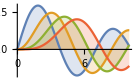
Graphics | ToString | TextString | SpokenString
-Graphics3D- | -Graphics3D- | Graphics3D[{RGBColor[1, 0, 0], Sphere[{0, 0, 0}]}] | a three-dimensional graphic consisting of a sphere
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of 11 polygons, a line connecting 574 points, a line connecting 541 points, a line connecting 556 points and a line connecting 610 points
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of 103 arrows and 103 disks

As it can be seen, the most human-readable version was the SpokenString function output. Even this, there are some cases in which it doesn’t bring a meaningful description, like in the second and third cases - it probably wouldn’t be possible to have a clear idea of the figure only with the texts. Also, it discards some aspects of the figure, like the color. Because of that, it was decided that the first small step would be to describe colors, for then integrate it into a more complete description function for graphics.

In this part I also created two functions to describe any wolfram language symbol - Description, to get the name of it; and TranslatedDescription, to get the translated name of it. Both of them use the WolframLanguageData presented previously. Here are some tests:

```mathematica
someWLSymbols={List,Table,Range,Graphics,Image,ColorQ,Number,Grid,Entity,Values,Map,Thread,Function, MapThread};

symbolDescriptionTests=Block[
{descriptions=Description@someWLSymbols,spanish,portuguese,japanese},
spanish=TranslatedDescription[someWLSymbols,"Spanish"];
portuguese=TranslatedDescription[someWLSymbols,"Portuguese"];
japanese=TranslatedDescription[someWLSymbols,"Japanese"];
MapThread[{#1,#2,#3,#4,#5}&,{someWLSymbols,descriptions,spanish,portuguese,japanese}]
];

Grid[PrependTo[symbolDescriptionTests,Style[#,Bold]&/@{"Original","Description","Spanish","Portuguese","Japanese"}],Frame->All]
```

Original | Description | Spanish | Portuguese | Japanese
List | List | lista | lista | リスト
Table | Table | tabla | tabela | リストを作成
Range | Range | rango | intervalo de valores | 範囲
Graphics | Graphics | gráfico | representação gráfica | グラフィックス
Image | Image | imagen | imagem | 画像
ColorQ | Color Q | ¿color? | Cor? | 色かどうか
Number | Number | número | número | 数
Grid | Grid | rejilla | grade | 格子
Entity | Entity | entidad | entidade | 実体
Values | Values | valores | lista de valores de associação | 値
Map | Map | aplica a todos | aplica-se ao primeiro nível | 適用
Thread | Thread | atraviesa | através das listas | 縫い込む
Function | Function | función | função | 関数
MapThread | Map Thread | aplica a través | aplica à ligação de elementos correspondentes | 縫込み適用

### Describing colors

Before starting describing colors, I discovered that the Wolfram Language have a set of named colors. These colors are the most common ones, and each has its own symbol in the Wolfram Language. Each of these symbols also have its own informations. My first objective was to filter, among all the symbols, the ones that are named colors. Once I had it, the idea was to create a function that would receive any RGBColor expression, compare it with all the named colors that I found, and return the name of the closest color.

For filtering the named colors among the Wolfram Language symbols, I saw that the "functionality areas" property for these symbols always was the value ColorSymbols. With that, I just filtered all the symbols that had this value for the cited property, and checked if they were a colors using the ColorQ function.

```mathematica
(*Getting the `functionality areas` property for the Red color.*)
EntityValue[WolframLanguageData["Red"], EntityProperty["WolframLanguageSymbol","FunctionalityAreas"]]
```

{ColorSymbols}

```mathematica
(*Filtering every named color among the Wolfram Language symbols, based on the `functionality areas` property.*)
functionalityAreasOfAllWLSymbols=MapThread[{#1,#2}&,{WolframLanguageData[],EntityValue[WolframLanguageData[],EntityProperty["WolframLanguageSymbol","FunctionalityAreas"]]}];
colorSymbols=Select[functionalityAreasOfAllWLSymbols, (Length@Last@#)==1&&((First@Last@#)=="ColorSymbols")&]⟦All,1⟧;
namedColors= Select[colorSymbols,ColorQ@RGBColor@#["Name"]&]
```

{Black,Blue,Brown,Cyan,Gray,Green,LightBlue,LightCyan,LightGreen,LightPink,LightYellow,Magenta,Orange,Pink,Purple,Red,White,Yellow}

After that I needed to address the problem of calculating the similarity between tow RGBColor expressions. My idea was to create a function the get the average of the differences of each color channel. For that, I created the ColorDistanceByAverage functions (I ended up not using this implementation in my final color description function because the built-in Nearest function uses the Euclidean distance by default).

```mathematica
ColorDistanceByAverage[color1_RGBColor,color2_RGBColor]:=N[Mean[MapThread[Abs[#1-#2]&,{List@@color1,List@@color2}]]]
```

```mathematica
ColorDistanceByAverage[Red,#]&/@{Red,Green,Blue,Pink}
```

{0.,0.666667,0.666667,0.333333}

Then, I created the Description function for RBGColor expressions. I also created the TransletedDescription version of it, that works similar to the TransletedDescription for symbols.

```mathematica
Description[color_RGBColor]:=Block[
{colors=<|RGBColor[0., 0., 0.]->Entity["WolframLanguageSymbol","Black"],RGBColor[0., 0., 1.]->Entity["WolframLanguageSymbol","Blue"],RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412]->Entity["WolframLanguageSymbol","Brown"],RGBColor[0., 1., 1.]->Entity["WolframLanguageSymbol","Cyan"],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]->Entity["WolframLanguageSymbol","Gray"],RGBColor[0., 0.5019607843137255, 0.]->Entity["WolframLanguageSymbol","Green"],RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726]->Entity["WolframLanguageSymbol","LightBlue"],RGBColor[0.87843137254902, 1., 1.]->Entity["WolframLanguageSymbol","LightCyan"],RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411]->Entity["WolframLanguageSymbol","LightGreen"],RGBColor[1., 0.7137254901960784, 0.7568627450980392]->Entity["WolframLanguageSymbol","LightPink"],RGBColor[1., 1., 0.87843137254902]->Entity["WolframLanguageSymbol","LightYellow"],RGBColor[1., 0., 1.]->Entity["WolframLanguageSymbol","Magenta"],RGBColor[1., 0.6470588235294118, 0.]->Entity["WolframLanguageSymbol","Orange"],RGBColor[1., 0.7529411764705882, 0.796078431372549]->Entity["WolframLanguageSymbol","Pink"],RGBColor[0.5019607843137255, 0., 0.5019607843137255]->Entity["WolframLanguageSymbol","Purple"],RGBColor[1., 0., 0.]->Entity["WolframLanguageSymbol","Red"],RGBColor[1., 1., 1.]->Entity["WolframLanguageSymbol","White"],RGBColor[1., 1., 0.]->Entity["WolframLanguageSymbol","Yellow"]|>,similar,entity},
similar=First@Nearest[Keys@colors,color,1];
entity=colors@similar;
Description[color]=ResourceFunction["FromCamelCase"]@entity@"Name"
]

outputComparations=With[{color=RGBColor@#},
{color,ToString@color,TextString@color,SpokenString@color,Description@color}]&/@RandomReal[1,{10,3}];

Grid[PrependTo[outputComparations,Style[#,Bold]&/@{"RGB color","ToString","TextString","SpokenString","Description"}],Frame->All]
```

RGB color | ToString | TextString | SpokenString | Description
RGBColor[{0.13834638211441952, 0.10944037874548829, 0.09705518183954887}] | RGBColor[{0.138346, 0.10944, 0.0970552}] | RGBColor[{0.138346, 0.10944, 0.0970552}] | RGB color 0.138, 0.109, 0.097 | Black
RGBColor[{0.6998114874500838, 0.013106753310190289, 0.7453896078041529}] | RGBColor[{0.699811, 0.0131068, 0.74539}] | RGBColor[{0.699811, 0.0131068, 0.74539}] | RGB color 0.7, 0.013, 0.745 | Purple
RGBColor[{0.41098744104091556, 0.8671517747586834, 0.6623246833367291}] | RGBColor[{0.410987, 0.867152, 0.662325}] | RGBColor[{0.410987, 0.867152, 0.662325}] | RGB color 0.411, 0.867, 0.662 | Light Green
RGBColor[{0.6371560959968514, 0.7985979800330758, 0.2571355735647842}] | RGBColor[{0.637156, 0.798598, 0.257136}] | RGBColor[{0.637156, 0.798598, 0.257136}] | RGB color 0.637, 0.799, 0.257 | Light Green
RGBColor[{0.548304732640936, 0.725850133023968, 0.1819235574702489}] | RGBColor[{0.548305, 0.72585, 0.181924}] | RGBColor[{0.548305, 0.72585, 0.181924}] | RGB color 0.548, 0.726, 0.182 | Green
RGBColor[{0.8818156401069392, 0.47620256378328363, 0.10674904138416186}] | RGBColor[{0.881816, 0.476203, 0.106749}] | RGBColor[{0.881816, 0.476203, 0.106749}] | RGB color 0.882, 0.476, 0.107 | Orange
RGBColor[{0.29500412829881206, 0.9079955791864953, 0.7014883513816168}] | RGBColor[{0.295004, 0.907996, 0.701488}] | RGBColor[{0.295004, 0.907996, 0.701488}] | RGB color 0.295, 0.908, 0.701 | Light Green
RGBColor[{0.43979550971980985, 0.3546381234991267, 0.012921790905866759}] | RGBColor[{0.439796, 0.354638, 0.0129218}] | RGBColor[{0.439796, 0.354638, 0.0129218}] | RGB color 0.44, 0.355, 0.013 | Gray
RGBColor[{0.10609572752463148, 0.9630025658230474, 0.8666665284503903}] | RGBColor[{0.106096, 0.963003, 0.866667}] | RGBColor[{0.106096, 0.963003, 0.866667}] | RGB color 0.106, 0.963, 0.867 | Cyan
RGBColor[{0.8443134928309199, 0.9344760613670275, 0.11019104425074921}] | RGBColor[{0.844313, 0.934476, 0.110191}] | RGBColor[{0.844313, 0.934476, 0.110191}] | RGB color 0.844, 0.934, 0.11 | Yellow

When compared with the built-in functions output, it can be said that the created function represents an improvement to describe colors. This part of the project was important to validate the path I was following by showing concrete results. Following, the version to return translated texts, and some examples.

```mathematica
TranslatedDescription[color_RGBColor,language_String]:=Block[
{colors=<|RGBColor[0., 0., 0.]->Entity["WolframLanguageSymbol","Black"],RGBColor[0., 0., 1.]->Entity["WolframLanguageSymbol","Blue"],RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412]->Entity["WolframLanguageSymbol","Brown"],RGBColor[0., 1., 1.]->Entity["WolframLanguageSymbol","Cyan"],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]->Entity["WolframLanguageSymbol","Gray"],RGBColor[0., 0.5019607843137255, 0.]->Entity["WolframLanguageSymbol","Green"],RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726]->Entity["WolframLanguageSymbol","LightBlue"],RGBColor[0.87843137254902, 1., 1.]->Entity["WolframLanguageSymbol","LightCyan"],RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411]->Entity["WolframLanguageSymbol","LightGreen"],RGBColor[1., 0.7137254901960784, 0.7568627450980392]->Entity["WolframLanguageSymbol","LightPink"],RGBColor[1., 1., 0.87843137254902]->Entity["WolframLanguageSymbol","LightYellow"],RGBColor[1., 0., 1.]->Entity["WolframLanguageSymbol","Magenta"],RGBColor[1., 0.6470588235294118, 0.]->Entity["WolframLanguageSymbol","Orange"],RGBColor[1., 0.7529411764705882, 0.796078431372549]->Entity["WolframLanguageSymbol","Pink"],RGBColor[0.5019607843137255, 0., 0.5019607843137255]->Entity["WolframLanguageSymbol","Purple"],RGBColor[1., 0., 0.]->Entity["WolframLanguageSymbol","Red"],RGBColor[1., 1., 1.]->Entity["WolframLanguageSymbol","White"],RGBColor[1., 1., 0.]->Entity["WolframLanguageSymbol","Yellow"]|>,similar,entity,lang,translations},
similar=First@Nearest[Keys@colors,color,1];
entity=colors@similar;
lang=Entity["Language",language];
translations=Association[entity@"Translations"];
TranslatedDescription[color,language]=ResourceFunction["FromCamelCase"]@translations@lang
]

colorTranslationTests={
#, Style[Description@#,#],
Style[TranslatedDescription[#,"Spanish"],#],
Style[TranslatedDescription[#,"Portuguese"],#],
Style[TranslatedDescription[#,"Japanese"],#]}&/@RGBColor/@RandomReal[1,{10,3}];

Grid[PrependTo[colorTranslationTests,Style[#,Bold]&/@{"RGB Color","English","Spanish","Portuguese","Japanese"}],Frame->All,Alignment->Left]
```

RGB Color | English | Spanish | Portuguese | Japanese
RGBColor[{0.5315508423688435, 0.8963071160423999, 0.08447860222293757}] | Light Green | verde claro | verde claro | 薄緑色
RGBColor[{0.8562436874347557, 0.893878676250859, 0.9084928333204632}] | White | blanco | branco | 白
RGBColor[{0.078990535524045, 0.2047584826132307, 0.9728208319859564}] | Blue | azul | azul | 青
RGBColor[{0.13184733619671873, 0.3559323783015158, 0.9632163441824413}] | Blue | azul | azul | 青
RGBColor[{0.32261583418055184, 0.6428518478739196, 0.2411705809881679}] | Green | verde | verde | 緑
RGBColor[{0.903279482578941, 0.29128764519587347, 0.9627255998789606}] | Magenta | magenta | magenta | マジェンタ色
RGBColor[{0.33752208400869743, 0.14683940761731473, 0.21909170395070832}] | Black | negro | preto | 黒
RGBColor[{0.4460312710483445, 0.6652266938300524, 0.7588244456181577}] | Light Blue | azul claro | azul claro | 水色
RGBColor[{0.10859052562981009, 0.42251186083727865, 0.2091899403102908}] | Green | verde | verde | 緑
RGBColor[{0.22433340366812882, 0.9301433802623331, 0.6934793545924998}] | Light Green | verde claro | verde claro | 薄緑色

### Describing graphics

The Graphics symbol in the Wolfram Language is a very flexible function, allowing dozens of configurations. It can be composed of primitives, directives, wrappers, options and method. For my project I decided to start with the primitives. This way, the first step of this sections was, as in the color description initial approach, to get every Wolfram Language symbol that are graphics primitives. The filter also is made with the "functionality areas" property, but now for the values equal to GraphicsPrimitiveSymbols.

```mathematica
(*Filtering every garphics primitives among the Wolfram Language symbols, based on the `functionality areas` property.*)
```

```mathematica
graphicsPrimitiveSymbols=Select[functionalityAreasOfAllWLSymbols,Count[Last@#,"GraphicsPrimitiveSymbols"]>0&];
graphicsSymbols=graphicsPrimitiveSymbols⟦All,1⟧
graphicsSymbols//Length
```

{AASTriangle,ASATriangle,AffineHalfSpace,AffineSpace,Annulus,Arrow,BSplineCurve,Ball,BezierCurve,CapsuleShape,Circle,Circumsphere,Cone,ConicHullRegion,Cube,Cuboid,Cylinder,DiskSegment,Dodecahedron,Ellipsoid,EmptyRegion,FilledCurve,FullRegion,GraphicsComplex,HalfLine,HalfPlane,HalfSpace,Hexahedron,Hyperplane,Icosahedron,InfiniteLine,InfinitePlane,Insphere,JoinedCurve,Octahedron,Parallelepiped,Parallelogram,Polyhedron,Prism,Rectangle,RegularPolygon,SASTriangle,SSSTriangle,ShellRegion,Simplex,Sphere,SphericalShell,StadiumShape,Tetrahedron,Triangle,Tube}

51

This, beyond allowing me to create the related Description and TranslatedDescription functions specifically for the graphics primitives symbols (they were created right after that), also allowed me to have a better notion of the project’s scope. After that I also created the GraphicsPrimtiveQ function to identify if a given string, symbol or expression represents a graphics primitive or not.

Here, the "documentation basic examples"  property was very useful. This property contains lots of ready examples to each symbol. The examples for the graphics primitives symbols was used for tests during the development. Without that I would have to create much more extra code for the tests.

```mathematica
(*Getting an example of use for the Rectangle symbol.*)
EntityValue[Entity["WolframLanguageSymbol","Rectangle"],EntityProperty["WolframLanguageSymbol","DocumentationBasicExamples"]]⟦4⟧
```

{Differently styled rectangles:,{Graphics[{Pink,Rectangle[]}],Graphics[{EdgeForm[Thick],Pink,Rectangle[]}],Graphics[{EdgeForm[Dashed],Pink,Rectangle[]}],Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,Rectangle[]}]},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

The next step was to create a function to finally describe a Graphics expression. So, I did it. The created function is capable of describing a Graphics expression in terms of graphics primitives symbols and colors.

```mathematica
Description[graphics_Graphics]:=Block[
{elements,primitives,sorted,descriptions},
elements=Flatten[List@@graphics];
primitives=Select[elements,(ColorQ@#||GraphicsPrimitiveQ@#)&];
sorted=Sort[#,ColorQ@#1&]&/@Partition[primitives,2];
descriptions=ToLowerCase[Description[#]]&/@sorted;
"A graphic consisting of "<>ToString@Row[Row[#," "]&/@descriptions, ", "]<>"."
]
```

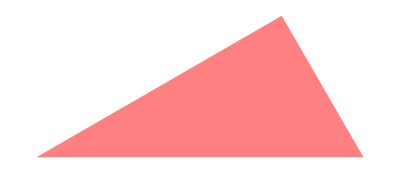
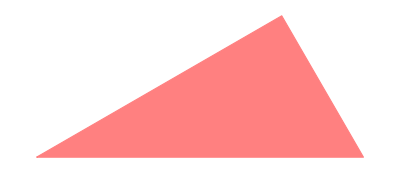
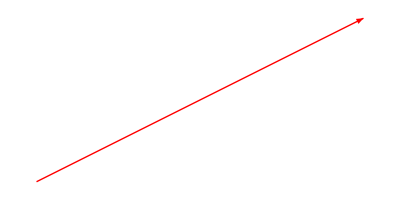
```mathematica
someGraphics={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
InputForm/@someGraphics
Grid[PrependTo[{#,ToString@#,TextString@#,SpokenString@#,Description@#}&/@someGraphics,Style[#,Bold]&/@{"Graphics","ToString","TextString","SpokenString","Description"}],Frame->All]
```

{Graphics[{RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {2, 0}, {3/2, Sqrt[3]/2}}]}],Graphics[{RGBColor[1, 0.5, 0.5], EdgeForm[Thickness[Large]], Triangle[{{0, 0}, {1, 0}, {3/4, Sqrt[3]/4}}]}],Graphics[{RGBColor[1, 0, 0], AffineHalfSpace[{0, 0}, {{1, -1}}, {1, 1}]}],Graphics[{RGBColor[0, 1, 0], AffineSpace[{0, 0}, {{1, -1}}]}],Graphics[{RGBColor[1, 0.5, 0.5], Annulus[{0, 0}, {1/2, 1}]}],Graphics[{RGBColor[1, 0, 0], {Arrowheads[Large], Arrow[{{0, 0}, {1, 0.5}}]}}]}

Graphics | ToString | TextString | SpokenString | Description
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 1, 0.5, 0.5 and Triangle of the list the list 0, 0, the list 2, 0, the list 3 halves, 1 half times square root of 3 | A graphic consisting of light pink triangle.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 1, 0.5, 0.5, edge form thickness Large and Triangle of the list the list 0, 0, the list 1, 0, the list 3 fourths, 1 fourth times square root of 3 | A graphic consisting of light pink triangle.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 1, 0, 0 and AffineHalfSpace of the list 0, 0, the list the list 1, minus 1 and the list 1, 1 | A graphic consisting of red affine half space.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 0, 1, 0 and AffineSpace of the list 0, 0 and the list the list 1, minus 1 | A graphic consisting of light green affine space.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 1, 0.5, 0.5 and Annulus of the list 0, 0 and the list 1 half, 1 | A graphic consisting of light pink annulus.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of an arrow | A graphic consisting of red arrow.

Despite its limitation, the Description function for Graphics also presents an improvement for the generated text. From this point, the next steps were to continue improving the description functions to add more characteristics of the expressions. Because of the great amount of primitives, the focus was given to a single one - the triangle. This way, the next improvements of the project were related to describing these polygons in more details.

### Working with triangles

The initial goal was to identify and say the type of triangle that is being displayed (right, equilateral, isosceles, scalene and obtuse). To achieve that, initially I created some auxiliary functions:

TrianglePointsQ : receives a list of points of the same dimension and returns if it forms a triangle or not.

TrianglePolygonQ: receives a triangle Polygon expression and returns if it is a triangle or not.

TriangleQ: is a generalization of the two previous ones. It can receive both a list of points of the same dimension or a polygon, and return if they are a triangle or not.

Later on, I created a TriangleTypeQ function for each triangle type. All of them receives a triangle polygon and returns if it is of the given type or not. The name of the created functions are: TriangleRightQ, TriangleEquilateralQ, TriangleIsoscelesQ, TriangleScaleneQ and TriangleObtuseQ. Following, some usage examples:

```mathematica
triangles={Triangle[],AASTriangle[Pi/6,Pi/3,1],SSSTriangle[3,4,5],SASTriangle[1,Pi/2,2],ASATriangle[Pi/6,1,Pi/3],Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}],Polygon[{{0,0},{10,10},{10,20}}],RandomPolygon@3};

triangleQs={TrianglePolygonQ,TriangleRightQ,TriangleEquilateralQ,TriangleIsoscelesQ,TriangleScaleneQ,TriangleObtuseQ};

triangleTests=Function[
triangle,
Flatten[
{{Graphics@triangle,
N[#/Degree]&/@PolygonAngle[triangle],
N@*EuclideanDistance@@#&/@Subsets[First[List@@triangle],{2}]},
With[
{answer=#[triangle]},
Style[TextString[answer,BooleanStrings-> {"Yes","No" }],If[answer,Blue,Red]]
]&/@triangleQs},
1
]
]/@triangles;

Grid[PrependTo[triangleTests,
Style[#,Bold]&/@{"Graphics","Interior angles","Side lengths", "Triangle?", "Right?", "Equilateral?","Isosceles?","Scalene?","Obtuse?"}],Frame->All]
```

Graphics | Interior angles | Side lengths | Triangle? | Right? | Equilateral? | Isosceles? | Scalene? | Obtuse?
-Graphics- | {90.,45.,45.} | {1.,1.,1.41421} | Yes | Yes | No | Yes | No | No
-Graphics- | {30.,60.,90.} | {2.,1.73205,1.} | Yes | Yes | No | No | Yes | No
-Graphics- | {36.8699,53.1301,90.} | {5.,4.,3.} | Yes | Yes | No | No | Yes | No
-Graphics- | {26.5651,63.4349,90.} | {2.23607,2.,1.} | Yes | Yes | No | No | Yes | No
-Graphics- | {30.,60.,90.} | {1.,0.866025,0.5} | Yes | Yes | No | No | Yes | No
-Graphics- | {60.,60.,60.} | {2.,2.,2.} | Yes | No | Yes | Yes | No | No
-Graphics- | {18.4349,135.,26.5651} | {14.1421,22.3607,10.} | Yes | No | No | No | Yes | Yes
-Graphics- | {305.923,261.548,332.529} | {0.530581,0.648081,0.302243} | Yes | No | No | No | Yes | Yes

With these functions I was already able to describe the triangles classification. To help me with this process, I created the TriangleCharacteristics function. This function receives a triangle polygon and returns a list of string with the name of each characteristic of the given triangle.

```mathematica
TriangleCharacteristics[triangle_]:=With[
{rules=<|TriangleRightQ-> "Right",TriangleEquilateralQ-> "Equilateral",TriangleIsoscelesQ-> "Isosceles",TriangleScaleneQ-> "Scalene",TriangleObtuseQ-> "Obtuse"|>},
Select[Keys@rules,#@triangle&]/.rules
]/;TriangleQ@triangle

TriangleCharacteristics/@triangles
```

{{Right,Isosceles},{Right,Scalene},{Right,Scalene},{Right,Scalene},{Right,Scalene},{Equilateral,Isosceles},{Scalene,Obtuse},{Scalene,Obtuse}}

Now, I need to describe one more thing about triangles: the orientation of the greatest side (is it a vertical, horizontal or diagonal line?). For doing so, it was necessary to develop an algorithm composed of three steps: 1) find the coordinates of the greatest side of a triangle, 2) get the inclination of this line and 3) decide the orientation of this line. For the first step, I created the TriangleGreatestSide function. Bellow, its definition and some examples.

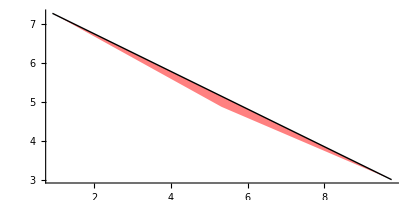
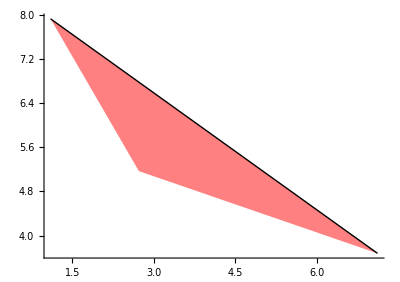
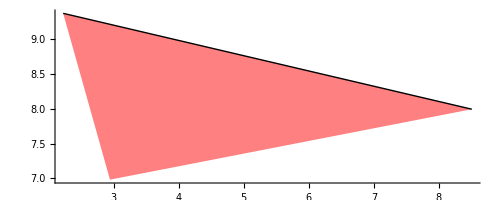
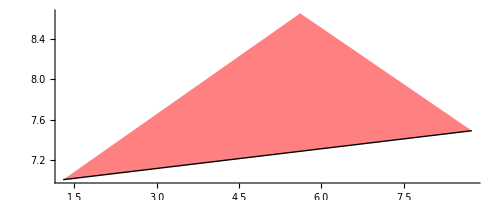
Greatest side coordinates | Triangle plot with the greates side
{{0.907494,7.26218},{9.75485,3.00329}} | -Graphics-
{{3.31056,8.43568},{4.62458,3.41327}} | -Graphics-
{{1.0978,7.92275},{7.1135,3.67798}} | -Graphics-
{{2.22301,9.3761},{8.50698,7.99443}} | -Graphics-
{{1.29424,7.00479},{8.74153,7.48903}} | -Graphics-

```mathematica
TriangleGreatestSide[triangle_]:=Block[
{coordinates,sides,lengths,greatestSideCoordinate},
coordinates=PolygonCoordinates@triangle;
sides=Subsets[coordinates,{2}];
lengths={#,N@*EuclideanDistance@@#}&/@sides;
greatestSideCoordinate=Sort[lengths,Last@#1>Last@#2&]⟦1,1⟧;
greatestSideCoordinate
]/;TrianglePolygonQ@triangle

sideTests=With[
{side=TriangleGreatestSide@#},
{side,Graphics[{Pink,#,Black,Thick,Line@side},Axes->True]}
]&/@Polygon/@RandomReal[10,{5,3,2}];

Grid[PrependTo[sideTests,Style[#,Bold]&/@{"Greatest side coordinates", "Triangle plot with the greates side"}],Frame->All]
```

To define the orientation of the greatest side I defined some angle regions for each possible orientation. For that, the trigonometric circle was divided in 32 small parts, with 4 of them to the horizontal orientation, other 4 to the vertical orientation and the rest to the diagonal orientation. Being this, any line that has the inclination that is inside of one of this regions is going to be considered in the respective orientation. The next figure illustrates each of these regions.

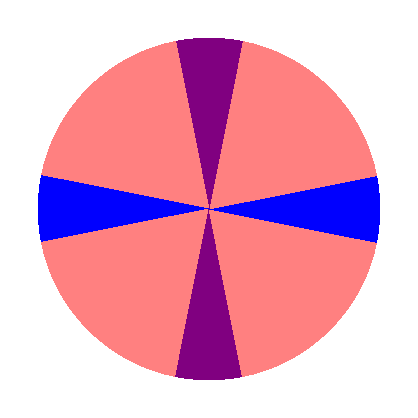
Regions to define the orientation of the greatest side of a triangle.
-Graphics-
Blue = Horizontal
Purple = Vertical
Pink = Diagonal

After getting the greatest side coordinates, I create another point, with the  x coordinate from the second point, and the y coordinate from first point. With this new point, and with the previous ones I create another triangle, and get the internal angle formed at the first point of this triangle. This angle gives me the inclination of the greatest side of the triangle. So this I can properly classify the orientation using my sectioned trigonometric circle. Bellow, I show the functions to each of this processes (Angle and AngleOrientation), and also some auxiliary plots.

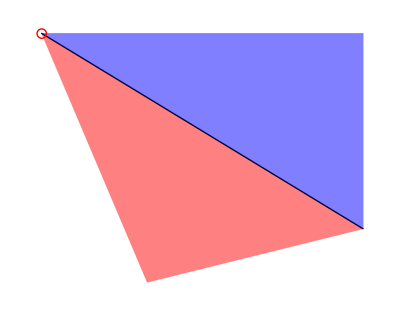
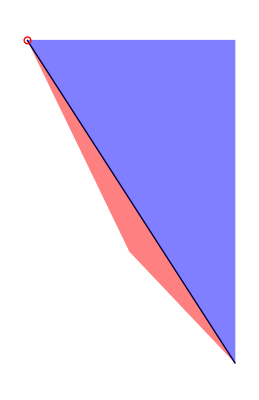
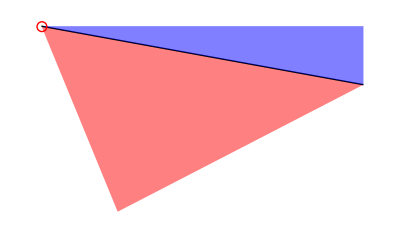
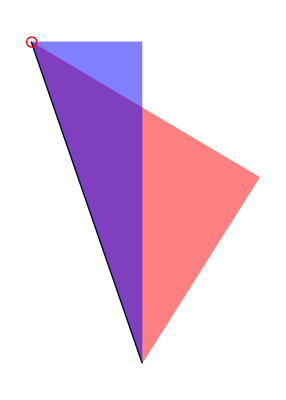
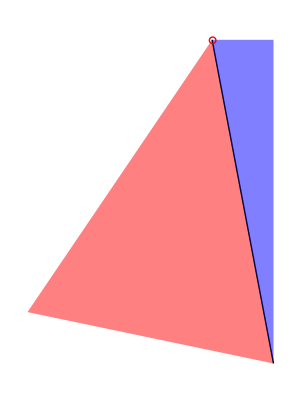
Original triangle (pink)
Auxiliar triangle (blue)
Greatest side (black line)
Angle (red circle) | Angle | Greatest side orientaiton
-Graphics- | 31.3503 | Diagonal
-Graphics- | 57.2153 | Diagonal
-Graphics- | 10.3197 | Horizontal
-Graphics- | 70.9265 | Diagonal
-Graphics- | 79.2349 | Diagonal

```mathematica
Angle[a_List,b_List]:=With[{c={b⟦1⟧,a⟦2⟧}},N@PlanarAngle[{b,a,c}]]/;Dimensions[a]==Dimensions[b]=={2}
Angle[points_List]:=Angle[First[points],Last[points]]

AngleOrientation[angle_Real]:=Block[
{normalized,possibilities,orientations=<|0.->"Horizontal",0.19634954084936207->"Horizontal",3.141592653589793->"Horizontal",3.3379421944391554->"Horizontal",6.283185307179586->"Horizontal",1.5707963267948966->"Vertical",1.7671458676442586->"Vertical",4.71238898038469->"Vertical",4.908738521234052->"Vertical",0.39269908169872414->"Diagonal",0.5890486225480862->"Diagonal",0.7853981633974483->"Diagonal",0.9817477042468103->"Diagonal",1.1780972450961724->"Diagonal",1.3744467859455345->"Diagonal",1.9634954084936207->"Diagonal",2.1598449493429825->"Diagonal",2.356194490192345->"Diagonal",2.552544031041707->"Diagonal",2.748893571891069->"Diagonal",2.945243112740431->"Diagonal",3.5342917352885173->"Diagonal",3.730641276137879->"Diagonal",3.9269908169872414->"Diagonal",4.123340357836604->"Diagonal",4.319689898685965->"Diagonal",4.516039439535327->"Diagonal",5.105088062083414->"Diagonal",5.301437602932776->"Diagonal",5.497787143782138->"Diagonal",5.6941366846315->"Diagonal",5.890486225480862->"Diagonal",6.086835766330224->"Diagonal"|>},
If[angle>2.Pi,normalized=Mod[angle,2.Pi],normalized=angle];
orientations@First@Nearest[Keys@orientations,normalized]
]

sideTests=With[
{side=TriangleGreatestSide@#},
{Graphics[{
Pink,#,
Black,Thick,Line@side,
Blue,Opacity@.5,Triangle[Append[side,{Last[side]⟦1⟧,First[side]⟦2⟧}]],
Red,Opacity@1.,Circle[First@side,0.1]
}],
N[Angle@side/Degree],
AngleOrientation@Angle@side}
]&/@Polygon/@RandomReal[10,{5,3,2}];

Grid[PrependTo[sideTests,Style[#,Bold]&/@{"Original triangle (pink)\nAuxiliar triangle (blue)\nGreatest side (black line)\nAngle (red circle)","Angle","Greatest side orientaiton"}],Frame->All]
```

The last step was to put all the functions related to triangles into a single functions capable of describing triangles in a Graphics expression, returning a human-readable string.  For this task I created the following code, that produces the results at the end.

```mathematica
StringList[list_List]:=With[{str=Row[ToLowerCase@list,", "]},
StringReplace[rest__~~", "~~s__~~EndOfString:> rest<>" and "<>s]@ToString[str]]

TriangleDescription[triangle_]:=Block[{characteristics,side,sidestr},
characteristics=StringList@TriangleCharacteristics@triangle;
side=AngleOrientation@Angle@TriangleGreatestSide@triangle;
sidestr=If[Not[TriangleEquilateralQ@triangle]," triangle, with its greatest side as a "<>ToLowerCase[side]<>" line"," triangle"];
characteristics<>sidestr]/;SimplePolygonQ@triangle

TriangleDescription[graphics_Graphics]:=Block[{primitivesAndDirectives,color,triangleDescription},
primitivesAndDirectives=graphics/.Graphics[arguments_List,___]:>  arguments;
color=ToLowerCase[Description[Select[primitivesAndDirectives,ColorQ]//First]];
triangleDescription=TriangleDescription[Select[primitivesAndDirectives,TrianglePolygonQ]//First];
"A graphic consisting of a "<>color<>", "<>triangleDescription<>"."]

triangleDescriptionTests=Block[{color,graphics},
color=RGBColor@RandomReal[1,{3}];
graphics=Graphics[{color,#}];
{graphics,ToString@graphics,TextString@graphics,SpokenString@graphics,TriangleDescription@graphics}]&/@triangles;
Grid[PrependTo[triangleDescriptionTests,Style[#,Bold]&/@{"Graphics","ToString","TextString","SpokenString","TriangleDescription"}],Frame->All]
```

Graphics | ToString | TextString | SpokenString | TriangleDescription
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 0.011, 0.974, 0.156 and Triangle of the list the list 0, 0, the list 1, 0, the list 0, 1 | A graphic consisting of a light green, right and isosceles triangle, with its greatest side as a diagonal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 0.917, 0.157, 0.193 and Triangle of the list the list 0, 0, the list 2, 0, the list 3 halves, 1 half times square root of 3 | A graphic consisting of a red, right and scalene triangle, with its greatest side as a horizontal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 0.465, 0.007, 0.093 and Triangle of the list the list 0, 0, the list 5, 0, the list 16 fifths, 12 fifths | A graphic consisting of a brown, right and scalene triangle, with its greatest side as a horizontal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 0.686, 0.281, 0.977 and Triangle of the list the list 0, 0, the list square root of 5, 0, the list 4 times one over square root of 5, 2 times one over square root of 5 | A graphic consisting of a magenta, right and scalene triangle, with its greatest side as a horizontal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 0.66, 0.275, 0.915 and Triangle of the list the list 0, 0, the list 1, 0, the list 3 fourths, 1 fourth times square root of 3 | A graphic consisting of a magenta, right and scalene triangle, with its greatest side as a horizontal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a orange, equilateral and isosceles triangle.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a gray, scalene and obtuse triangle, with its greatest side as a diagonal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a light green, scalene triangle, with its greatest side as a diagonal line.

It is important to note that for equilateral triangles the greatest side orientation is not being described, because all the sides are equal.

### Conclusion and future works

This project presented a challenging task, with a very large scope of implementation. In this first step, some important progress was made related to textually describing Wolfram Language expressions, in special for Graphics, and for triangle figures. Following, some of the future works that can be done.

Merge the Description and TranslatedDescription functions for symbols into a single one that can receive the language as an option.

Merge the Description and TranslatedDescription functions for colors into a single one that can receive the language as an option.

Improve the Description function implementation for graphics, so this it can support more graphics primitives, and also the other components of the Graphics expressions.

Enhance the Description function implementation for graphics, so this it also can describe points and lines plots properly.

Put the TriangleDescription function inside a more generic Description function that supports any type of polygon.

Increase the scope of the project for other types of expressions.

Test the output quality for the description functions for graphics and triangles.

Create functions and/or applications that can be used with visually impaired people. For example , an application to help with the geometry teaching.

## Complete project work

### Manipulating Wolfram Language symbols

```mathematica
?WolframLanguageData
```

```mathematica
wlSymbols=WolframLanguageData[];
```

```mathematica
wlSymbols//Length
```

0

```mathematica
wlEntityProperties=WolframLanguageData["Properties"]
```

{attributes,character count,common option values,date introduced,date last modified,dates modified,documentation basic examples,documentation example counts,documentation example inputs,documentation example text,entity classes,eponymous people,equal-precedence symbols,external links,frequencies of usage,full version introduced,full version last modified,full versions modified,functionality areas,symbol background,keyboard shortcuts,link trails,memberships,name,option names,options,plaintext usage,precedence ranks,ranks of usage,related entities,related guide pages,related symbols,relationship community graph,relationship graph,short notations,subject classifications,symbols linking to,symbols using as attribute,symbols using as option,text strings,timeline,timeline events,translations,typeset usage,URL,version introduced,version last modified,versions modified,Wolfram documentation link}

```mathematica
functionalityAreasOfAllWLSymbols=MapThread[{#1,#2}&,{wlSymbols,EntityValue[wlSymbols,EntityProperty["WolframLanguageSymbol","FunctionalityAreas"]]}];
```

#### Function to get every property of a symbol

```mathematica
AllPropertiesForSymbol[symbol_Symbol]:=EntityValue[WolframLanguageData@ToString@symbol,WolframLanguageData["Properties"]]
```

#### Function to get the relationship and community graphs of a symbol

```mathematica
RelationshipGraphs[symbol_Symbol]:=EntityValue[WolframLanguageData@ToString@symbol,{EntityProperty["WolframLanguageSymbol","RelationshipGraph"],EntityProperty["WolframLanguageSymbol","RelationshipCommunityGraph"]}]
```

### Already built-in functions to describe Wolfram Language expressions

#### SpokenString

```mathematica
redSphere=Graphics3D[{Red,Sphere[]}]
```

-Graphics3D-

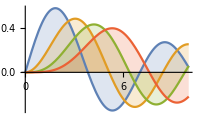

```mathematica
complexGraph=Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

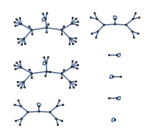

```mathematica
someGraphs=GraphPlot[Table[i->Mod[i^2,102],{i,0,102}]]
```

```mathematica
?SpokenString
SpokenString@redSphere
SpokenString@complexGraph
SpokenString@someGraphs
```

a three-dimensional graphic consisting of a sphere

a graphic consisting of 11 polygons, a line connecting 574 points, a line connecting 541 points, a line connecting 556 points and a line connecting 610 points

a graphic consisting of 103 arrows and 103 disks

```mathematica
RelationshipGraphs@SpokenString
```

RelationshipGraphs[SpokenString]

#### TextString

```mathematica
?TextString
TextString@redSphere
TextString@complexGraph
TextString@someGraphs
```

Graphics3D[{RGBColor[1, 0, 0], Sphere[{0, 0, 0}]}]

Graphics[…]

Graphics[…]

```mathematica
RelationshipGraphs@TextString
```

RelationshipGraphs[TextString]

#### ToString

```mathematica
?ToString
ToString@redSphere
ToString@complexGraph
ToString@someGraphs
```

-Graphics3D-

-Graphics-

-Graphics-

```mathematica
RelationshipGraphs@ToString
```

RelationshipGraphs[ToString]

#### Output for the publication

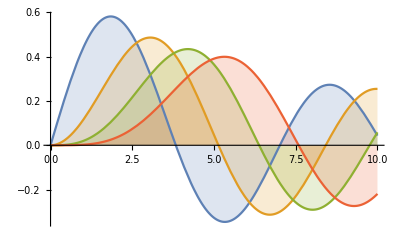
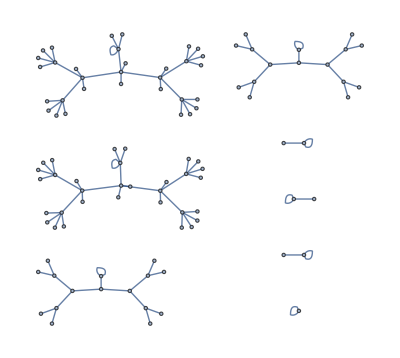
Graphics | ToString | TextString | SpokenString
-Graphics3D- | -Graphics3D- | Graphics3D[{RGBColor[1, 0, 0], Sphere[{0, 0, 0}]}] | a three-dimensional graphic consisting of a sphere
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of 11 polygons, a line connecting 574 points, a line connecting 541 points, a line connecting 556 points and a line connecting 610 points
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of 103 arrows and 103 disks

```mathematica
Grid[{
Style[#,Bold]&/@{"Graphics","ToString","TextString","SpokenString"},
{redSphere,ToString@redSphere,TextString@redSphere,SpokenString@redSphere},
{complexGraph,ToString@complexGraph,TextString@complexGraph,SpokenString@complexGraph},
{someGraphs,ToString@someGraphs,TextString@someGraphs,SpokenString@someGraphs}
},Frame->All]
```

#### Description and TranslatedDescription functions for symbols

```mathematica
Clear@Description
```

```mathematica
Description[symbol_Symbol]:=With[
{entity=Entity["WolframLanguageSymbol",ToString@symbol]},
Description[symbol]=ResourceFunction["FromCamelCase"]@entity@"Name"
]

SetAttributes[Description,Listable]
```

```mathematica
Clear@TranslatedDescription
```

```mathematica
TranslatedDescription[symbol_Symbol,language_String]:=Block[
{entity,lang,translations},
entity=Entity["WolframLanguageSymbol",ToString@symbol];
lang=Entity["Language",language];
translations=Association[entity@"Translations"];
TranslatedDescription[symbol,language]=ResourceFunction["FromCamelCase"]@translations@lang
]
TranslatedDescription[symbol_Symbol]:=Description[symbol]

SetAttributes[TranslatedDescription,Listable]
```

Some tests

```mathematica
someWLSymbols={List,Table,Range,Graphics,Image,ColorQ,Number,Grid,Entity,Values,Map,Thread,Function, MapThread}
```

{List,Table,Range,Graphics,Image,ColorQ,Number,Grid,Entity,Values,Map,Thread,Function,MapThread}

```mathematica
Head/@someWLSymbols
```

{Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol}

```mathematica
symbolDescriptionTests=Module[
{descriptions=Description@someWLSymbols,spanish,portuguese,japanese},
spanish=TranslatedDescription[someWLSymbols,"Spanish"];
portuguese=TranslatedDescription[someWLSymbols,"Portuguese"];
japanese=TranslatedDescription[someWLSymbols,"Japanese"];
MapThread[{#1,#2,#3,#4,#5}&,{someWLSymbols,descriptions,spanish,portuguese,japanese}]
];
```

```mathematica
Grid[symbolDescriptionTests,Frame->All]
```

List | List | lista | lista | リスト
Table | Table | tabla | tabela | リストを作成
Range | Range | rango | intervalo de valores | 範囲
Graphics | Graphics | gráfico | representação gráfica | グラフィックス
Image | Image | imagen | imagem | 画像
ColorQ | Color Q | ¿color? | Cor? | 色かどうか
Number | Number | número | número | 数
Grid | Grid | rejilla | grade | 格子
Entity | Entity | entidad | entidade | 実体
Values | Values | valores | lista de valores de associação | 値
Map | Map | aplica a todos | aplica-se ao primeiro nível | 適用
Thread | Thread | atraviesa | através das listas | 縫い込む
Function | Function | función | função | 関数
MapThread | Map Thread | aplica a través | aplica à ligação de elementos correspondentes | 縫込み適用

### A parenthesis: the PrintDefinitions function

PrintDefinitions, a function from the Wolfram Function repository, creates a notebook object for a WL symbol, containing the symbol documentation/definition content.

```mathematica
ResourceFunction["PrintDefinitions"]
```

```mathematica
ResourceFunction["PrintDefinitions"]@Graphics
```

4xqkf_shm18FrontEndObject[LinkObject["4xqkf_shm", 3, 1]]18System`Graphics

### Describing Colors

#### Named Colors

```mathematica
redNamedColorWLEntity=WolframLanguageData["Red"]
```

Red

```mathematica
entityPropertyValuesForRedColor={#,EntityValue[redNamedColorWLEntity, #]}&/@wlEntityProperties;
```


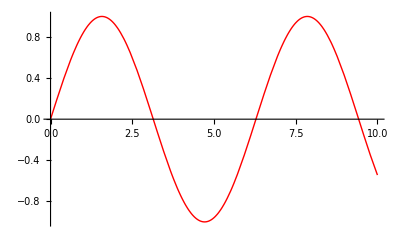
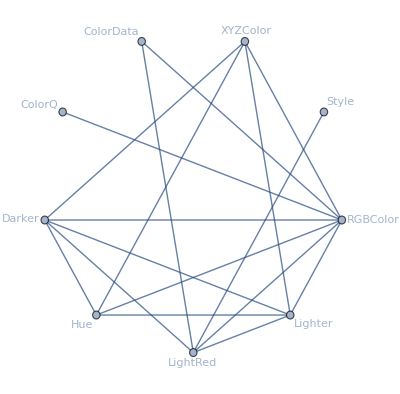
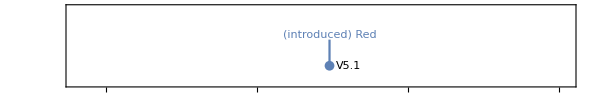
attributes | {Protected}
character count | 3
date introduced | Day: Mon 25 Oct 2004
documentation basic examples | {{Graphics[{Red,Disk[]}],-Graphics-,Plot[Sin[x],{x,0,10},PlotStyle→Red],-Graphics-,Graphics3D[{Red,Sphere[]}],-Graphics3D-}}
documentation example counts | {BasicExamples→1,Scope→0,GeneralizationsExtensions→0,Options→0,Applications→0,PropertiesRelations→0,PossibleIssues→0,InteractiveExamples→0,NeatExamples→0}
documentation example inputs | {BasicExamples→{{Graphics[{Red,Disk[]}],Plot[Sin[x],{x,0,10},PlotStyle→Red],Graphics3D[{Red,Sphere[]}]}},Scope→{},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{}}
documentation example text | {BasicExamples→{{}},Scope→{},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{}}
entity classes | {Wolfram Language autoevaluating symbols}
eponymous people | {}
external links | {}
frequencies of usage | {All→0.000434382,StackExchange→0.00233259,TypicalProductionCode→0.0010278,WolframAlphaCodebase→0.0000142108,WolframDemonstrations→0.00218411,WolframDocumentation→0.00162619}
full version introduced | 5.1
functionality areas | {ColorSymbols}
symbol background | Red is a symbol that represents the color red in graphics or style specifications. Color specifications in the Wolfram Language can appear explicitly inside a Graphics or Graphics3D expression (e.g. Graphics[{Red,Disk[]}]), in which case they affect all subsequent expressions until another specification overrides them. They can also be used as part of an option specification, either singly (e.g. Plot[Sin[x],{x,0,2Pi},PlotStyle->Red]) or as part of a Directive compound expression (e.g. Plot[Cos[x],{x,0,2Pi},PlotStyle->Directive[Thick,Red]]). Finally, they can appear inside Style wrappers that affect the appearance of text, equations, and notebook cells (e.g. Style[hello,Red]).
Red is a color located at one of the corners of the RGB color cube and evaluates to RGBColor[1,0,0].
Named symbols for other colors include Green, Blue, Black, White, Gray, Cyan, Magenta, Yellow, Brown, Orange, Pink, and Purple, as well as their LightRed etc. variants. Arbitrary colors can be input using Hue, RGBColor, CMYKColor, LABColor, LUVColor, or XYZColor. Colors can be modified using Lighter, Darker, and Blend. Colors may be converted between different systems using ColorConvert. The appearance of colors appearing in Graphics3D objects may be controlled using Glow, Specularity, and Lighting. The transparency of colored graphics objectives can be specified using Opacity. ColorData can be used to give a function that generates colors in a named color scheme.
link trails | {{guide/WolframRoot,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/GraphicsOptionsAndStyling,guide/Colors,ref/Red},{guide/WolframRoot,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ImageProcessing,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ImageProcessing,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ChartingAndInformationVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ChartingAndInformationVisualization,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Finance,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ActuarialComputation,guide/Finance,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ActuarialComputation,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/DateAndTime,guide/DateAndTimeVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/EarthSciencesDataAndComputation,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Finance,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Geodesy,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/LifeSciencesAndMedicineDataAndComputation,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/PeopleAndHistory,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ProbabilityAndStatistics,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/DescriptiveStatistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Statistics,guide/DescriptiveStatistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTimeVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red}}
memberships | {Wolfram Language autoevaluating symbols}
name | Red
option names | {}
options | {}
plaintext usage | Red represents the color red in graphics or style specifications.
ranks of usage | {All→91,StackExchange→41,TypicalProductionCode→87,WolframAlphaCodebase→398,WolframDemonstrations→48,WolframDocumentation→54}
related entities | {red}
related guide pages | {Colorspaclet:guide/Colors,Symbolic Graphics Languagepaclet:guide/SymbolicGraphicsLanguage,Graphics Options & Stylingpaclet:guide/GraphicsOptionsAndStyling,Graphics Annotation & Appearancepaclet:guide/GraphicsAnnotationAndAppearance,Graphics Directivespaclet:guide/GraphicsDirectives,Maps & Cartographypaclet:guide/MapsAndCartography,Color Processingpaclet:guide/ColorProcessing,Notebook Formatting & Stylingpaclet:guide/NotebookFormattingAndStyling,Chart Styling & Layoutpaclet:guide/ChartLayoutAndStyling,Graph Visualizationpaclet:guide/GraphVisualization,Text Stylingpaclet:guide/TextStyling,GeoGraphics Languagepaclet:guide/GeoGraphicsLanguage,Graph Styling, Labeling, and Layoutpaclet:guide/GraphStylingAndLabeling,Maps & Cartographypaclet:guide/MapsAndGeographicData}
related symbols | {LightRed,ColorData,Lighter,Darker,Hue,RGBColor,Style}
relationship community graph | -Graphics-
relationship graph | -Graphics-
symbols linking to | {ColorQ,Hue,LightRed,RGBColor,XYZColor}
symbols using as attribute | {}
symbols using as option | {}
text strings | {Red represents the color red in graphics or style specifications.,Red is equivalent to RGBColor[1,0,0].,Red is a symbol that represents the color red in graphics or style specifications. Color specifications in the Wolfram Language can appear explicitly inside a Graphics or Graphics3D expression (e.g. Graphics[{Red,Disk[]}]), in which case they affect all subsequent expressions until another specification overrides them. They can also be used as part of an option specification, either singly (e.g. Plot[Sin[x],{x,0,2Pi},PlotStyle->Red]) or as part of a Directive compound expression (e.g. Plot[Cos[x],{x,0,2Pi},PlotStyle->Directive[Thick,Red]]). Finally, they can appear inside Style wrappers that affect the appearance of text, equations, and notebook cells (e.g. Style["hello",Red]).,Red is a color located at one of the corners of the RGB color cube and evaluates to RGBColor[1,0,0].,Named symbols for other colors include Green, Blue, Black, White, Gray, Cyan, Magenta, Yellow, Brown, Orange, Pink, and Purple, as well as their LightRed etc. variants. Arbitrary colors can be input using Hue, RGBColor, CMYKColor, LABColor, LUVColor, or XYZColor. Colors can be modified using Lighter, Darker, and Blend. Colors may be converted between different systems using ColorConvert. The appearance of colors appearing in Graphics3D objects may be controlled using Glow, Specularity, and Lighting. The transparency of colored graphics objectives can be specified using Opacity. ColorData can be used to give a function that generates colors in a named color scheme.}
timeline | -Graphics-
timeline events | Day: Mon 25 Oct 2004Red
translations | {Simplified Chinese→红色,Traditional Chinese→紅色,French→rouge,German→rot,Modern Greek→κόκκινο,Japanese→赤,Korean→빨강,Lithuanian→raudonas,Polish→czerwony,Portuguese→vermelho,Russian→красный,Spanish→rojo,Ukrainian→червоний,Vietnamese→đỏ}
typeset usage | Red represents the color red in graphics or style specifications. 
URL | http://reference.wolfram.com/language/ref/Red.html
version introduced | 5.1
Wolfram documentation link | Redpaclet:ref/Red

```mathematica
Grid[Select[entityPropertyValuesForRedColor, Not@MissingQ@Last@#&], Frame->All]
```

```mathematica
colorSymbols=Select[functionalityAreasOfAllWLSymbols, (Length@Last@#)==1&&((First@Last@#)=="ColorSymbols")&]⟦All,1⟧
```

{Black,Blend,Blue,Brown,CMYKColor,ChromaticityPlot,ChromaticityPlot3D,ColorBalance,ColorCombine,ColorConvert,ColorCoverage,ColorData,ColorDataFunction,ColorDetect,ColorDistance,ColorFunction,ColorFunctionScaling,ColorNegate,ColorProfileData,ColorQ,ColorQuantize,ColorReplace,ColorRules,ColorSeparate,ColorSetter,ColorSpace,ColorToneMapping,Colorize,ColorsNear,Cyan,Darker,Dithering,FindMatchingColor,Glow,Gray,GrayLevel,Green,Hue,ImageColorSpace,LABColor,LCHColor,LUVColor,LightBlue,LightBrown,LightCyan,LightGray,LightGreen,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightYellow,Lighter,Magenta,MaxColorDistance,MinColorDistance,Orange,Pink,Purple,RGBColor,RandomColor,Red,StreamColorFunction,StreamColorFunctionScaling,VectorColorFunction,VectorColorFunctionScaling,White,WhitePoint,XYZColor,Yellow}

```mathematica
namedColors= Select[colorSymbols,ColorQ@RGBColor@#["Name"]&]
```

{Black,Blue,Brown,Cyan,Gray,Green,LightBlue,LightCyan,LightGreen,LightPink,LightYellow,Magenta,Orange,Pink,Purple,Red,White,Yellow}

```mathematica
Grid[{#, RGBColor@#@"Name", #@"Name", #@"Translations"}&/@namedColors, Frame->All]
```

Black | RGBColor[0., 0., 0.] | Black | {Simplified Chinese→黑色,Traditional Chinese→黑,French→noir,German→schwarz,Modern Greek→μαύρο,Japanese→黒,Korean→검정,Lithuanian→juodas,Polish→czarny,Portuguese→preto,Russian→чёрный,Spanish→negro,Ukrainian→чорний,Vietnamese→đen}
Blue | RGBColor[0., 0., 1.] | Blue | {Simplified Chinese→蓝色,Traditional Chinese→藍色,French→bleu,German→blau,Modern Greek→μπλε,Japanese→青,Korean→파랑,Lithuanian→mėlynas,Polish→niebieski,Portuguese→azul,Russian→синий,Spanish→azul,Ukrainian→синій,Vietnamese→xanh da trời}
Brown | RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412] | Brown | {Simplified Chinese→棕色,Traditional Chinese→棕色,French→marron,German→braun,Modern Greek→καφέ,Japanese→茶色,Korean→갈색,Lithuanian→rudas,Polish→brązowy,Portuguese→marrom,Russian→коричневый,Spanish→marrón,Ukrainian→коричневий,Vietnamese→nâu}
Cyan | RGBColor[0., 1., 1.] | Cyan | {Simplified Chinese→蓝绿色,Traditional Chinese→藍綠色,French→cyan,German→blaugrün,Modern Greek→κυανό,Japanese→シアン色,Korean→청록색,Lithuanian→žalsvai mėlynas,Polish→cyjan,Portuguese→azul turquesa,Russian→голубой,Spanish→cian,Ukrainian→блакитний,Vietnamese→lục lam}
Gray | RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | Gray | {Simplified Chinese→灰色,Traditional Chinese→灰,French→gris,German→grau,Modern Greek→γκρι,Japanese→灰色,Korean→회색,Lithuanian→pilkas,Polish→szary,Portuguese→cinza,Russian→серый,Spanish→gris,Ukrainian→сірий,Vietnamese→xám}
Green | RGBColor[0., 0.5019607843137255, 0.] | Green | {Simplified Chinese→绿色,Traditional Chinese→綠色,French→vert,German→grün,Modern Greek→πράσινο,Japanese→緑,Korean→녹색,Lithuanian→žalias,Polish→zielony,Portuguese→verde,Russian→зелёный,Spanish→verde,Ukrainian→зелений,Vietnamese→xanh lá}
LightBlue | RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726] | LightBlue | {Simplified Chinese→浅蓝色,Traditional Chinese→淡藍色,French→bleu clair,German→hellblau,Modern Greek→γαλάζιο,Japanese→水色,Korean→하늘색,Lithuanian→šviesiai mėlyna,Polish→jasnoniebieski,Portuguese→azul claro,Russian→светло-синий,Spanish→azul claro,Ukrainian→світло-синій,Vietnamese→xanh da trời nhạt}
LightCyan | RGBColor[0.87843137254902, 1., 1.] | LightCyan | {Simplified Chinese→淡青色,Traditional Chinese→淡青色,French→cyan clair,German→helles Blaugrün,Modern Greek→ανοιχτό κυανό,Japanese→薄いシアン色,Korean→밝은 청록색,Lithuanian→šviesiai žalsvai mėlyna,Polish→jasny cyjan,Portuguese→azul turquesa claro,Russian→светло-голубой,Spanish→cian claro,Ukrainian→світло-блакитний,Vietnamese→lục lam nhạt}
LightGreen | RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411] | LightGreen | {Simplified Chinese→浅绿,Traditional Chinese→淡綠色,French→vert clair,German→hellgrün,Modern Greek→ανοιχτό πράσινο,Japanese→薄緑色,Korean→연두색,Lithuanian→šviesiai žalia,Polish→jasnozielony,Portuguese→verde claro,Russian→светло-зелёный,Spanish→verde claro,Ukrainian→світло-зелений,Vietnamese→xanh lá cây nhạt}
LightPink | RGBColor[1., 0.7137254901960784, 0.7568627450980392] | LightPink | {Simplified Chinese→浅粉色,Traditional Chinese→淡粉色,French→rose clair,German→hellrosa,Modern Greek→ανοιχτό ροζ,Japanese→薄いピンク色,Korean→연분홍색,Lithuanian→šviesiai rausvos,Polish→jasnoróżowy,Portuguese→rosa claro,Russian→светло-розовый,Spanish→rosa claro,Ukrainian→світло-рожевий,Vietnamese→hồng nhạt}
LightYellow | RGBColor[1., 1., 0.87843137254902] | LightYellow | {Simplified Chinese→浅黄色,Traditional Chinese→淡黃色,French→jaune clair,German→hellgelb,Modern Greek→ανοιχτό κίτρινο,Japanese→薄い黄色,Korean→담황색,Lithuanian→šviesiai geltonos,Polish→jasnożółty,Portuguese→amarelo claro,Russian→светло-жёлтый,Spanish→amarillo claro,Ukrainian→світло-жовтий,Vietnamese→vàng nhạt}
Magenta | RGBColor[1., 0., 1.] | Magenta | {Simplified Chinese→品红色,Traditional Chinese→品紅色,French→magenta,German→magenta,Modern Greek→ματζέντα,Japanese→マジェンタ色,Korean→마젠타 색,Lithuanian→tamsiai raudonas,Polish→magenta,Portuguese→magenta,Russian→малиновый,Spanish→magenta,Ukrainian→малиновий,Vietnamese→đỏ tươi}
Orange | RGBColor[1., 0.6470588235294118, 0.] | Orange | {Simplified Chinese→橙色,Traditional Chinese→橙色,French→orange,German→orange,Modern Greek→πορτοκαλί,Japanese→オレンジ色,Korean→오렌지,Lithuanian→oranžinis,Polish→pomarańczowy,Portuguese→laranja,Russian→оранжевый,Spanish→naranja,Ukrainian→помаранчевий,Vietnamese→cam}
Pink | RGBColor[1., 0.7529411764705882, 0.796078431372549] | Pink | {Simplified Chinese→粉色,Traditional Chinese→粉紅色,French→rose,German→rosa,Modern Greek→ροζ,Japanese→ピンク色,Korean→분홍색,Lithuanian→rožinis,Polish→różowy,Portuguese→rosa,Russian→розовый,Spanish→rosa,Ukrainian→рожевий,Vietnamese→hồng}
Purple | RGBColor[0.5019607843137255, 0., 0.5019607843137255] | Purple | {Simplified Chinese→紫色,Traditional Chinese→紫色,French→violet,German→lila,Modern Greek→μωβ,Japanese→紫色,Korean→보라색,Lithuanian→purpurinis,Polish→purpurowy,Portuguese→roxo,Russian→фиолетовый,Spanish→púrpura,Ukrainian→фіолетовий,Vietnamese→tím}
Red | RGBColor[1., 0., 0.] | Red | {Simplified Chinese→红色,Traditional Chinese→紅色,French→rouge,German→rot,Modern Greek→κόκκινο,Japanese→赤,Korean→빨강,Lithuanian→raudonas,Polish→czerwony,Portuguese→vermelho,Russian→красный,Spanish→rojo,Ukrainian→червоний,Vietnamese→đỏ}
White | RGBColor[1., 1., 1.] | White | {Simplified Chinese→白色,Traditional Chinese→白色,French→blanc,German→weiß,Modern Greek→λευκό,Japanese→白,Korean→흰색,Lithuanian→baltas,Polish→biały,Portuguese→branco,Russian→белый,Spanish→blanco,Ukrainian→білий,Vietnamese→trắng}
Yellow | RGBColor[1., 1., 0.] | Yellow | {Simplified Chinese→黄色,Traditional Chinese→黄色,French→jaune,German→gelb,Modern Greek→κίτρινο,Japanese→黄色,Korean→노란색,Lithuanian→geltonas,Polish→żółty,Portuguese→amarelo,Russian→жёлтый,Spanish→amarillo,Ukrainian→жовтий,Vietnamese→vàng}

```mathematica
namedColorsRGB=Association[RGBColor@#@"Name"->#&/@namedColors]
```

<|RGBColor[0., 0., 0.]→Black,RGBColor[0., 0., 1.]→Blue,RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412]→Brown,RGBColor[0., 1., 1.]→Cyan,RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]→Gray,RGBColor[0., 0.5019607843137255, 0.]→Green,RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726]→LightBlue,RGBColor[0.87843137254902, 1., 1.]→LightCyan,RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411]→LightGreen,RGBColor[1., 0.7137254901960784, 0.7568627450980392]→LightPink,RGBColor[1., 1., 0.87843137254902]→LightYellow,RGBColor[1., 0., 1.]→Magenta,RGBColor[1., 0.6470588235294118, 0.]→Orange,RGBColor[1., 0.7529411764705882, 0.796078431372549]→Pink,RGBColor[0.5019607843137255, 0., 0.5019607843137255]→Purple,RGBColor[1., 0., 0.]→Red,RGBColor[1., 1., 1.]→White,RGBColor[1., 1., 0.]→Yellow|>

#### ColorDistanceByAverage function

```mathematica
ColorDistanceByAverage[color1_RGBColor,color2_RGBColor]:=N[Mean[MapThread[Abs[#1-#2]&,{List@@color1,List@@color2}]]]
```

Some tests

```mathematica
ColorDistanceByAverage[Red,Red]
ColorDistanceByAverage[Red,Green]
ColorDistanceByAverage[Red,Blue]
ColorDistanceByAverage[Red,Pink]
ColorDistanceByAverage[Red,Black]
```

0.

0.666667

0.666667

0.333333

ColorDistanceByAverage[RGBColor[1, 0, 0],GrayLevel[0]]

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
nearestColor = Nearest[Keys@namedColorsRGB,randomColor,1]//First
namedColorsRGB[nearestColor]["Name"]
Association[namedColorsRGB[nearestColor]["Translations"]][Entity["Language","Portuguese"]]
```

RGBColor[0.2843644344643541, 0.19736098609994368, 0.6925807675336668]

RGBColor[0.5019607843137255, 0., 0.5019607843137255]

Purple

roxo

#### Description function for colors

```mathematica
Description[color_RGBColor]:=Block[
{colors=<|RGBColor[0., 0., 0.]->Entity["WolframLanguageSymbol","Black"],RGBColor[0., 0., 1.]->Entity["WolframLanguageSymbol","Blue"],RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412]->Entity["WolframLanguageSymbol","Brown"],RGBColor[0., 1., 1.]->Entity["WolframLanguageSymbol","Cyan"],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]->Entity["WolframLanguageSymbol","Gray"],RGBColor[0., 0.5019607843137255, 0.]->Entity["WolframLanguageSymbol","Green"],RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726]->Entity["WolframLanguageSymbol","LightBlue"],RGBColor[0.87843137254902, 1., 1.]->Entity["WolframLanguageSymbol","LightCyan"],RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411]->Entity["WolframLanguageSymbol","LightGreen"],RGBColor[1., 0.7137254901960784, 0.7568627450980392]->Entity["WolframLanguageSymbol","LightPink"],RGBColor[1., 1., 0.87843137254902]->Entity["WolframLanguageSymbol","LightYellow"],RGBColor[1., 0., 1.]->Entity["WolframLanguageSymbol","Magenta"],RGBColor[1., 0.6470588235294118, 0.]->Entity["WolframLanguageSymbol","Orange"],RGBColor[1., 0.7529411764705882, 0.796078431372549]->Entity["WolframLanguageSymbol","Pink"],RGBColor[0.5019607843137255, 0., 0.5019607843137255]->Entity["WolframLanguageSymbol","Purple"],RGBColor[1., 0., 0.]->Entity["WolframLanguageSymbol","Red"],RGBColor[1., 1., 1.]->Entity["WolframLanguageSymbol","White"],RGBColor[1., 1., 0.]->Entity["WolframLanguageSymbol","Yellow"]|>,similar,entity},
similar=First@Nearest[Keys@colors,color,1];
entity=colors@similar;
Description[color]=ResourceFunction["FromCamelCase"]@entity@"Name"
]

SetAttributes[Description,Listable]
```

Some tests

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
Description[randomColor]
```

RGBColor[0.018558820728600045, 0.16052350505108515, 0.9924265920874009]

Blue

```mathematica
colorDescriptionTests={#, Style[Description@#,#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[colorDescriptionTests,{5,20,2}]
```

{RGBColor[{0.8508514052554426, 0.17920310751198043, 0.5348530630752151}] | Purple
RGBColor[{0.3427895509897181, 0.4654733243136673, 0.09025003210516758}] | Green
RGBColor[{0.9510949451033552, 0.38412110872527694, 0.9885445291354011}] | Magenta
RGBColor[{0.2174967091042148, 0.9903519994063319, 0.30815289185140693}] | Light Green
RGBColor[{0.07835717818590715, 0.20470960359016166, 0.9508937463348135}] | Blue
RGBColor[{0.5980849810900666, 0.039591119957816945, 0.6617869647953261}] | Purple
RGBColor[{0.12865090970501636, 0.4172163849032382, 0.9974462401734374}] | Blue
RGBColor[{0.433307209620035, 0.8212140874446501, 0.1192658127098889}] | Light Green
RGBColor[{0.7112923531862108, 0.17604395355708657, 0.5818836339726494}] | Purple
RGBColor[{0.10866446946117692, 0.6273658629132248, 0.1411953443991194}] | Green
RGBColor[{0.8327510251360857, 0.8577689466951175, 0.2694284101188631}] | Yellow
RGBColor[{0.9551974457810986, 0.6332526236536411, 0.37110562977639217}] | Orange
RGBColor[{0.737437023858442, 0.9724025533874814, 0.8436355639524629}] | Light Cyan
RGBColor[{0.6366507243705137, 0.3974357301498146, 0.28763959179626175}] | Brown
RGBColor[{0.9880230856157894, 0.08706671475785832, 0.5452483161791093}] | Brown
RGBColor[{0.4613440676498588, 0.911600394012182, 0.28198977368020484}] | Light Green
RGBColor[{0.8528707409744756, 0.12327182454556151, 0.5341225165259023}] | Purple
RGBColor[{0.3154279056342688, 0.27848988160032584, 0.029272856312743345}] | Gray
RGBColor[{0.17269506697212011, 0.3763348584715549, 0.27242541013418853}] | Gray
RGBColor[{0.09688416408302358, 0.6783199047457977, 0.38385865095966154}] | Green,RGBColor[{0.5466628514049003, 0.46533303534731885, 0.5362969015710024}] | Gray
RGBColor[{0.9787538012733101, 0.26293426892953486, 0.10701474735836114}] | Red
RGBColor[{0.8545576636926953, 0.25810069595711105, 0.9746087459385586}] | Magenta
RGBColor[{0.13025350098097288, 0.2572243510265324, 0.9108538778227719}] | Blue
RGBColor[{0.07535796717509391, 0.11817012685177053, 0.430443955962553}] | Purple
RGBColor[{0.565519233754056, 0.6871468797689742, 0.08163678408785047}] | Green
RGBColor[{0.5890132455222343, 0.492082625894966, 0.5956693122809487}] | Gray
RGBColor[{0.27083720517651844, 0.5943261683070433, 0.2970298961841926}] | Green
RGBColor[{0.12182874221025863, 0.17916195006391766, 0.5773968950140309}] | Purple
RGBColor[{0.584396911663486, 0.5572489784705725, 0.006004725333087491}] | Orange
RGBColor[{0.5256409999779266, 0.07961002989362953, 0.8720670679778981}] | Blue
RGBColor[{0.4778469999433561, 0.6153799507371986, 0.40851010858099923}] | Gray
RGBColor[{0.49198712187325255, 0.8746246708592893, 0.3205083343734543}] | Light Green
RGBColor[{0.3919001064603318, 0.25051365455258234, 0.5658707795403672}] | Purple
RGBColor[{0.7376713342710093, 0.22227931530726708, 0.62375331526373}] | Purple
RGBColor[{0.5838513581374887, 0.8134490832319352, 0.8451913981982266}] | Light Blue
RGBColor[{0.7896514894260127, 0.4824431604844641, 0.6835973395553951}] | Light Pink
RGBColor[{0.6591910717134906, 0.7717281762345605, 0.9667694308705193}] | Light Blue
RGBColor[{0.32578802841894294, 0.06015312685177232, 0.5009260789551391}] | Purple
RGBColor[{0.722849608504452, 0.770722365796463, 0.5120255464419126}] | Light Yellow,RGBColor[{0.4760825583613659, 0.7686091185994348, 0.9856288789364944}] | Light Blue
RGBColor[{0.13301782908359394, 0.14275573203184488, 0.9864154544206125}] | Blue
RGBColor[{0.057426262910448056, 0.2646093166925956, 0.6277550692193659}] | Purple
RGBColor[{0.3000335780612773, 0.14707281144553352, 0.30196601230225495}] | Black
RGBColor[{0.9807638215397818, 0.659206309811901, 0.89249661831009}] | Light Pink
RGBColor[{0.5645653679130045, 0.6534313449160356, 0.5803744463277805}] | Gray
RGBColor[{0.8154758730916918, 0.7181613288890445, 0.04384913497023746}] | Orange
RGBColor[{0.07490086246070171, 0.6444057797491758, 0.04384889002015835}] | Green
RGBColor[{0.9575574851018389, 0.8729333553410814, 0.7816768770964235}] | Light Yellow
RGBColor[{0.021955469775288394, 0.3394013776053091, 0.6778724418119475}] | Purple
RGBColor[{0.08382326426954578, 0.6004741499452932, 0.8873180795592999}] | Light Blue
RGBColor[{0.581733725854271, 0.4445704137260733, 0.4964791703426441}] | Gray
RGBColor[{0.5483984338053691, 0.7042533245184144, 0.8293436921249746}] | Light Blue
RGBColor[{0.776009137166247, 0.21752537918811243, 0.8288275970796071}] | Magenta
RGBColor[{0.2819684141981831, 0.7391756137743968, 0.594088170946484}] | Light Green
RGBColor[{0.35338072275309407, 0.22515688352930585, 0.07044549407538314}] | Brown
RGBColor[{0.012683529492239165, 0.8535140515895647, 0.25281791362133466}] | Light Green
RGBColor[{0.690150902195853, 0.9124201838625072, 0.5798789349991189}] | Light Green
RGBColor[{0.41273677582042856, 0.5811269969451363, 0.29277774335244233}] | Green
RGBColor[{0.30915276816074533, 0.8777766856394884, 0.7412688548712041}] | Cyan,RGBColor[{0.42146528860411836, 0.6204979927876009, 0.9324163728182371}] | Light Blue
RGBColor[{0.48094762245435896, 0.788530148157925, 0.001901103707641516}] | Green
RGBColor[{0.4860621689323985, 0.22214631915205252, 0.7154162954295138}] | Purple
RGBColor[{0.9542021091154114, 0.5812459945864599, 0.5684835147063814}] | Light Pink
RGBColor[{0.6243662744477281, 0.4153967273878061, 0.6487415740538693}] | Purple
RGBColor[{0.1502055432357019, 0.2578718404151401, 0.4882758389989059}] | Gray
RGBColor[{0.9487858409737899, 0.011405953220777532, 0.27815826212061}] | Brown
RGBColor[{0.37429578349471626, 0.31590740766077574, 0.8980467504402767}] | Purple
RGBColor[{0.7086428875587951, 0.9777071254185108, 0.14068097548707392}] | Yellow
RGBColor[{0.13625877888136606, 0.7374144542430225, 0.7132789260114505}] | Cyan
RGBColor[{0.8273276981277613, 0.6592814679626589, 0.8362756790509744}] | Pink
RGBColor[{0.5908466744414118, 0.21317327749509185, 0.8190344765096462}] | Purple
RGBColor[{0.029066299536716578, 0.7321190887424784, 0.18815675072847404}] | Green
RGBColor[{0.512904676879395, 0.809731258275397, 0.8601666329216768}] | Light Blue
RGBColor[{0.6707652776466719, 0.065278854049718, 0.2810953322850229}] | Brown
RGBColor[{0.2867861025042817, 0.7558010083594093, 0.37300118022751594}] | Light Green
RGBColor[{0.4358803303286445, 0.505287790035436, 0.5410305139826912}] | Gray
RGBColor[{0.529700435958145, 0.9946264070205024, 0.544505375028268}] | Light Green
RGBColor[{0.7338499115855492, 0.49136130163329406, 0.37206931576538627}] | Light Pink
RGBColor[{0.09410284060154894, 0.28831708496845554, 0.4106447866932803}] | Gray,RGBColor[{0.32067062674068336, 0.5899592594540968, 0.7480323832834606}] | Light Blue
RGBColor[{0.7975870171917496, 0.256658115831895, 0.7168769626757108}] | Purple
RGBColor[{0.4574071452437558, 0.11348893583094899, 0.32494610351608766}] | Purple
RGBColor[{0.7717150550041636, 0.3949884329215856, 0.43603526259371583}] | Brown
RGBColor[{0.019113353818219103, 0.15085581136695936, 0.2966978034973473}] | Black
RGBColor[{0.6376030857152204, 0.4453074245258313, 0.8668024434398849}] | Purple
RGBColor[{0.6089705850258482, 0.02291082701192715, 0.0907013624726496}] | Brown
RGBColor[{0.08081267391315672, 0.021100344469667576, 0.8924035300109763}] | Blue
RGBColor[{0.49179908873520195, 0.1354981815385834, 0.7729409810346621}] | Purple
RGBColor[{0.39510146718269934, 0.2876851853998943, 0.20149119335266996}] | Gray
RGBColor[{0.9904872491675534, 0.2263402221230144, 0.365133151566879}] | Brown
RGBColor[{0.289413399154274, 0.2263853262577149, 0.7225500572299841}] | Purple
RGBColor[{0.6437813155230472, 0.021872043115943818, 0.07864484401707372}] | Brown
RGBColor[{0.1591745878449191, 0.08503450125356227, 0.9998720726157562}] | Blue
RGBColor[{0.3221068535127123, 0.7449805944353429, 0.4349437524526041}] | Light Green
RGBColor[{0.7947093762791999, 0.7208212240728604, 0.6988718090437573}] | Pink
RGBColor[{0.4476688345375279, 0.8353129022076451, 0.14001141805051232}] | Light Green
RGBColor[{0.8052795277851561, 0.07918664016156662, 0.11309717906324623}] | Brown
RGBColor[{0.3364304211902307, 0.3730158494956479, 0.4815988076417934}] | Gray
RGBColor[{0.5025829567890905, 0.1477319409611706, 0.3022716615637415}] | Brown}

```mathematica
outputComparations=With[
{color=RGBColor@#},
{color,ToString@color,TextString@color,SpokenString@color,Description@color}
]&/@RandomReal[1,{10,3}];
Grid[PrependTo[outputComparations,Style[#,Bold]&/@{"RGB color","ToString","TextString","SpokenString","Description"}],Frame->All]
```

RGB color | ToString | TextString | SpokenString | Description
RGBColor[{0.45549785771588036, 0.1918369400726765, 0.8457398026017899}] | RGBColor[{0.455498, 0.191837, 0.84574}] | RGBColor[{0.455498, 0.191837, 0.84574}] | RGB color 0.455, 0.192, 0.846 | Purple
RGBColor[{0.47912237288216697, 0.9003871197959719, 0.8183446565543753}] | RGBColor[{0.479122, 0.900387, 0.818345}] | RGBColor[{0.479122, 0.900387, 0.818345}] | RGB color 0.479, 0.9, 0.818 | Cyan
RGBColor[{0.6300151506728753, 0.9838740697972865, 0.32335667535121315}] | RGBColor[{0.630015, 0.983874, 0.323357}] | RGBColor[{0.630015, 0.983874, 0.323357}] | RGB color 0.63, 0.984, 0.323 | Light Green
RGBColor[{0.36324575579938245, 0.11055675805025378, 0.47960193479342306}] | RGBColor[{0.363246, 0.110557, 0.479602}] | RGBColor[{0.363246, 0.110557, 0.479602}] | RGB color 0.363, 0.111, 0.48 | Purple
RGBColor[{0.6050102706265243, 0.5167785563441907, 0.014644568764947019}] | RGBColor[{0.60501, 0.516779, 0.0146446}] | RGBColor[{0.60501, 0.516779, 0.0146446}] | RGB color 0.605, 0.517, 0.015 | Orange
RGBColor[{0.6254226153754159, 0.6855425919736364, 0.6155557762873887}] | RGBColor[{0.625423, 0.685543, 0.615556}] | RGBColor[{0.625423, 0.685543, 0.615556}] | RGB color 0.625, 0.686, 0.616 | Gray
RGBColor[{0.06526438552343894, 0.8102421911526674, 0.038268260049791225}] | RGBColor[{0.0652644, 0.810242, 0.0382683}] | RGBColor[{0.0652644, 0.810242, 0.0382683}] | RGB color 0.065, 0.81, 0.038 | Green
RGBColor[{0.15802730866296644, 0.6287354618044803, 0.45792212744202887}] | RGBColor[{0.158027, 0.628735, 0.457922}] | RGBColor[{0.158027, 0.628735, 0.457922}] | RGB color 0.158, 0.629, 0.458 | Light Green
RGBColor[{0.5151899586880773, 0.7297324890256254, 0.24485221784892364}] | RGBColor[{0.51519, 0.729732, 0.244852}] | RGBColor[{0.51519, 0.729732, 0.244852}] | RGB color 0.515, 0.73, 0.245 | Light Green
RGBColor[{0.5428784875055546, 0.22262173682967634, 0.6961502346918056}] | RGBColor[{0.542878, 0.222622, 0.69615}] | RGBColor[{0.542878, 0.222622, 0.69615}] | RGB color 0.543, 0.223, 0.696 | Purple

#### TranslatedDescription function for colors

```mathematica
Clear@TranslatedDescription
```

```mathematica
TranslatedDescription[color_RGBColor,language_String]:=Block[
{colors=<|RGBColor[0., 0., 0.]->Entity["WolframLanguageSymbol","Black"],RGBColor[0., 0., 1.]->Entity["WolframLanguageSymbol","Blue"],RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412]->Entity["WolframLanguageSymbol","Brown"],RGBColor[0., 1., 1.]->Entity["WolframLanguageSymbol","Cyan"],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]->Entity["WolframLanguageSymbol","Gray"],RGBColor[0., 0.5019607843137255, 0.]->Entity["WolframLanguageSymbol","Green"],RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726]->Entity["WolframLanguageSymbol","LightBlue"],RGBColor[0.87843137254902, 1., 1.]->Entity["WolframLanguageSymbol","LightCyan"],RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411]->Entity["WolframLanguageSymbol","LightGreen"],RGBColor[1., 0.7137254901960784, 0.7568627450980392]->Entity["WolframLanguageSymbol","LightPink"],RGBColor[1., 1., 0.87843137254902]->Entity["WolframLanguageSymbol","LightYellow"],RGBColor[1., 0., 1.]->Entity["WolframLanguageSymbol","Magenta"],RGBColor[1., 0.6470588235294118, 0.]->Entity["WolframLanguageSymbol","Orange"],RGBColor[1., 0.7529411764705882, 0.796078431372549]->Entity["WolframLanguageSymbol","Pink"],RGBColor[0.5019607843137255, 0., 0.5019607843137255]->Entity["WolframLanguageSymbol","Purple"],RGBColor[1., 0., 0.]->Entity["WolframLanguageSymbol","Red"],RGBColor[1., 1., 1.]->Entity["WolframLanguageSymbol","White"],RGBColor[1., 1., 0.]->Entity["WolframLanguageSymbol","Yellow"]|>,similar,entity,lang,translations},
similar=First@Nearest[Keys@colors,color,1];
entity=colors@similar;
lang=Entity["Language",language];
translations=Association[entity@"Translations"];
TranslatedDescription[color,language]=ResourceFunction["FromCamelCase"]@translations@lang
]
TranslatedDescription[color_RGBColor]:=TranslatedDescription[color]=Description[color]

SetAttributes[TranslatedDescription,Listable]
```

Some tests

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
TranslatedDescription[randomColor,"Japanese"]
```

RGBColor[0.3030783615896353, 0.12171980551942307, 0.3526786884756936]

紫色

```mathematica
colorTranslationTests={#, Style[Description@#,#],Style[TranslatedDescription[#,"Spanish"],#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[colorTranslationTests,{5,20,3}]
```

{RGBColor[{0.6030781150043771, 0.606575564702754, 0.8838881320642775}] | Light Blue | azul claro
RGBColor[{0.9375145725229344, 0.7467103487544846, 0.6097103891188491}] | Pink | rosa
RGBColor[{0.48021402451215645, 0.5941015387611426, 0.16409733764000367}] | Green | verde
RGBColor[{0.7888272298939931, 0.7731728594327434, 0.2756229461408404}] | Yellow | amarillo
RGBColor[{0.757297643976617, 0.8997610010426234, 0.12481512757272473}] | Yellow | amarillo
RGBColor[{0.21303504101493087, 0.683160030407612, 0.31529868330801825}] | Green | verde
RGBColor[{0.5695281249678001, 0.07163858786067667, 0.39335790481972954}] | Purple | púrpura
RGBColor[{0.033265284900127146, 0.6199394208211457, 0.7995592055954264}] | Light Blue | azul claro
RGBColor[{0.9771720909280972, 0.9332593970370715, 0.9620587611612228}] | White | blanco
RGBColor[{0.8074058867846472, 0.6722219634516786, 0.57070180060939}] | Pink | rosa
RGBColor[{0.7177818010765353, 0.7057425231892853, 0.6500682118927497}] | Gray | gris
RGBColor[{0.145546158860258, 0.5181484751708212, 0.7669955308855858}] | Gray | gris
RGBColor[{0.29107312901545934, 0.3918919925861224, 0.7593662685735114}] | Purple | púrpura
RGBColor[{0.04645773289163757, 0.9664746398723307, 0.15228732080753193}] | Light Green | verde claro
RGBColor[{0.9900851367204913, 0.7668107239454462, 0.18486976587612958}] | Orange | naranja
RGBColor[{0.2569759992289198, 0.801704107241004, 0.3832567072257833}] | Light Green | verde claro
RGBColor[{0.26573168317469653, 0.8434847455552135, 0.17108648241323587}] | Light Green | verde claro
RGBColor[{0.32016012802891436, 0.7006546810638332, 0.7635825612763951}] | Light Blue | azul claro
RGBColor[{0.862961805786888, 0.9417077375068978, 0.8225003887311717}] | Light Yellow | amarillo claro
RGBColor[{0.19957583906654408, 0.6091270289248618, 0.1240038689756795}] | Green | verde,RGBColor[{0.8514829419617578, 0.840636096364463, 0.5562587798986107}] | Light Yellow | amarillo claro
RGBColor[{0.8747273346463829, 0.7021053657167664, 0.8126085891037287}] | Pink | rosa
RGBColor[{0.41643453826891763, 0.39147096074800425, 0.7720751997123723}] | Purple | púrpura
RGBColor[{0.8727582513309682, 0.13707088905372156, 0.6863523645435707}] | Purple | púrpura
RGBColor[{0.10902711992281411, 0.8086475703161218, 0.17284077692410027}] | Green | verde
RGBColor[{0.15842288296680485, 0.8063561524927776, 0.5960404089319986}] | Light Green | verde claro
RGBColor[{0.7513127773455837, 0.16367765131676304, 0.5676516265550369}] | Purple | púrpura
RGBColor[{0.12460686521922204, 0.020981698967618367, 0.0029120227840675472}] | Black | negro
RGBColor[{0.5303468108335347, 0.8567739599342232, 0.06571902822308417}] | Light Green | verde claro
RGBColor[{0.910226395392467, 0.21022415454170895, 0.8914529059105705}] | Magenta | magenta
RGBColor[{0.12867200365547893, 0.7622102842218117, 0.43893994984430007}] | Light Green | verde claro
RGBColor[{0.26962939360768323, 0.6337769497060555, 0.1040178784189616}] | Green | verde
RGBColor[{0.7766456036893268, 0.28273445324418023, 0.09394772828236042}] | Brown | marrón
RGBColor[{0.21027863278787717, 0.2358865839833837, 0.6149692550264969}] | Purple | púrpura
RGBColor[{0.6178339699760409, 0.9095407503130397, 0.30507896746451335}] | Light Green | verde claro
RGBColor[{0.34487505600575386, 0.8372060453663122, 0.715701450307493}] | Cyan | cian
RGBColor[{0.8081806873652082, 0.8483824287290296, 0.6153292654833378}] | Light Yellow | amarillo claro
RGBColor[{0.9191164753954413, 0.009681608538005815, 0.8920879335541267}] | Magenta | magenta
RGBColor[{0.9811605880064687, 0.7785257550205362, 0.029563114223238207}] | Orange | naranja
RGBColor[{0.3964745362466078, 0.6591910116219222, 0.9921659491433799}] | Light Blue | azul claro,RGBColor[{0.8576555047421965, 0.07966769637982107, 0.4343624468239926}] | Brown | marrón
RGBColor[{0.6391267148507771, 0.75472082505378, 0.29931558092339317}] | Light Green | verde claro
RGBColor[{0.9917801032169042, 0.0023386495347030856, 0.7119878414404404}] | Magenta | magenta
RGBColor[{0.5290745461056026, 0.1762607601896875, 0.8125464573602357}] | Purple | púrpura
RGBColor[{0.5775038877978622, 0.2745148808020583, 0.9260478376876706}] | Purple | púrpura
RGBColor[{0.5700586894830464, 0.5805980540770563, 0.5978655074752306}] | Gray | gris
RGBColor[{0.7395311126183921, 0.05823163162878631, 0.6928933726101447}] | Purple | púrpura
RGBColor[{0.6665539415488302, 0.2858017233936385, 0.25659187817159834}] | Brown | marrón
RGBColor[{0.4303715147945737, 0.16997013946563455, 0.5647704795060289}] | Purple | púrpura
RGBColor[{0.0015379434774684952, 0.5101573224283082, 0.8891509281680052}] | Light Blue | azul claro
RGBColor[{0.6049040876343814, 0.45611066127752764, 0.2378113894044218}] | Gray | gris
RGBColor[{0.012840520799820565, 0.9063733380663364, 0.7602858904961094}] | Cyan | cian
RGBColor[{0.0880729709703636, 0.10158124607025076, 0.1320558991521441}] | Black | negro
RGBColor[{0.7383242291422301, 0.9234213671339548, 0.4393214722058296}] | Light Green | verde claro
RGBColor[{0.25719779065661963, 0.504489362104197, 0.9623884049096805}] | Purple | púrpura
RGBColor[{0.601080513128806, 0.9483505855898744, 0.6187343143410862}] | Light Green | verde claro
RGBColor[{0.5084911353317632, 0.7363693161365563, 0.6372741080897908}] | Light Blue | azul claro
RGBColor[{0.7226618003748655, 0.3842883561130319, 0.17939835616149669}] | Brown | marrón
RGBColor[{0.6294018632048426, 0.10208949511612553, 0.7860740310723173}] | Purple | púrpura
RGBColor[{0.7139603082643171, 0.7814467727865466, 0.23573880070996656}] | Yellow | amarillo,RGBColor[{0.12196629182747287, 0.2765167537835218, 0.5483937682548716}] | Gray | gris
RGBColor[{0.7727623303111877, 0.22526697038273302, 0.7077574416314913}] | Purple | púrpura
RGBColor[{0.9013304237340072, 0.48411734236564197, 0.4081018031255512}] | Brown | marrón
RGBColor[{0.8951239250351977, 0.8485280172099512, 0.5736449380071487}] | Light Yellow | amarillo claro
RGBColor[{0.2591835796283193, 0.872878903538707, 0.24241676857659455}] | Light Green | verde claro
RGBColor[{0.7123821915916897, 0.6885038897667382, 0.2430409318977904}] | Orange | naranja
RGBColor[{0.5959032324788198, 0.43986936052875136, 0.40526121842846163}] | Gray | gris
RGBColor[{0.5398776767355689, 0.16109505258358792, 0.46595084388148633}] | Purple | púrpura
RGBColor[{0.2349308211577843, 0.6523451449522495, 0.9674378953707512}] | Light Blue | azul claro
RGBColor[{0.8535397022715663, 0.15882968701239486, 0.23039897943281362}] | Brown | marrón
RGBColor[{0.21955666471908852, 0.19687311562159682, 0.23477042921496039}] | Black | negro
RGBColor[{0.6438199951980479, 0.5821270291469061, 0.16950212436789647}] | Orange | naranja
RGBColor[{0.3224753579500166, 0.8656455284084872, 0.004584179245268549}] | Light Green | verde claro
RGBColor[{0.10284372917605467, 0.9896273438550662, 0.6810637109425315}] | Light Green | verde claro
RGBColor[{0.8286736650770525, 0.474362644268822, 0.4088346700238028}] | Brown | marrón
RGBColor[{0.2904853617971064, 0.2825198338735808, 0.022977862694619766}] | Gray | gris
RGBColor[{0.33395312903368035, 0.3868971547686455, 0.5344595531773393}] | Gray | gris
RGBColor[{0.49133906992542564, 0.7989743457928631, 0.42817907956538126}] | Light Green | verde claro
RGBColor[{0.6264081195490854, 0.35508652595548673, 0.14765112166971628}] | Brown | marrón
RGBColor[{0.433536453822539, 0.04892973112355259, 0.8117745369148597}] | Blue | azul,RGBColor[{0.04022801785072416, 0.9146318760598651, 0.11080442907877708}] | Light Green | verde claro
RGBColor[{0.8185621281994029, 0.4333305469134363, 0.6775031363648594}] | Light Pink | rosa claro
RGBColor[{0.5346867562059991, 0.2478064483492084, 0.6879984413859119}] | Purple | púrpura
RGBColor[{0.6740067546270458, 0.02502933096373927, 0.30491896416479647}] | Brown | marrón
RGBColor[{0.8506456528648247, 0.5254930589860143, 0.17764623488501674}] | Orange | naranja
RGBColor[{0.011742115981049794, 0.42535308224636736, 0.800056428248618}] | Gray | gris
RGBColor[{0.9644292636151444, 0.8821580388248498, 0.0753836747117016}] | Yellow | amarillo
RGBColor[{0.04714563250822046, 0.4237769783870746, 0.1371123491324826}] | Green | verde
RGBColor[{0.5499314673435665, 0.05477752214025444, 0.5819772806252739}] | Purple | púrpura
RGBColor[{0.7672446469971159, 0.362006391888974, 0.17447719747415746}] | Brown | marrón
RGBColor[{0.847577291558504, 0.055137357644663654, 0.5640725843917973}] | Purple | púrpura
RGBColor[{0.42295436011738685, 0.6003773569338537, 0.5262484107783665}] | Gray | gris
RGBColor[{0.6475518235437756, 0.2622649200328191, 0.03810093211388765}] | Brown | marrón
RGBColor[{0.8812365697031723, 0.4900052584176908, 0.6427450500392233}] | Light Pink | rosa claro
RGBColor[{0.856446988073116, 0.45288622932372324, 0.14525087997306652}] | Orange | naranja
RGBColor[{0.10028326787520214, 0.6474446152941988, 0.42588532753083674}] | Light Green | verde claro
RGBColor[{0.49944663479850493, 0.5134218156787453, 0.07608504531310456}] | Green | verde
RGBColor[{0.6825990064490501, 0.6876189148588143, 0.40377633714042416}] | Light Yellow | amarillo claro
RGBColor[{0.9131693117528474, 0.4640895904334139, 0.28067456736832597}] | Brown | marrón
RGBColor[{0.6816661630930678, 0.13430010989129615, 0.09901586071381385}] | Brown | marrón}

#### ColorData

```mathematica
colors=Select[Flatten[ColorData[#,"ColorList"]&/@Flatten[ColorData/@ColorData[]]],!MissingQ[#]&]//Join//Sort;
```

```mathematica
colors//Length
Partition[{#,Head@#}&/@colors[[;;100]],10]//Grid
```

2143

{GrayLevel[0.393668],GrayLevel} | {GrayLevel[0.501961],GrayLevel} | {GrayLevel[0.642527],GrayLevel} | {GrayLevel[0.660639],GrayLevel} | {GrayLevel[1],GrayLevel} | {Hue[0, 0.33, 0.6],Hue} | {Hue[0, 0.33, 0.66],Hue} | {Hue[0, 0.5, 0.44],Hue} | {Hue[0, 0.5, 0.6],Hue} | {Hue[0, 0.5, 0.85],Hue}
{Hue[0, 0.5, 1],Hue} | {Hue[0, 0.6, 0.6],Hue} | {Hue[0, 0.67, 0.6],Hue} | {Hue[0, 0.67, 0.8],Hue} | {Hue[0, 0.7, 0.9],Hue} | {Hue[0, 0.7, 0.9],Hue} | {Hue[0, 0.7, 1],Hue} | {Hue[0, 0.75, 0.8],Hue} | {Hue[0, 0.75, 0.8],Hue} | {Hue[0, 0.75, 0.9],Hue}
{Hue[0, 0.8, 0.85],Hue} | {Hue[0, 0.8, 0.9],Hue} | {Hue[0, 1, 0.4],Hue} | {Hue[0, 1, 0.68],Hue} | {Hue[0, 1, 0.7],Hue} | {Hue[0, 1, 0.72],Hue} | {Hue[0, 1, 0.75],Hue} | {Hue[0, 1, 0.8],Hue} | {Hue[0, 1, 1],Hue} | {Hue[0.01, 0.8, 0.8],Hue}
{Hue[0.03, 0.8, 0.75],Hue} | {Hue[0.03, 1, 0.85],Hue} | {Hue[0.04, 0.8, 1],Hue} | {Hue[0.04, 1, 0.68],Hue} | {Hue[0.04, 1, 0.8],Hue} | {Hue[0.04, 1, 0.8],Hue} | {Hue[0.04, 1, 1],Hue} | {Hue[0.04, 1, 1],Hue} | {Hue[0.05, 0.5, 0.85],Hue} | {Hue[0.05, 0.6, 1],Hue}
{Hue[0.05, 0.7, 0.8],Hue} | {Hue[0.05, 0.7, 1],Hue} | {Hue[0.05, 0.8, 0.9],Hue} | {Hue[0.05, 0.8, 1],Hue} | {Hue[0.05, 0.9, 0.6],Hue} | {Hue[0.05, 0.9, 0.7],Hue} | {Hue[0.05, 1, 0.5],Hue} | {Hue[0.05, 1, 0.8],Hue} | {Hue[0.05, 1, 1],Hue} | {Hue[0.06, 0.25, 0.7],Hue}
{Hue[0.06, 0.6, 0.9],Hue} | {Hue[0.06, 0.7, 0.9],Hue} | {Hue[0.06, 0.75, 0.76],Hue} | {Hue[0.06, 0.75, 0.8],Hue} | {Hue[0.06, 0.75, 0.88],Hue} | {Hue[0.06, 0.75, 0.88],Hue} | {Hue[0.06, 0.75, 0.92],Hue} | {Hue[0.06, 0.8, 0.8],Hue} | {Hue[0.06, 0.9, 0.6],Hue} | {Hue[0.06, 1, 0.65],Hue}
{Hue[0.06, 1, 0.69],Hue} | {Hue[0.06, 1, 0.72],Hue} | {Hue[0.06, 1, 0.75],Hue} | {Hue[0.06, 1, 0.75],Hue} | {Hue[0.06, 1, 0.8],Hue} | {Hue[0.06, 1, 0.85],Hue} | {Hue[0.06, 1, 0.9],Hue} | {Hue[0.06, 1, 0.9],Hue} | {Hue[0.07, 0.7, 0.9],Hue} | {Hue[0.07, 0.8, 0.6],Hue}
{Hue[0.07, 1, 0.75],Hue} | {Hue[0.08, 0.25, 0.64],Hue} | {Hue[0.08, 0.29, 0.5],Hue} | {Hue[0.08, 0.5, 0.6],Hue} | {Hue[0.08, 0.6, 0.6],Hue} | {Hue[0.08, 0.67, 0.51],Hue} | {Hue[0.08, 0.67, 0.75],Hue} | {Hue[0.08, 0.67, 0.85],Hue} | {Hue[0.08, 0.67, 0.9],Hue} | {Hue[0.08, 0.8, 0.85],Hue}
{Hue[0.08, 0.8, 0.9],Hue} | {Hue[0.08, 0.8, 1],Hue} | {Hue[0.08, 0.9, 0.8],Hue} | {Hue[0.08, 1, 0.5],Hue} | {Hue[0.08, 1, 0.6],Hue} | {Hue[0.08, 1, 0.68],Hue} | {Hue[0.08, 1, 0.7],Hue} | {Hue[0.08, 1, 0.7],Hue} | {Hue[0.08, 1, 0.7],Hue} | {Hue[0.08, 1, 0.8],Hue}
{Hue[0.08, 1, 0.88],Hue} | {Hue[0.08, 1, 0.92],Hue} | {Hue[0.08, 1, 1],Hue} | {Hue[0.08, 1, 1],Hue} | {Hue[0.08, 1, 1],Hue} | {Hue[0.08, 1, 1],Hue} | {Hue[0.08, 1, 1],Hue} | {Hue[0.08, 1, 1],Hue} | {Hue[0.1, 0.5, 0.8],Hue} | {Hue[0.1, 0.7, 0.9],Hue}

#### Entity Color

```mathematica
allColorEntities = EntityValue["Color", "Entities"];
```

```mathematica
allColorEntities//Length
```

10386

```mathematica
nameAndColorEntities=EntityValue[EntityValue["Color", "Entities"],{EntityProperty["Color","Name"],EntityProperty["Color","RGBValue"]}];
```

```mathematica
nameAndColorEntities[[;;5]]
```

{{HTML peach,color red:1. green:0.854902 blue:0.72549},{Colorado Yellow,color red:0.956863 green:0.858824 blue:0.517647},{Condor Yellow,color red:0.929412 green:0.92549 blue:0.654902},{Sahara,color red:0.929412 green:0.827451 blue:0.654902},{Ceylon Gold Metallic,color red:0.862745 green:0.752941 blue:0.454902}}

```mathematica
Entity["Color",{"RGB",{255,218,185}}]//InputForm
```

Entity["Color", {"RGB", {255, 218, 185}}]

```mathematica
Flatten[List@@Entity["Color", {"RGB", {255, 218, 185}}]][[-3;;-1]]
```

{255,218,185}

```mathematica
entityColorsRGB = Association[RGBColor[Flatten[List@@Last@#]⟦-3;;-1⟧]->First@#&/@nameAndColorEntities];
```

```mathematica
entityColorsRGB[[;;5]]
```

<|RGBColor[{255, 218, 185}]→HTML peach puff,RGBColor[{244, 219, 132}]→Colorado Yellow,RGBColor[{237, 236, 167}]→Condor Yellow,RGBColor[{237, 211, 167}]→Sahara,RGBColor[{220, 192, 116}]→Ceylon Gold Metallic|>

#### Description function for colors (using the entity colors)

```mathematica
Description2[color_RGBColor]:=Description2[color]=ResourceFunction["FromCamelCase"]@entityColorsRGB[First@Nearest[Keys@entityColorsRGB,color,1]]

SetAttributes[Description2,Listable]
```

Some tests

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
Description2[randomColor]
```

RGBColor[0.5268716303946734, 0.8874553784991839, 0.655312519512125]

Keys::invrl: The argument entityColorsRGB is not a valid Association or a list of rules.

Nearest::near1: Keys[entityColorsRGB] is neither a list of real points nor a valid list of rules.

FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]

```mathematica
colorDescriptionTests2={#, Style[Description2@#,#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

Nearest::near1: Keys[entityColorsRGB] is neither a list of real points nor a valid list of rules.

General::stop: Further output of Nearest::near1 will be suppressed during this calculation.

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[colorDescriptionTests2,{5,20,2}]
```

{RGBColor[{0.8705517752835701, 0.17031623711881339, 0.7160294231539648}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.4173384254414152, 0.2204143596990904, 0.34890013973091993}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.7697713808522728, 0.12220711693263464, 0.8833624525978512}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.2696436221832206, 0.49725071067096827, 0.8675182814803171}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.7196075913747175, 0.9642478348432417, 0.9520985373836606}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.6122182754568872, 0.34480641664540035, 0.7690757594677129}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.8254987279266761, 0.7756277001266683, 0.3921728028371412}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.6485715616838299, 0.4172740466707121, 0.57743032516793}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.06964731162394444, 0.7830962949572517, 0.8535523541245336}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.5342505606174215, 0.3441851896664063, 0.7553226713630701}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.7859775372542837, 0.8809806759713459, 0.5235056887143112}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.7373126329953481, 0.289979403912884, 0.916633397611901}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.4910190652447033, 0.8094868428909108, 0.8102921498023801}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.9808374875567487, 0.18505510270972736, 0.5377202497347804}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.8929642392552701, 0.6412972083204502, 0.8044202688505522}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.7175697165045118, 0.9419377775716615, 0.6992601780143763}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.334447982046131, 0.26103013840375633, 0.6093113225118312}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.33148005373695755, 0.691854713798576, 0.7267779473709759}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.33162132982702364, 0.11270644491828685, 0.7075788424136278}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.9009805460067037, 0.7567652997196019, 0.8079522382707742}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]],RGBColor[{0.6390559866547416, 0.21615964262281562, 0.45822544344931293}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.8319905915687082, 0.9614584386141154, 0.34014515653632227}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.30961476182459324, 0.021457136487176953, 0.27313335561802043}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.05144676072173948, 0.19009164452345795, 0.11475411046777806}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.09678713976509212, 0.4967143737110862, 0.833338356712831}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.05948956398354399, 0.5901178059830272, 0.8266792378616643}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.6831533543402621, 0.7772072320137118, 0.22961633489480526}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.1348913818956572, 0.32789070397688946, 0.3782249577747694}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.7102512486778738, 0.17359951218572323, 0.8492859762049154}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.12648149537761566, 0.21219252968640312, 0.9147956971998721}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.13871856533434945, 0.35754989587132946, 0.38595123620968286}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.9606407552955607, 0.8915464534102482, 0.6670719017826308}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.7198596743030141, 0.14617466309192362, 0.7854492582258406}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.272216031616316, 0.03133437212941237, 0.3361385413178106}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.58988031440366, 0.46984037904297327, 0.4756866810046525}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.32654212086802326, 0.23617763981446904, 0.8253138692777329}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.6510881108279529, 0.3127534594864192, 0.30455769794857623}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.4296391440281546, 0.40229784875177166, 0.7069356977334673}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.9646437935072687, 0.4762022205964134, 0.7354423988579288}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.3521140302972716, 0.2853415680705249, 0.8531503749263076}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]],RGBColor[{0.03863987275387437, 0.03987234191058486, 0.37086513306249747}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.9531912290246278, 0.7179965598951612, 0.23104893942369786}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.37296978396114744, 0.5484002548321694, 0.7448383499007778}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.7965891300581607, 0.2179007075966053, 0.06384101153015886}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.6357460962048855, 0.7649512689803486, 0.8065363465593673}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.5068233542931588, 0.9239340875055628, 0.44848079635560034}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.828092276056583, 0.08469158108792296, 0.9806650972389019}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.02780399688277857, 0.45653394104946887, 0.8052888586788731}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.5535186919596746, 0.9614134325616996, 0.14284977748132666}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.19411391841084713, 0.4981366757354686, 0.15354956414241006}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.12544909833795637, 0.7269706501288065, 0.8580654570614719}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.0599787246980128, 0.8861124747764033, 0.27871022437873405}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.6727802977828461, 0.010618641692307085, 0.7088128315648348}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.743091730538191, 0.7572400327862909, 0.5665483224995547}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.4314841137204086, 0.4305928648467894, 0.45714500221783494}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.23195473682167922, 0.36951004864303516, 0.47724239649000877}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.10570284604902858, 0.6734342852610073, 0.8824888402922708}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.15748218441301898, 0.018341820889524074, 0.9985488563501193}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.40677525894332045, 0.38125951782352163, 0.5265442682241346}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.9124673901169178, 0.05919520317964522, 0.3654875969496387}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]],RGBColor[{0.3861010471209656, 0.9091931807835016, 0.9869967773639048}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.06027652546565987, 0.6233972155999288, 0.16347634432187896}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.7686898885846407, 0.3248918156859013, 0.5270330575948399}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.6543310989255193, 0.14420879489510718, 0.6166436985139019}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.4727841210031083, 0.024004359976546708, 0.1804289582092764}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.560899420077559, 0.9347260073017787, 0.6812045453128943}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.7524538091161743, 0.7229822081518411, 0.40256200715620283}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.03735822323042548, 0.946781619979215, 0.5221177280256293}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.8563090780284741, 0.4332281306014818, 0.01235782096381266}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.5037233972845494, 0.8053840867509143, 0.05447820830264982}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.7029859320044007, 0.14199450634886368, 0.42630511557700923}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.26615702631661775, 0.44942425762811045, 0.968497516274327}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.6421089598390686, 0.7876488504036507, 0.5888040981253815}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.13845806911486291, 0.8587564788406004, 0.785749788760217}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.2860453168724759, 0.15042004459549707, 0.4471962370925737}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.7924340708569668, 0.9949540098870377, 0.6495173463692907}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.675100828484047, 0.8744907888076929, 0.7720800713820626}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.7544660936574281, 0.43997205346321944, 0.6901019738384604}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.8857245585826172, 0.5454608131867857, 0.9385504153513848}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.9798511050139171, 0.6274940351108351, 0.9793894657583211}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]],RGBColor[{0.6024835995792983, 0.47914768037653643, 0.8619254131693121}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.5104310036164224, 0.033116679415730266, 0.5231294793656796}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.40682973400515543, 0.1927785628373837, 0.6513023431383387}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.07534945059314757, 0.21914827566740103, 0.33629415105291227}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.2602956823624938, 0.46359920485461426, 0.8146676558264845}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.4038581723422716, 0.4487680915746437, 0.5979887603038245}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.711584203916225, 0.9981606754844905, 0.9939247674398266}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.49499421489482964, 0.0524224478986155, 0.803874237098106}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.7581446768318103, 0.006442796174155774, 0.6194794849120888}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.7154212927608683, 0.6343442845610279, 0.19542969384678766}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.7755478147758734, 0.9275814763420074, 0.6623310621443135}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.14383068646063646, 0.5751082372302623, 0.3332760636484824}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.25007374694447426, 0.7256860161770016, 0.5711331728011559}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.3215728524217598, 0.6267482629380543, 0.9467568946008613}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.7881629439288866, 0.04628741776290113, 0.3959320347278712}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.23092977779856616, 0.42276107482878533, 0.38674413647623873}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.039154177470230866, 0.7074442648973058, 0.2108669615412515}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.9470215932378239, 0.2840504514695137, 0.15273499477304808}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.37476799864107324, 0.8941753132438865, 0.939859329942085}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]
RGBColor[{0.18213536294297494, 0.8021120493662872, 0.6522809694064151}] | FunctionRepository`$9c5af33e93d8406aa3f255b69039c59e`FromCamelCase[entityColorsRGB[Keys[entityColorsRGB]]]}

### Describing Graphics

#### Basics about the symbol and the symbolic structure

```mathematica
??FullForm
```

```mathematica
??InputForm
```

```mathematica
?Graphics
```

```mathematica
graphicsWLProperties=AllPropertiesForSymbol@Graphics;
```

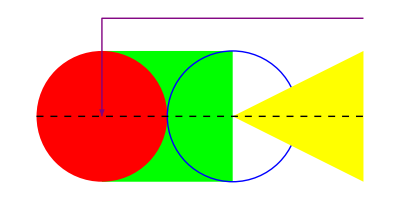
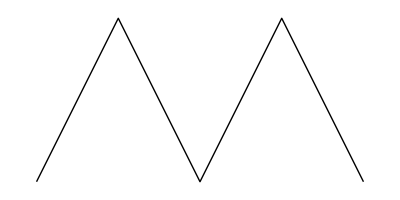
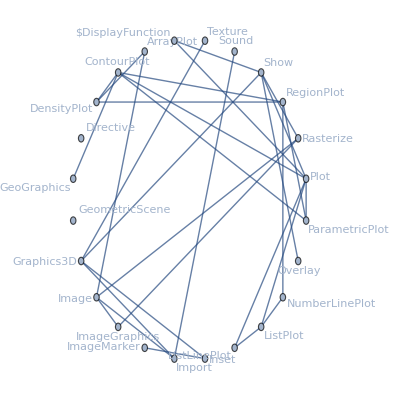
attributes | {Protected,ReadProtected}
character count | 8
common option values | {Epilog→{},Method→{{"AxesInFront"->False},{"FrameInFront"->False},{"GridLinesInFront"->True},{"TransparentPolygonMesh"->True}}}
date introduced | Day: Thu 23 Jun 1988
date last modified | Day: Wed 9 Jul 2014
dates modified | {Day: Tue 3 Sep 1996,Day: Tue 1 May 2007,Day: Tue 18 Nov 2008,Day: Mon 15 Nov 2010,Day: Wed 9 Jul 2014}
documentation basic examples | {{Use lines, polygons, circles, etc. to build up a graphics image:,Graphics[{Thick,Green,Rectangle[{0,-1},{2,1}],Red,Disk[],Blue,Circle[{2,0}],Yellow,Polygon[{{2,0},{4,1},{4,-1}}],Purple,Arrowheads[Large],Arrow[{{4,3/2},{0,3/2},{0,0}}],Black,Dashed,Line[{{-1,0},{4,0}}]}],-Graphics-}}
documentation example counts | {BasicExamples→2,Scope→13,GeneralizationsExtensions→0,Options→68,Applications→1,PropertiesRelations→5,PossibleIssues→0,InteractiveExamples→0,NeatExamples→2}
documentation example inputs | {BasicExamples→{{Graphics[{Thick,Green,Rectangle[{0,-1},{2,1}],Red,Disk[],Blue,Circle[{2,0}],Yellow,Polygon[{{2,0},{4,1},{4,-1}}],Purple,Arrowheads[Large],Arrow[{{4,3/2},{0,3/2},{0,0}}],Black,Dashed,Line[{{-1,0},{4,0}}]}]},{Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling→Axis],GraphPlot[Table[i→Mod[i^2,102],{i,0,102}]],ReliefPlot[Table[i+Sin[i^2+j^2],{i,-4,4,.03},{j,-4,4,.03}],ColorFunction→SunsetColors]}},Scope→{{Graphics[{Red,Disk[],Green,Rectangle[{0,0},{2,2}],Blue,Disk[{2,2}]}]},{Graphics[Polygon[{{0,0},{1,1},{0,1},{1,0}}]]},{v=Table[15{Cos[t],Sin[t]},{t,0,4Pi,4Pi/5}];,Graphics[GraphicsComplex[v,{Point[{1,2,3,4,5,6}],Green,Line[{1,2,3,4,5,6}]}]]},{Graphics[{Circle[],Inset[x^2+y^2==1,{0,0}]}]},{{Graphics[{Red,Disk[]}],Graphics[{Green,Disk[],Yellow,Opacity[.7],Disk[{0,1}]}],
Graphics[{Hue[2/3,1/2,1],Rectangle[]}]}},{{Graphics[{Blue,Arrow[{{0,0},{2,1}}]}],Graphics[{Thick,Blue,Line[{{0,0},{2,1}}]}],Graphics[{Dashed,Red,Arrow[{{0,0},{2,1}}]}],Graphics[{Thick,Dashed,Red,Line[{{0,0},{2,1}}]}]},{Graphics[{Pink,Rectangle[]}],Graphics[{EdgeForm[Thick],Pink,Rectangle[]}],Graphics[{EdgeForm[Dashed],Pink,Rectangle[]}],Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,Rectangle[]}]}},{{Graphics[{Dashed,Red,Arrowheads[{-.1,.1}],Arrow[{{0,0},{2,1}}]}],Graphics[{Blue,PointSize[Large],Point[{{0,0},{1,1/2},{2,1}}]}]}},{Graphics[{Style[Disk[],Pink],Style[Rectangle[{2,-1},{4,1}],Blue]}]},{Graphics[{Pink,Disk[],{Blue,Disk[{1,0}]},Disk[{2,0}]}]},{Graphics[Rectangle[{0,4},{10,6}],Frame→True,PlotRange→{{0,10},{0,10}}]},{Graphics[Rectangle[Scaled[{0,.4}],Scaled[{1,.6}]],Frame→True,PlotRange→{{0,10},{0,10}}]},{Graphics[Rectangle[ImageScaled[{0,.4}],ImageScaled[{1,.6}]],Frame→True,PlotRange→{{0,10},{0,10}}]},{Graphics[Rectangle[Offset[{10,20},{0,0}],Offset[{-10,-20},{1,1}]],Frame→True]}},GeneralizationsExtensions→{},Options→{{Table[Graphics[{Inset[Graphics[Circle[],ImageSize→30,AlignmentPoint→{a,0}],Center]},ImageSize→70,Axes→True,Ticks→None],{a,{-1,0,1}}],Table[Graphics[{Inset[Graphics[Circle[],ImageSize→30,AlignmentPoint→{0,a}],Center]},ImageSize→70,Axes→True,Ticks→None],{a,{-1,0,1}}]},{Table[Graphics[Circle[],AspectRatio→1/k],{k,1,3}]},{Graphics[Circle[],Axes→True]},{Graphics[Circle[],Axes→{False,True}]},{Graphics[Circle[],Axes→True,AxesLabel→y]},{Graphics[Circle[],Axes→True,AxesLabel→{x,y}]},{Graphics[Circle[],Axes→True,AxesOrigin→Automatic]},{Graphics[Circle[],Axes→True,AxesOrigin→{0,-1}]},{Graphics[Circle[],Axes→True,AxesStyle→Directive[Orange,12]],Graphics[Circle[],Axes→True,AxesStyle→{Directive[Dashed,Red],Blue}]},{Graphics[Circle[],Background→LightBlue]},{{x,Graphics[Circle[],ImageSize→50,BaselinePosition→Center],y}},{Table[{x,Graphics[Circle[],BaselinePosition→Scaled[b],ImageSize→50]},{b,{0,0.5,1}}]},{{x,Graphics[Circle[],Axes→True,BaselinePosition→Axis],y},{x,Graphics[Circle[{0,1}],Axes→True,BaselinePosition→Axis],y}},{Graphics[{Circle[{0,0},1],Disk[{3,0},1]},BaseStyle→Blue]},{Graphics[{Circle[{0,0},1],Disk[{3,0},1]},BaseStyle→{Green,Thick,EdgeForm[Dashed]}]},{Graphics[{Pink,Disk[],Rectangle[{2,-1},{4,1}]},ContentSelectable→True]},{Graphics[{Pink,Disk[],Rectangle[{2,-1},{4,1}]},ContentSelectable→False]},{Graphics[{Pink,Disk[],Rectangle[{2,-1},{4,1}]},ContentSelectable→Automatic]},{Graphics[{Pink,Disk[]},Axes→True,Epilog→{Blue,Disk[{0,0},.4]}]},{Graphics[{Circle[],Text[Style[x^2+y^2==1,20]]}]},{Graphics[{Circle[],Text[Style[x^2+y^2==1,20]]},FormatType→StandardForm]},{Graphics[Circle[],Axes→True,AxesLabel→{Cos[θ],Sin[θ]},FormatType→StandardForm]},{Graphics[Circle[],Frame→True]},{Graphics[Circle[],Frame→{{True,True},{False,False}}]},{Graphics[Circle[],Frame→True,FrameLabel→{x,y}],Graphics[Circle[],Frame→True,FrameLabel→{{a,b},{c,d}}]},{Graphics[Circle[],Frame→True,FrameStyle→Directive[Thick,Gray]]},{Graphics[Circle[],Frame→True,FrameStyle→{{Thick,Directive[Thick,Dashed]},{Blue,Red}}]},{Graphics[Circle[],Frame→True,FrameTicks->None],Graphics[Circle[],Frame→True,FrameTicks→Automatic]},{Graphics[Circle[],Frame→True,FrameTicks→{{None,Automatic},{Automatic,None}}]},{Graphics[{},Frame→True,FrameTicksStyle→Directive[Orange,12]]},{Graphics[{},Frame→True,FrameTicks→All,FrameTicksStyle→{{Black,Blue},{Red,Green}}]},{Graphics[Circle[],GridLines→Automatic]},{Graphics[Circle[],Axes→True,GridLines→{{-1,1},{-1,1}}]},{Graphics[Circle[],Axes→True,GridLines→{{{-1,Orange},{-.5,Dotted},{.5,Dotted},{1,Orange}},{-1,{-.5,Dotted},{.5,Dotted},1}}]},{Graphics[Circle[],Axes→True,GridLines→Automatic,GridLinesStyle→Directive[Red,Dotted]]},{Framed[Graphics[Disk[]]]},{Framed[Graphics[Disk[],ImageMargins→20]]},{Framed[Graphics[Disk[],ImageMargins→{{5,10},{20,30}}]]},{Graphics[{Thickness[.3],Pink,Circle[]},ImagePadding→None,Frame→True,FrameLabel→{x,y}]},{Framed[Graphics[{Thickness[.3],Pink,Circle[]},ImagePadding→All,Frame→True,FrameLabel→{x,y}],FrameMargins→0]},{Framed[Graphics[{Thickness[.3],Pink,Circle[]},ImagePadding→40,Frame→True]]},{Framed[Graphics[{Thickness[.2],Pink,Circle[]},ImagePadding→{{40,10},{20,5}},Frame→True]]},{Table[Graphics[Circle[],ImageSize→s],{s,{Tiny,Small}}]},{{Graphics[Circle[],ImageSize→100],Graphics[Circle[{0,0},{1,2}],ImageSize→100]}},{{Graphics[Circle[],ImageSize→{100,100}],Graphics[Circle[{0,0},{1,2}],ImageSize→{100,100}]}},{Graphics[Circle[],Axes→True,AxesLabel→{x,y},LabelStyle→Orange]},{Graphics[{Red,Table[Disk[{i,i}],{i,-1,1}]},Axes→True,Method→{AxesInFront→False}],Graphics[{Red,Polygon[{{0.5,0},{.5,1},{-.5,1}}]},Frame→True,PlotRange→{{0,1},{0,1}}],Show[%, Method→{FrameInFront→False}],Graphics[{Green,PointSize[.6],Point[{0,0}]},GridLines→Automatic,Method→{GridLinesInFront→True}],Graphics[{Blue,Opacity[0.2],EdgeForm[None],
Polygon[{{{0,0},{0,1},{1,0}},{{1,1},{0,1},{1,0}}}]}],Show[%,Method→{TransparentPolygonMesh→True}]},{Graphics[Circle[],PlotLabel→x^2+y^2==1]},{Graphics[Circle[],PlotLabel→Style[Framed[x^2+y^2==1],16,Red,Background→Yellow]]},{Graphics[{Pink,Disk[{0,0},5]},Frame→True,PlotRange→All]},{Graphics[{Pink,Disk[]},PlotRange→{{-1,1},{0,1}},Frame→True],Graphics[{Pink,Disk[]},PlotRange→{{-1,1},{0,1}},PlotRangeClipping→True,Frame→True]},{Graphics[{Pink,Disk[{0,0},5]},Frame→True,PlotRange→4]},{Graphics[{Pink,Disk[{0,0},5]},Frame→True,PlotRange→4,PlotRangeClipping→False]},{Graphics[{Pink,Disk[{0,0},5]},Frame→True,PlotRange→4,PlotRangeClipping→True]},{Graphics[{Pink,Rectangle[]},PlotRangePadding→1,Frame→True]},{Graphics[{Pink,Rectangle[]},PlotRangePadding→Scaled[0.1],Frame→True]},{Graphics[{Pink,Rectangle[]},PlotRangePadding→{{0.5,1},{0.3,0.3}},Frame→True]},{Graphics[{Pink,Disk[]},Frame→True,FrameTicks→False,Background→LightBlue]},{Graphics[{Pink,Disk[]},Frame→True,FrameTicks→False,PlotRegion→{{0.25,0.75},{0.25,0.75}},Background→LightBlue]},{Graphics[{Pink,Disk[]},Frame→True,FrameTicks→False,ImagePadding→30,Background→LightBlue]},{bg=Graphics[Polygon[{{0,0},{1,0},{1,1},{0,1}},VertexColors→{Orange,Orange,White,White}],AspectRatio→Full];,Graphics[Circle[],Prolog→Inset[bg,Scaled[{0,0}],Scaled[{0,0}]]],Plot[Sin[x],{x,0,10},Prolog→Inset[bg,Scaled[{0,0}],Scaled[{0,0}],Scaled[{1,1}]]]},{Graphics[Circle[],Frame→True,FrameLabel→{None,y axis},RotateLabel→True]},{Graphics[Circle[],Frame→True,FrameLabel→{None,y axis},RotateLabel→False]},{Graphics[Circle[],Axes→True,Ticks→None]},{Graphics[Circle[],Axes→True,Ticks→Automatic]},{Graphics[Circle[{0,0},3],Ticks→{{1,2,3},{1,3}},Axes→True]},{Graphics[Circle[],Axes→True,TicksStyle→Directive[Red,Bold]]},{Graphics[Circle[],Axes→True,TicksStyle→{Directive[Red,Bold],Directive[Blue,12]}]}},Applications→{{pts=Table[{Cos[2n π/9],Sin[2 n π/9]},{n,0,8}];,Graphics[{Opacity[0.7],Red,Line[Tuples[pts,2]],Blue,PointSize[0.05],Point[pts]}]}},PropertiesRelations→{{Graphics[Disk[]],InputForm[%]},{makeDashed[ g_Graphics ]:=g/.l_Line:>{Dashed,l},makeDashed[-Graphics-]},{ParametricPlot[{(v+u) Cos[u],(v+u) Sin[u]},{u,0,4Pi},{v,0,5},Mesh→False],ContourPlot[y+Sin[x^2+3y],{x,-3,3},{y,-3,3},ColorFunction→Rainbow]},{CountryData[World,Shape],GraphData[DoubleStarSnark]},{First@Import[ExampleData/mathematica.pdf],Import[ExampleData/coneflower.jpg, Graphics]}},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{{Dynamic@Module[{hour,min,sec,ht,mt,st},Clock[];{hour,min,sec}=Take[DateList[],-3];ht=Pi/2-2Pi hour/12-2Pi min/720;mt=Pi/2-2Pi min/60;st=Pi/2-2Pi Floor[sec]/60;Graphics[{Arrowheads[0.1],Arrow[{{0,0},0.6{Cos[ht],Sin[ht]}}],Arrow[{{0,0},0.85{Cos[mt],Sin[mt]}}],Line[{{0,0},0.85{Cos[st],Sin[st]}}],PointSize[Medium],Table[Point[0.9{Cos[i],Sin[i]}],{i,0,2Pi,Pi/6}],Point[{0,0}],Circle[]}]]},{Graphics[Table[{Hue[t/20],Circle[{Cos[2Pi t/20],Sin[2Pi t/20]}]},{t,20}]]}}}
documentation example text | {BasicExamples→{{Use lines, polygons, circles, etc. to build up a graphics image:},{Use plot functions to automatically create Graphics from different types of data: }},Scope→{{Graphics primitives are drawn in the order in which they are given in Graphics:},{Polygons can fold over themselves:},{Vertices can be shared by using GraphicsComplex:},{Inset an expression in a graphic:},{Directives can specify color and opacity of faces:},{Colors, thickness, and dashing directives affect lines, arrows, and edges:},{Some primitives have special directives to specify various properties:},{Directives can be applied to individual objects using Style:},{Graphics directives remain in effect only until the end of the list that contains them:},{Use an ordinary coordinate system:},{Specify coordinates by fractions of the plot range:},{Specify coordinates by fractions of the whole image:},{Offset coordinates by printer's points:}},GeneralizationsExtensions→{},Options→{{Specify the coordinates within Inset to be aligned with the center of the enclosing graphic:},{Use numerical values for AspectRatio:},{Draw all the axes:},{Draw the y axis but not the x axis:},{Place a label for the y axis:},{Specify a label for each axis:},{Determine where the axes cross automatically:},{Specify the axes' origin explicitly:},{Specify the overall axes style, including the ticks and the tick labels:,Specify the style of each axis:},{Specify a background color:},{Align the center of a graphic with the baseline of the text:},{Specify the baseline of a graphic as a fraction of the height by using Scaled:},{Use the axis of a graphic as the baseline:},{Set the starting style:},{Set multiple starting styles:},{Allow the individual graphics objects to be selectable by a single click:},{No individual object is selectable; the whole graphic appears as one object:},{The first click selects the whole graphic, and subsequent ones select individual objects:},{Draw a disk above the graphic, including the axes:},{By default, expressions are displayed using TraditionalForm in graphics:},{Display expressions using StandardForm:},{Labels are also affected by FormatType setting:},{Draw a frame around the whole graphic:},{Draw a frame on the left and the right edges:},{Specify frame labels for the bottom and the left edges:,Specify labels for each edge:},{Specify the overall frame style:},{Specify the style of each frame edge:},{Put a frame, but no ticks:,Tick mark labels on the bottom and the left frame edges:},{Frame ticks on the bottom and the right edges:},{Specify frame tick and frame tick label style:},{Specify frame tick style for each edge:},{Put grids across a 2D graphic:},{Draw grid lines at specific positions:},{Specify the style of each grid:},{Specify the overall grid style:},{Allow no margins outside of ImageSize:},{Have 20-point margins on all sides:},{Leave different margins on each side:},{Leave no padding outside of the plot range:},{Leave enough padding for all objects and labels that are present:},{Specify the same padding for all sides in printer's points:},{Specify different padding on each side:},{Use predefined symbolic sizes:},{Use an explicit image width:},{Use an explicit image width and height:},{Specify the overall style of all the label-like elements:},{Force axes to be behind drawing primitives:,By default, frames draw in front of graphics primitives:,Force the frame to draw behind graphics primitives:,Force grid lines to be rendered in front of graphics primitives:,By default, polygon meshes double-paint their edges for efficiency reasons:,The behavior can be turned off using the TransparentPolygonMesh method option:},{Display a label on the top of the graphic in TraditionalForm:},{Use Style and other typesetting functions to modify how the label appears:},{Display all objects:},{Explicitly choose x and y ranges:,Force clipping at the PlotRange: },{PlotRange->s is equivalent to PlotRange->{{-s,s},{-s,s}}:},{Allow graphics objects to spread beyond PlotRange:},{Clip all graphics objects at PlotRange:},{Include 1 coordinate unit of padding on all sides:},{Include padding using Scaled coordinates: },{Specify different padding on each side:},{The contents of a graphic use the whole region:},{Limit the contents of the graphic to the middle half of the region in each direction:},{ImagePadding can also be used to add padding around a graphic:},{Define a simple graphic to use as a background:,Use it in multiple graphics:},{Specify that vertical frame labels should be rotated:},{Specify that vertical frame labels should not be rotated:},{Draw the axes but no tick marks:},{Place tick marks automatically:},{Draw tick marks at the specific positions:},{Specify the styles of the ticks and tick labels:},{Specify the styles of x and y axis ticks separately:}},Applications→{{Draw a complete graph with 9 vertices:}},PropertiesRelations→{{The StandardForm of Graphics is its rendered form:,The InputForm is the textual expression form:},{Graphics can be used as input to functions: },{Two-dimensional plot functions return Graphics:},{Several integrated data sources return Graphics:},{Many Import and Export formats support Graphics:}},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{{Display an analog clock with current system time:},{Digital dahlias:}}}
entity classes | {}
eponymous people | {}
equal-precedence symbols | Missing[NotApplicable]
external links | {Fast Introduction for Programmers: Graphics→http://www.wolfram.com/language/fast-introduction-for-programmers/graphics/}
frequencies of usage | {All→0.000574249,StackExchange→0.00205678,TypicalProductionCode→0.00141163,WolframAlphaCodebase→0.000162146,WolframDemonstrations→0.00266587,WolframDocumentation→0.00331944}
full version introduced | 1
full version last modified | 10
full versions modified | {3,6,7,8,10}
functionality areas | {BasicSymbols}
symbol background | Missing[NotAvailable]
keyboard shortcuts | Missing[NotAvailable]
link trails | {{guide/WolframRoot,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/EarthSciencesDataAndComputation,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DateAndTime,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DiscreteCalculus,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DiscreteCalculus,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/EarthSciencesDataAndComputation,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/SolidGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/SolidGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/PlaneGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/PlaneGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/CloudFunctionsAndDeployment,guide/CloudExecutionMetadata,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/CreatingAnInstantAPI,guide/CloudExecutionMetadata,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/CreatingFormsAndApps,guide/CloudExecutionMetadata,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DiscreteMathematics,guide/DiscreteCalculus,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DiscreteMathematics,guide/DiscreteCalculus,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/Finance,guide/DateAndTime,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeographicData,guide/EarthSciencesDataAndComputation,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/InternetAndWebRelatedData,guide/CloudExecutionMetadata,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/MeshRegions,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/MeshRegions,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PeopleAndHistory,guide/DateAndTime,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PhysicsAndChemistryDataAndComputation,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PhysicsAndChemistryDataAndComputation,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTime,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics}}
memberships | {}
name | Graphics
option names | {AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,ContentSelectable,CoordinatesToolOptions,DisplayFunction,Epilog,FormatType,Frame,FrameLabel,FrameStyle,FrameTicks,FrameTicksStyle,GridLines,GridLinesStyle,ImageMargins,ImagePadding,ImageSize,ImageSizeRaw,LabelStyle,Method,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}
options | {AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Method→Automatic,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}
plaintext usage | Graphics[primitives, options] represents a two-dimensional graphical image.
precedence ranks | Missing[NotApplicable]
ranks of usage | {All→72,StackExchange→47,TypicalProductionCode→66,WolframAlphaCodebase→111,WolframDemonstrations→38,WolframDocumentation→24}
related entities | Missing[NotAvailable]
related guide pages | {Plane Geometrypaclet:guide/PlaneGeometry,Symbolic Graphics Languagepaclet:guide/SymbolicGraphicsLanguage,Polygonspaclet:guide/Polygons,Polygonspaclet:guide/PolygonsNew,Polygons & Polyhedrapaclet:guide/PolygonsAndPolyhedra,Popular Functionspaclet:guide/PopularFunctions,Graphics & Visualizationpaclet:guide/GraphicsAndVisualization,WDF (Wolfram Data Framework)paclet:guide/WDFWolframDataFramework}
related symbols | {Plot,ListPlot,ListLinePlot,ParametricPlot,DensityPlot,ArrayPlot,RegionPlot,ContourPlot,Show,Graphics3D,Image,Import,GeometricScene,Sound}
relationship community graph | -Graphics-
relationship graph | -Graphics-
short notations | Missing[NotApplicable]
subject classifications | Missing[NotAvailable]
symbols linking to | {Directive,GeoGraphics,GeometricScene,Graphics3D,Image,ImageGraphics,ImageMarker,Inset,ListLinePlot,ListPlot,NumberLinePlot,Overlay,ParametricPlot,Plot,Rasterize,Sound,Texture,$DisplayFunction}
symbols using as attribute | {}
symbols using as option | {}
text strings | {Graphics[primitives,options] represents a two-dimensional graphical image.,Graphics is displayed in StandardForm as a graphical image. In InputForm, it is displayed as an explicit list of primitives.,The following graphics primitives can be used:139436543,The following graphics directives can be used:362437821,The following wrappers can be used at any level:,The following options can be given:,Nested lists of graphics constructs can be given. Directive specifications such as GrayLevel remain in effect only until the end of the list that contains them.415812662,Style[obj,opts] can be used to apply the options or directives opts to obj.59755747,The following Method options can be given:,The settings for BaseStyle are appended to the default style typically given by the "Graphics" style in the current stylesheet. The settings for AxesStyle, LabelStyle, etc. are appended to the default styles given for "GraphicsAxes", "GraphicsLabel", etc.,Graphics[] gives an empty graphic with the default image size.,Use lines, polygons, circles, etc. to build up a graphics image:,Use plot functions to automatically create Graphics from different types of data:,Graphics primitives are drawn in the order in which they are given in Graphics:,Polygons can fold over themselves:,Vertices can be shared by using GraphicsComplex:,Inset an expression in a graphic:,Directives can specify color and opacity of faces:,Colors, thickness, and dashing directives affect lines, arrows, and edges:,Some primitives have special directives to specify various properties:,Directives can be applied to individual objects using Style:,Graphics directives remain in effect only until the end of the list that contains them:,Use an ordinary coordinate system:,Specify coordinates by fractions of the plot range:,Specify coordinates by fractions of the whole image:,Offset coordinates by printer's points:,Specify the coordinates within Inset to be aligned with the center of the enclosing graphic:,Use numerical values for AspectRatio:,Draw all the axes:,Draw the y axis but not the x axis:,Place a label for the y axis:,Specify a label for each axis:,Determine where the axes cross automatically:,Specify the axes' origin explicitly:,Specify the overall axes style, including the ticks and the tick labels:,Specify the style of each axis:,Specify a background color:,Align the center of a graphic with the baseline of the text:,Specify the baseline of a graphic as a fraction of the height by using Scaled:,Use the axis of a graphic as the baseline:,Set the starting style:,Set multiple starting styles:,Allow the individual graphics objects to be selectable by a single click:,No individual object is selectable; the whole graphic appears as one object:,The first click selects the whole graphic, and subsequent ones select individual objects:,Draw a disk above the graphic, including the axes:,By default, expressions are displayed using TraditionalForm in graphics:,Display expressions using StandardForm:,Labels are also affected by FormatType setting:,Draw a frame around the whole graphic:,Draw a frame on the left and the right edges:,Specify frame labels for the bottom and the left edges:,Specify labels for each edge:,Specify the overall frame style:,Specify the style of each frame edge:,Put a frame, but no ticks:,Tick mark labels on the bottom and the left frame edges:,Frame ticks on the bottom and the right edges:,Specify frame tick and frame tick label style:,Specify frame tick style for each edge:,Put grids across a 2D graphic:,Draw grid lines at specific positions:,Specify the style of each grid:,Specify the overall grid style:,Allow no margins outside of ImageSize:,Have 20-point margins on all sides:,Leave different margins on each side:,Leave no padding outside of the plot range:,Leave enough padding for all objects and labels that are present:,Specify the same padding for all sides in printer's points:,Specify different padding on each side:,Use predefined symbolic sizes:,Use an explicit image width:,Use an explicit image width and height:,Specify the overall style of all the label-like elements:,Force axes to be behind drawing primitives:,By default, frames draw in front of graphics primitives:,Force the frame to draw behind graphics primitives:,Force grid lines to be rendered in front of graphics primitives:,By default, polygon meshes double-paint their edges for efficiency reasons:,The behavior can be turned off using the "TransparentPolygonMesh" method option:,Display a label on the top of the graphic in TraditionalForm:,Use Style and other typesetting functions to modify how the label appears:,Display all objects:,Explicitly choose x and y ranges:,Force clipping at the PlotRange:,PlotRange->s is equivalent to PlotRange->{{-s,s},{-s,s}}:,Allow graphics objects to spread beyond PlotRange:,Clip all graphics objects at PlotRange:,Include 1 coordinate unit of padding on all sides:,Include padding using Scaled coordinates:,Specify different padding on each side:,The contents of a graphic use the whole region:,Limit the contents of the graphic to the middle half of the region in each direction:,ImagePadding can also be used to add padding around a graphic:,Define a simple graphic to use as a background:,Use it in multiple graphics:,Specify that vertical frame labels should be rotated:,Specify that vertical frame labels should not be rotated:,Draw the axes but no tick marks:,Place tick marks automatically:,Draw tick marks at the specific positions:,Specify the styles of the ticks and tick labels:,Specify the styles of x and y axis ticks separately:,Draw a complete graph with 9 vertices:,The StandardForm of Graphics is its rendered form:,The InputForm is the textual expression form:,Graphics can be used as input to functions:,Two-dimensional plot functions return Graphics:,Several integrated data sources return Graphics:,Many Import and Export formats support Graphics:,Display an analog clock with current system time:,Digital dahlias:}
timeline | -Graphics-
timeline events | Interval[{Day: Thu 23 Jun 1988,Day: Wed 9 Jul 2014}]Graphics
translations | {Simplified Chinese→图形,Traditional Chinese→圖形,French→graphique,German→Graphik,Modern Greek→γραφικά,Japanese→グラフィックス,Korean→그래픽,Lithuanian→grafika,Polish→grafika,Portuguese→representação gráfica,Russian→графика,Spanish→gráfico,Ukrainian→графіка,Vietnamese→đồ họa}
typeset usage | Graphics[primitives,options] represents a two-dimensional graphical image. 
URL | http://reference.wolfram.com/language/ref/Graphics.html
version introduced | 1
version last modified | 10
versions modified | {3,6,7,8,10}
Wolfram documentation link | Graphicspaclet:ref/Graphics

```mathematica
Grid[MapThread[{#1,#2}&,{wlEntityProperties,graphicsWLProperties}],Frame->All]
```

```mathematica
simplePlot=Plot[2 x, {x,-2,2}];
```

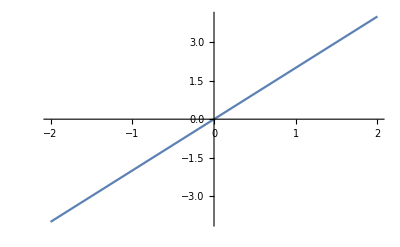

```mathematica
simplePlot
```

```mathematica
simplePlotFullForm = FullForm[simplePlot];
```

```mathematica
simplePlotInputForm = InputForm[simplePlot];
```

```mathematica
simplePlotFullForm
```

Graphics[List[List[List[List[],List[],Annotation[List[Directive[Opacity[1.],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]],Line[List[List[-2.,-4.],List[-1.99877,-3.99755],List[-1.99755,-3.99509],List[-1.99509,-3.99019],List[-1.99019,-3.98037],List[-1.98037,-3.96074],List[-1.96074,-3.92149],List[-1.92149,-3.84297],List[-1.83637,-3.67273],List[-1.75689,-3.51378],List[-1.67897,-3.35794],List[-1.59445,-3.18889],List[-1.51556,-3.03113],List[-1.43008,-2.86015],List[-1.34615,-2.6923],List[-1.26786,-2.53572],List[-1.18297,-2.36594],List[-1.10372,-2.20744],List[-1.02603,-2.05206],List[-0.941732,-1.88346],List[-0.863077,-1.72615],List[-0.777818,-1.55564],List[-0.694118,-1.38824],List[-0.616058,-1.23212],List[-0.531394,-1.06279],List[-0.452371,-0.904742],List[-0.366744,-0.733487],List[-0.282675,-0.56535],List[-0.204247,-0.408495],List[-0.119216,-0.238431],List[-0.0398244,-0.0796487],List[0.0380078,0.0760156],List[0.122444,0.244888],List[0.20124,0.40248],List[0.28664,0.57328],List[0.370481,0.740962],List[0.448681,0.897362],List[0.533485,1.06697],List[0.612649,1.2253],List[0.690254,1.38051],List[0.774463,1.54893],List[0.853031,1.70606],List[0.938204,1.87641],List[1.01774,2.03547],List[1.09571,2.19142],List[1.18029,2.36057],List[1.25922,2.51844],List[1.34476,2.68952],List[1.42874,2.85749],List[1.50708,3.01417],List[1.59203,3.18406],List[1.67133,3.34267],List[1.74908,3.49816],List[1.83343,3.66686],List[1.91214,3.82427],List[1.91351,3.82702],List[1.91488,3.82977],List[1.91763,3.83526],List[1.92312,3.84624],List[1.9341,3.86821],List[1.95607,3.91214],List[1.95744,3.91488],List[1.95881,3.91763],List[1.96156,3.92312],List[1.96705,3.9341],List[1.97803,3.95607],List[1.97941,3.95881],List[1.98078,3.96156],List[1.98353,3.96705],List[1.98902,3.97803],List[1.99039,3.98078],List[1.99176,3.98353],List[1.99451,3.98902],List[1.99588,3.99176],List[1.99725,3.99451],List[1.99863,3.99725],List[2.,4.]]]],"Charting`Private`Tag$70233#1"]]],List[]],List[Rule[DisplayFunction,Identity],Rule[Ticks,List[Automatic,Automatic]],Rule[AxesOrigin,List[0,0]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[DisplayFunction,Identity],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.05],Scaled[0.05]]]],Rule[PlotRangeClipping,True],Rule[ImagePadding,All],Rule[DisplayFunction,Identity],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[True,True]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],RuleDelayed[DisplayFunction,Identity],Rule[Frame,List[List[False,False],List[False,False]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[Method,List[Rule["DefaultBoundaryStyle",Automatic],Rule["DefaultGraphicsInteraction",List[Rule["Version",1.2],Rule["TrackMousePosition",List[True,False]],Rule["Effects",List[Rule["Highlight",List[Rule["ratio",2]]],Rule["HighlightPoint",List[Rule["ratio",2]]],Rule["Droplines",List[Rule["freeformCursorMode",True],Rule["placement",List[Rule["x","All"],Rule["y","None"]]]]]]]]],Rule["DefaultMeshStyle",AbsolutePointSize[6]],Rule["ScalingFunctions",None],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[List[-2,2],List[-4.,4.]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.02],Scaled[0.02]]]],Rule[Ticks,List[Automatic,Automatic]]]]

```mathematica
simplePlotInputForm
```

Graphics[{{{{}, {}, Annotation[{Directive[Opacity[1.], RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
      Line[{{-1.999999918367347, -3.999999836734694}, {-1.9987731283177614, -3.997546256635523}, {-1.997546338268176, -3.995092676536352}, 
       {-1.995092758169005, -3.99018551633801}, {-1.9901855979706633, -3.9803711959413266}, {-1.9803712775739797, -3.9607425551479594}, 
       {-1.9607426367806124, -3.921485273561225}, {-1.9214853551938782, -3.8429707103877564}, {-1.8363665716581652, -3.6727331433163304}, 
       {-1.7568884657193913, -3.5137769314387826}, {-1.6789694047244954, -3.357938809448991}, {-1.594446123367355, -3.18889224673471}, 
       {-1.515563519607154, -3.031127039214308}, {-1.4300766954847084, -2.860153390969417}, {-1.3461489163061406, -2.6922978326122813}, 
       {-1.2678618147245122, -2.5357236294490244}, {-1.1829704927806393, -2.3659409855612785}, {-1.1037198484337056, -2.2074396968674113}, 
       {-1.0260282490306498, -2.0520564980612996}, {-0.9417324292653497, -1.8834648585306994}, {-0.8630772870969888, -1.7261545741939777}, 
       {-0.7778179245663834, -1.5556358491327669}, {-0.6941176069796561, -1.3882352139593122}, {-0.6160579669898679, -1.2321159339797358}, 
       {-0.5313941066378353, -1.0627882132756705}, {-0.4523709238827418, -0.9047418477654836}, {-0.3667435207654039, -0.7334870415308078}, 
       {-0.282675162591944, -0.565350325183888}, {-0.20424748201542325, -0.4084949640308465}, {-0.11921558107665804, -0.23843116215331608}, 
       {-0.03982435773483204, -0.07964871546966408}, {0.03800782066311598, 0.07601564132623197}, {0.12244421942330848, 0.24488843884661696}, 
       {0.20123994058656178, 0.40247988117312355}, {0.28663988211205954, 0.5732797642241191}, {0.3704807786936793, 0.7409615573873586}, 
       {0.44868099767835984, 0.8973619953567197}, {0.533485437025285, 1.06697087405057}, {0.6126491987752708, 1.2252983975505416}, 
       {0.6902539155813786, 1.3805078311627572}, {0.7744628527497309, 1.5489257054994618}, {0.853031112321144, 1.706062224642288}, 
       {0.9382035922548017, 1.8764071845096033}, {1.01773539459152, 2.03547078918304}, {1.0957081519843606, 2.191416303968721}, 
       {1.1802851297394454, 2.360570259478891}, {1.2592214298975912, 2.5184428597951825}, {1.3447619504179815, 2.689523900835963}, 
       {1.4287434259944938, 2.8574868519889876}, {1.507084223974067, 3.014168447948134}, {1.5920292423158844, 3.1840584846317688}, 
       {1.6713335830607627, 3.3426671661215255}, {1.749078878861763, 3.498157757723526}, {1.8334283950250079, 3.6668567900500157}, 
       {1.9121372335913134, 3.8242744671826268}, {1.913510088040939, 3.827020176081878}, {1.9148829424905645, 3.829765884981129}, 
       {1.9176286513898155, 3.835257302779631}, {1.9231200691883177, 3.8462401383766354}, {1.9341029047853218, 3.8682058095706435}, 
       {1.9560685759793301, 3.9121371519586603}, {1.9574414304289558, 3.9148828608579116}, {1.9588142848785812, 3.9176285697571624}, 
       {1.9615599937778323, 3.9231199875556646}, {1.9670514115763345, 3.934102823152669}, {1.9780342471733385, 3.956068494346677}, 
       {1.979407101622964, 3.958814203245928}, {1.9807799560725896, 3.961559912145179}, {1.9835256649718405, 3.967051329943681}, 
       {1.9890170827703426, 3.9780341655406852}, {1.9903899372199683, 3.9807798744399365}, {1.9917627916695937, 3.9835255833391874}, 
       {1.9945085005688448, 3.9890170011376895}, {1.9958813550184704, 3.991762710036941}, {1.9972542094680958, 3.9945084189361917}, 
       {1.9986270639177213, 3.9972541278354425}, {1.999999918367347, 3.999999836734694}}]}, "Charting`Private`Tag$70233#1"]}}, {}}, 
 {DisplayFunction -> Identity, Ticks -> {Automatic, Automatic}, AxesOrigin -> {0, 0}, 
  FrameTicks -> {{Automatic, Automatic}, {Automatic, Automatic}}, GridLines -> {None, None}, DisplayFunction -> Identity, 
  PlotRangePadding -> {{Scaled[0.02], Scaled[0.02]}, {Scaled[0.05], Scaled[0.05]}}, PlotRangeClipping -> True, ImagePadding -> All, 
  DisplayFunction -> Identity, AspectRatio -> GoldenRatio^(-1), Axes -> {True, True}, AxesLabel -> {None, None}, AxesOrigin -> {0, 0}, 
  DisplayFunction :> Identity, Frame -> {{False, False}, {False, False}}, FrameLabel -> {{None, None}, {None, None}}, 
  FrameTicks -> {{Automatic, Automatic}, {Automatic, Automatic}}, GridLines -> {None, None}, GridLinesStyle -> Directive[GrayLevel[0.5, 0.4]], 
  Method -> {"DefaultBoundaryStyle" -> Automatic, "DefaultGraphicsInteraction" -> {"Version" -> 1.2, "TrackMousePosition" -> {True, False}, 
      "Effects" -> {"Highlight" -> {"ratio" -> 2}, "HighlightPoint" -> {"ratio" -> 2}, 
        "Droplines" -> {"freeformCursorMode" -> True, "placement" -> {"x" -> "All", "y" -> "None"}}}}, 
    "DefaultMeshStyle" -> AbsolutePointSize[6], "ScalingFunctions" -> None, "CoordinatesToolOptions" -> 
     {"DisplayFunction" -> ({(Identity[#1] & )[#1[[1]]], (Identity[#1] & )[#1[[2]]]} & ), 
      "CopiedValueFunction" -> ({(Identity[#1] & )[#1[[1]]], (Identity[#1] & )[#1[[2]]]} & )}}, 
  PlotRange -> {{-2, 2}, {-3.999999836734694, 3.999999836734694}}, PlotRangeClipping -> True, 
  PlotRangePadding -> {{Scaled[0.02], Scaled[0.02]}, {Scaled[0.02], Scaled[0.02]}}, Ticks -> {Automatic, Automatic}}]

```mathematica
anotherPlot=-Graphics-;
```

```mathematica
anotherPlot//FullForm
```

Graphics[List[RGBColor[0,1,0],Thickness[Large],Rectangle[List[0,-1],List[2,1]],List[RGBColor[1,0,0],Disk[List[0,0]]],List[RGBColor[0,0,1],Circle[List[2,0]]],List[RGBColor[1,1,0],Polygon[List[List[2,0],List[4,1],List[4,-1]]]],List[RGBColor[0.5,0,0.5],Arrowheads[Large],Arrow[List[List[4,Rational[3,2]],List[0,Rational[3,2]],List[0,0]]],List[GrayLevel[0],Dashing[List[Small,Small]],Line[List[List[-1,0],List[4,0]]]]]]]

```mathematica
anotherPlot//InputForm
```

Graphics[{RGBColor[0, 1, 0], Thickness[Large], Rectangle[{0, -1}, {2, 1}], {RGBColor[1, 0, 0], Disk[{0, 0}]}, 
  {RGBColor[0, 0, 1], Circle[{2, 0}]}, {RGBColor[1, 1, 0], Polygon[{{2, 0}, {4, 1}, {4, -1}}]}, 
  {RGBColor[0.5, 0, 0.5], Arrowheads[Large], Arrow[{{4, 3/2}, {0, 3/2}, {0, 0}}], {GrayLevel[0], Dashing[{Small, Small}], 
    Line[{{-1, 0}, {4, 0}}]}}}]

#### Getting every Wolfram Language symbol that is a graphic primitive

```mathematica
graphicsPrimitiveSymbols=Select[functionalityAreasOfAllWLSymbols,Count[Last@#,"GraphicsPrimitiveSymbols"]>0&];
```

```mathematica
graphicsSymbols=graphicsPrimitiveSymbols⟦All,1⟧
```

{AASTriangle,ASATriangle,AffineHalfSpace,AffineSpace,Annulus,Arrow,BSplineCurve,Ball,BezierCurve,CapsuleShape,Circle,Circumsphere,Cone,ConicHullRegion,Cube,Cuboid,Cylinder,DiskSegment,Dodecahedron,Ellipsoid,EmptyRegion,FilledCurve,FullRegion,GraphicsComplex,HalfLine,HalfPlane,HalfSpace,Hexahedron,Hyperplane,Icosahedron,InfiniteLine,InfinitePlane,Insphere,JoinedCurve,Octahedron,Parallelepiped,Parallelogram,Polyhedron,Prism,Rectangle,RegularPolygon,SASTriangle,SSSTriangle,ShellRegion,Simplex,Sphere,SphericalShell,StadiumShape,Tetrahedron,Triangle,Tube}

#### GraphicsPrimitiveQ function

```mathematica
GraphicsPrimitiveQ[string_String]:=GraphicsPrimitiveQ[string]=With[
{functionalities=Entity["WolframLanguageSymbol",string]@"FunctionalityAreas"},
Count[functionalities,"GraphicsPrimitiveSymbols"]>0
]
GraphicsPrimitiveQ[symbol_Symbol]:=GraphicsPrimitiveQ[symbol]=GraphicsPrimitiveQ[ToString@symbol]
GraphicsPrimitiveQ[expression_]:=GraphicsPrimitiveQ[Head@expression]

SetAttributes[GraphicsPrimitiveQ,Listable]
```

Some tests

```mathematica
GraphicsPrimitiveQ@EntityValue[graphicsSymbols,"Name"]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
GraphicsPrimitiveQ@{AASTriangle,ASATriangle,AffineTransform,Red,Green,Blue,Graphics,2+2}
```

{True,True,False,False,False,False,False,False}

#### Description and TranslatedDescription functions for GraphicsPrimitive

```mathematica
Description[expression_]:=Description[Head@expression]/;GraphicsPrimitiveQ@expression

SetAttributes[Description,Listable]
```

```mathematica
TranslatedDescription[expression_,language_String]:=TranslatedDescription[Head@expression,language]/;GraphicsPrimitiveQ@expression
TranslatedDescription[expression_]:=Description[Head@expression]/;GraphicsPrimitiveQ@expression

SetAttributes[TranslatedDescription,Listable]
```

Some tests

```mathematica
Description@{AASTriangle,ASATriangle,AffineTransform,Red,Green,Blue,Graphics,2+2}
```

{AASTriangle,ASATriangle,Affine Transform,Red,Light Green,Blue,Graphics,Description[4]}

```mathematica
TranslatedDescription@{AASTriangle,ASATriangle,AffineTransform,Red,Green,Blue,Graphics,2+2}
```

{Symbol,Symbol,TranslatedDescription[AffineTransform],Red,Light Green,Blue,TranslatedDescription[Graphics],TranslatedDescription[4]}

```mathematica
graphicsPrimitiveExamples={Tetrahedron[{{1,0,0},{1,0,1},{1,1,1},{0,0,1}}],Hexahedron[{{0,0,0},{1,0,0},{2,1,0},{1,1,0},{0,0,1},{1,0,1},{2,1,1},{1,1,1}}],
SASTriangle[1,Pi/2,2],
Arrow[{{1,0},{2,1},{3,0},{4,1}}],
Hyperplane[{2,1}],
Cuboid[{0.5,0.5,0.5}]};
```

```mathematica
primitivesDescriptionTest=MapThread[
{#1,#2,#3,#4}&,
{Description@graphicsPrimitiveExamples,
TranslatedDescription[graphicsPrimitiveExamples,"Spanish"],
TranslatedDescription[graphicsPrimitiveExamples,"Portuguese"],
TranslatedDescription[graphicsPrimitiveExamples,"Japanese"]}
];
```

```mathematica
Grid[primitivesDescriptionTest,Frame->All]
```

Tetrahedron | TranslatedDescription[Symbol,Spanish] | TranslatedDescription[Symbol,Portuguese] | TranslatedDescription[Symbol,Japanese]
Hexahedron | TranslatedDescription[Symbol,Spanish] | TranslatedDescription[Symbol,Portuguese] | TranslatedDescription[Symbol,Japanese]
Triangle | TranslatedDescription[Symbol,Spanish] | TranslatedDescription[Symbol,Portuguese] | TranslatedDescription[Symbol,Japanese]
Arrow | TranslatedDescription[Symbol,Spanish] | TranslatedDescription[Symbol,Portuguese] | TranslatedDescription[Symbol,Japanese]
Hyperplane | TranslatedDescription[Symbol,Spanish] | TranslatedDescription[Symbol,Portuguese] | TranslatedDescription[Symbol,Japanese]
Cuboid | TranslatedDescription[Symbol,Spanish] | TranslatedDescription[Symbol,Portuguese] | TranslatedDescription[Symbol,Japanese]

#### Description function for Graphics

```mathematica
Clear[ToGraphics]
ToGraphics[arg_]:=First@ToExpression@StringDelete[ToString[#,FormatType->StandardForm],"Global`"]&@arg
SetAttributes[ToGraphics,Listable]
```

```mathematica
Description[graphics_Graphics]:=Block[
{elements,primitives,sorted,descriptions},
elements=Flatten[List@@graphics];
primitives=Select[elements,(ColorQ@#||GraphicsPrimitiveQ@#)&];
sorted=Sort[#,ColorQ@#1&]&/@Partition[primitives,2];
descriptions=Description[#]&/@sorted;
Description[Graphics]<>": "<>ToString@Row[Row[#," "]&/@descriptions, ", "]<>"."
]
```

```mathematica
Description[graphics_Graphics]:=Block[
{elements,primitives,sorted,descriptions},
elements=Flatten[List@@graphics];
primitives=Select[elements,(ColorQ@#||GraphicsPrimitiveQ@#)&];
sorted=Sort[#,ColorQ@#1&]&/@Partition[primitives,2];
descriptions=ToLowerCase[Description[#]]&/@sorted;
"A graphic consisting of "<>ToString@Row[Row[#," "]&/@descriptions, ", "]<>"."
]
```

#### Testing Description function for Graphics

```mathematica
Description[Graphics[{Red,Rectangle[{0,0}],Blue,Rectangle[{0.5,0.5}]}]]
```

A graphic consisting of red rectangle, blue rectangle.

AASTriangle

```mathematica
ℛ=AASTriangle[Pi/6,Pi/3,1]; 
aasTriangles={Graphics[{Pink,ℛ}],Graphics[{EdgeForm[Thick],Pink,ℛ}],
Graphics[{EdgeForm[Dashed],Pink,ℛ}],
Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,ℛ}]};
```

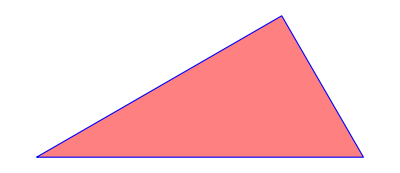
-Graphics- | Graphics[{RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {2, 0}, {3/2, Sqrt[3]/2}}]}] | A graphic consisting of light pink triangle.
-Graphics- | Graphics[{EdgeForm[Thickness[Large]], RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {2, 0}, {3/2, Sqrt[3]/2}}]}] | A graphic consisting of light pink triangle.
-Graphics- | Graphics[{EdgeForm[Dashing[{Small, Small}]], RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {2, 0}, {3/2, Sqrt[3]/2}}]}] | A graphic consisting of light pink triangle.
-Graphics- | Graphics[{EdgeForm[Directive[Thickness[Large], Dashing[{Small, Small}], RGBColor[0, 0, 1]]], RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {2, 0}, {3/2, Sqrt[3]/2}}]}] | A graphic consisting of light pink triangle.

```mathematica
aasTriangleTests={#,InputForm@#,Description@#}&/@aasTriangles;
Grid[aasTriangleTests,Frame->All]
```

ASATriangle

```mathematica
ℛ=ASATriangle[Pi/6,1,Pi/3];
asaTriangles={Graphics[{Pink,ℛ}],Graphics[{EdgeForm[Thick],Pink,ℛ}],Graphics[{EdgeForm[Dashed],Pink,ℛ}],Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,ℛ}]};
```

```mathematica
asaTriangleTests={#,InputForm@#,Description@#}&/@asaTriangles;
Grid[asaTriangleTests,Frame->All]
```

-Graphics- | Graphics[{RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {1, 0}, {3/4, Sqrt[3]/4}}]}] | A graphic consisting of light pink triangle.
-Graphics- | Graphics[{EdgeForm[Thickness[Large]], RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {1, 0}, {3/4, Sqrt[3]/4}}]}] | A graphic consisting of light pink triangle.
-Graphics- | Graphics[{EdgeForm[Dashing[{Small, Small}]], RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {1, 0}, {3/4, Sqrt[3]/4}}]}] | A graphic consisting of light pink triangle.
-Graphics- | Graphics[{EdgeForm[Directive[Thickness[Large], Dashing[{Small, Small}], RGBColor[0, 0, 1]]], RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {1, 0}, {3/4, Sqrt[3]/4}}]}] | A graphic consisting of light pink triangle.

AffineHalfSpace

```mathematica
affineHalfSpace=Graphics[{Red,AffineHalfSpace[{0,0},{{1,-1}},{1,1}]}];
```

```mathematica
affineHalfSpaceTest={affineHalfSpace,InputForm@affineHalfSpace,Description@affineHalfSpace};
Grid[{affineHalfSpaceTest},Frame->All]
```

-Graphics- | Graphics[{RGBColor[1, 0, 0], AffineHalfSpace[{0, 0}, {{1, -1}}, {1, 1}]}] | A graphic consisting of red affine half space.

AffineSpace

```mathematica
affineSpace=Graphics[{Green,AffineSpace[{0,0},{{1,-1}}]}];
```

```mathematica
affineSpaceTest={affineSpace,InputForm@affineSpace,Description@affineSpace};
Grid[{affineSpaceTest},Frame->All]
```

-Graphics- | Graphics[{RGBColor[0, 1, 0], AffineSpace[{0, 0}, {{1, -1}}]}] | A graphic consisting of light green affine space.

Annulus

```mathematica
annulus={Graphics[{Pink,Annulus[]}],Graphics[{EdgeForm[Thick],Pink,Annulus[]}],Graphics[{EdgeForm[Dashed],Pink,Annulus[]}],Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,Annulus[]}]};
```

```mathematica
annulusTests = {#,InputForm@#,Description@#}&/@annulus;
Grid[annulusTests,Frame->All]
```

-Graphics- | Graphics[{RGBColor[1, 0.5, 0.5], Annulus[{0, 0}, {1/2, 1}]}] | A graphic consisting of light pink annulus.
-Graphics- | Graphics[{EdgeForm[Thickness[Large]], RGBColor[1, 0.5, 0.5], Annulus[{0, 0}, {1/2, 1}]}] | A graphic consisting of light pink annulus.
-Graphics- | Graphics[{EdgeForm[Dashing[{Small, Small}]], RGBColor[1, 0.5, 0.5], Annulus[{0, 0}, {1/2, 1}]}] | A graphic consisting of light pink annulus.
-Graphics- | Graphics[{EdgeForm[Directive[Thickness[Large], Dashing[{Small, Small}], RGBColor[0, 0, 1]]], RGBColor[1, 0.5, 0.5], Annulus[{0, 0}, {1/2, 1}]}] | A graphic consisting of light pink annulus.

Arrow

```mathematica
a={Arrowheads[Large],Arrow[{{0,0},{1,.5}}]};
arrows={Graphics[{Dashed,Green,a}],Graphics[{Red,a}],Graphics[{Thick,Blue,a}],Graphics[{Thick,Dashed,Red,a}]};
```

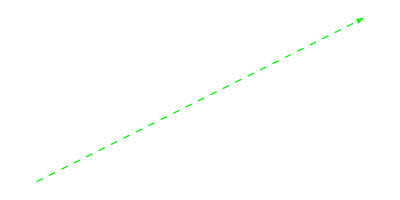
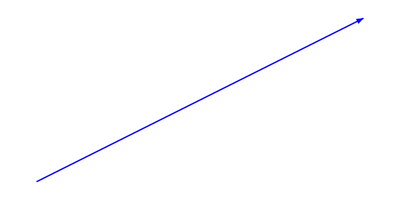
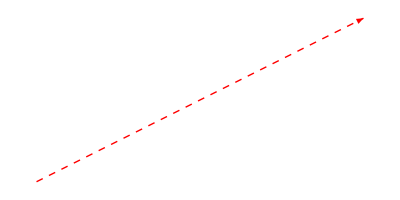
-Graphics- | Graphics[{Dashing[{Small, Small}], RGBColor[0, 1, 0], {Arrowheads[Large], Arrow[{{0, 0}, {1, 0.5}}]}}] | A graphic consisting of light green arrow.
-Graphics- | Graphics[{RGBColor[1, 0, 0], {Arrowheads[Large], Arrow[{{0, 0}, {1, 0.5}}]}}] | A graphic consisting of red arrow.
-Graphics- | Graphics[{Thickness[Large], RGBColor[0, 0, 1], {Arrowheads[Large], Arrow[{{0, 0}, {1, 0.5}}]}}] | A graphic consisting of blue arrow.
-Graphics- | Graphics[{Thickness[Large], Dashing[{Small, Small}], RGBColor[1, 0, 0], {Arrowheads[Large], Arrow[{{0, 0}, {1, 0.5}}]}}] | A graphic consisting of red arrow.

```mathematica
arrowTests={#,InputForm@#,Description@#}&/@arrows;
Grid[arrowTests,Frame->All]
```

```mathematica
graphicsSymbols
```

{AASTriangle,ASATriangle,AffineHalfSpace,AffineSpace,Annulus,Arrow,BSplineCurve,Ball,BezierCurve,CapsuleShape,Circle,Circumsphere,Cone,ConicHullRegion,Cube,Cuboid,Cylinder,DiskSegment,Dodecahedron,Ellipsoid,EmptyRegion,FilledCurve,FullRegion,GraphicsComplex,HalfLine,HalfPlane,HalfSpace,Hexahedron,Hyperplane,Icosahedron,InfiniteLine,InfinitePlane,Insphere,JoinedCurve,Octahedron,Parallelepiped,Parallelogram,Polyhedron,Prism,Rectangle,RegularPolygon,SASTriangle,SSSTriangle,ShellRegion,Simplex,Sphere,SphericalShell,StadiumShape,Tetrahedron,Triangle,Tube}

```mathematica
EntityValue[Entity["WolframLanguageSymbol","SSSTriangle"],EntityProperty["WolframLanguageSymbol","DocumentationBasicExamples"]]
```

#### Exploring NumericFunction symbols


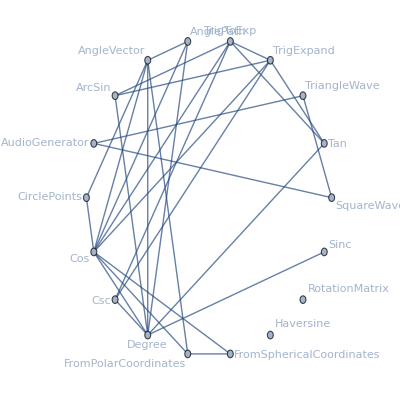
attributes | {Listable,NumericFunction,Protected}
character count | 3
common option values | Missing[NotApplicable]
date introduced | Day: Thu 23 Jun 1988
date last modified | Day: Mon 30 Mar 2015
dates modified | {Day: Wed 19 May 1999,Day: Wed 9 Jul 2014,Day: Mon 30 Mar 2015}
documentation basic examples | {{The argument is given in radians:,Sin[Pi/3],(√3)/2},{Use Degree to specify an argument in degrees:,Sin[60Degree],(√3)/2},{Plot over a subset of the reals:,Plot[Sin[x],{x,0,2Pi}],-Graphics-},{Plot over a subset of the complexes:,ComplexPlot3D[Sin[z],{z,-2 π-2 I,2 π+2 I},PlotLegends→Automatic],-Graphics-},{Series expansion at 0:,Series[Sin[x],{x,0,10}],x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11}}
documentation example counts | {BasicExamples→5,Scope→45,GeneralizationsExtensions→0,Options→0,Applications→12,PropertiesRelations→12,PossibleIssues→6,InteractiveExamples→0,NeatExamples→5}
documentation example inputs | {BasicExamples→{{Sin[Pi/3]},{Sin[60Degree]},{Plot[Sin[x],{x,0,2Pi}]},{ComplexPlot3D[Sin[z],{z,-2 π-2 I,2 π+2 I},PlotLegends→Automatic]},{Series[Sin[x],{x,0,10}]}},Scope→{{Sin[1.2]},{N[Sin[12/10],50],Sin[1.20000000000000000000000]},{Sin[2.5+I]},{Sin[1.2]//Timing,Sin[1.2];//Timing},{Sin[Interval[{-Pi,Pi}]]},{Sin[{1.2,1.5,1.8}],Sin[(π | u
v | π/2) ]},{Table[Sin[n π/6],{n,0,6}]},{Table[Sin[n π/6],{n,0,6}]},{Sin[Infinity],Sin[ComplexInfinity]},{Sin[Pi/5],Sin[Pi/24],FunctionExpand[%]},{Assuming[m∈Integers,Refine[Sin[π m]]]},{Assuming[m∈Integers,FullSimplify[Sin[π (1/2+m)]]],sol=Solve[D[Sin[x],x]== 0&&0<x<π,x],xmax=x /. First[sol],Plot[Sin[x],{x,0,2π},Epilog→Style[Point[{xmax,Sin[xmax]}],PointSize[Large],Red]]},{Plot[Sin[x],{x,0,4π}]},{ContourPlot[Re[Sin[x+ⅈ y]],{x,-2π,2π},{y,-π,π},Sequence[Contours -> 24, FrameTicks -> {{{-Pi, -Pi/2, 0, Pi/2, Pi}, None}, {{-2*Pi, -Pi, 0, Pi, 2*Pi}, None}}]],ContourPlot[Im[Sin[x+ⅈ y]],{x,-2π,2π},{y,-π,π},Sequence[Contours -> 24, FrameTicks -> {{{-Pi, -Pi/2, 0, Pi/2, Pi}, None}, {{-2*Pi, -Pi, 0, Pi, 2*Pi}, None}}]]},{Table[PolarPlot[Sin[k ϕ],{ϕ,0,2 π},Sequence[Frame→True,FrameTicks→{{{-1,-0.5,0,0.5,1},None},{{-1,-0.5,0,0.5,1},None}},PlotLabel→k=<>ToString[k]]],{k,1,8}]},{FunctionDomain[Sin[x],x],FunctionDomain[Sin[z],z,Complexes]},{FunctionRange[Sin[x],x,y],FunctionRange[Sin[z],z,y,Complexes]},{FunctionPeriod[Sin[x],x]},{Sin[-x]},{FullSimplify[Sin[Conjugate[z]]==Conjugate[Sin[z]]]},{Sin[α]//TraditionalForm},{D[Sin[x],x]},{Table[D[Sin[x],{x,n}],{n,1,4}],Plot[Evaluate[%],{x,-2π,2π},PlotLegends→{First Derivative,Second Derivative,Third Derivative,Fourth Derivative}]},{D[Sin[x],{x,n}]},{Integrate[Sin[x],x]},{Integrate[Sin[x],{x,0,2 π}]},{Integrate[Sin[x]Cos[x],x],Integrate[Sin[z]^a,z]},{Series[Sin[x],{x,0,7}],terms=Normal@Table[Series[Sin[x],{x,0,m}],{m,1,5,2}];
Plot[{Sin[x],terms},{x,-2π,2π},PlotRange→{-1.5,1.5}]},{SeriesCoefficient[Sin[x],{x,0,n}]},{FourierSeries[Sin[z],z,1]},{Sin[π/2+x+x^2/2+x^3/3+O[x]^4]},{FourierTransform[Sin[t],t,ω ]},{LaplaceTransform[Sin[t],t,s ]},{MellinTransform[Sin[x],x,s ]},{TrigExpand[Sin[2x]]},{TrigExpand[Sin[x+y]]},{TrigExpand[Sin[4x]],TrigReduce[%]},{TrigFactor[Sin[x]+Sin[y]]},{ComplexExpand[Sin[x+I y]]},{TrigToExp[Sin[z]]},{Simplify[Cos[Pi/2-x]]},{Simplify[Sqrt[(π x)/2]BesselJ[1/2,x]],Simplify[- I Sqrt[(π I x)/2]BesselI[1/2,I x]]},{Simplify[Sqrt[8 π/3]SphericalHarmonicY[1,-1,θ,0]]},{MeijerGReduce[Sin[x],x],Activate[%]},{DifferentialRootReduce[Sin[x],x]}},GeneralizationsExtensions→{},Options→{},Applications→{{ParametricPlot[{Sin[t],Cos[t]},{t,0,2Pi}]},{ParametricPlot[{Sin[t],Sin[2t]},{t,0,2Pi}]},{ParametricPlot[Exp[t/10]{Sin[t],Cos[t]},{t,0,10Pi},PlotRange->All]},{Animate[Graphics[Line[{{0,0},{Sin[t],Cos[t]}}],PlotRange->1.2],{t,0,10Pi}]},{Play[Sin[2 Pi 440 t],{t,0,1}]},{DSolve[x''[t]+ω^2 x[t]==0,x[t],t]},{RotationMatrix[θ],%.{x,y}},{ParametricPlot3D[{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]},{ϕ,-π,π},{θ,0,π}]},{ParametricPlot3D[{Cos[ϕ]+1/2 Cos[θ] Cos[ϕ],Sin[ϕ]+1/2 Cos[θ] Sin[ϕ],Sin[θ]/2},{ϕ,-π,π},{θ,0,2 π}]},{Plot3D[Sin[x]Sin[y],{x,0,10Pi},{y,0,10Pi}]},{ContourPlot3D[Sin[x]+Sin[y]+Sin[z],{x,-2Pi,2Pi},{y,-2Pi,2Pi},{z,-2Pi, 2Pi},Contours→{0},Mesh→False,BoundaryStyle→None,
ContourStyle→Opacity[0.8]]},{Plot[Sum[N[Sin[j^2 x]/j^2], {j, 1, 12}],{x,0,2Pi}]}},PropertiesRelations→{{Sin[x+2Pi],Sin[-x],Sin[I x],1/Sin[x]},{Sin[3z]^2+(2 Cos[z] Cos[2 z]-Cos[z])^2,Simplify[%],Sin[x]-Sin[y]-2Cos[(x+y)/2]Sin[(x-y)/2],Simplify[%]},{{Sin[ArcSin[z]], Sin[2ArcSin[z]], Sin[3ArcSin[z]]},FunctionExpand[%]},{Reduce[Sin[z]^2+3 Sin[z+Pi/6]==4,z]},{FindRoot[Sin[z]^2+3 Sin[z+Pi/6]==z,{z, 2}]},{Reduce[Sin[α x+β]==0,x]},{FourierTransform[Sin[t],t,s],LaplaceTransform[Sin[t],t,s]},{{BesselJ[1/2,z],MathieuS[1,0,z],JacobiSN[z,0], HypergeometricPFQ[{},{3/2},-z],MeijerG[{{},{}},{{1/2},{0}},z]}},{NumericQ[Sin[2+E]]},{DifferentialRootReduce[Sin[x],x]},{GeneratingFunction[Sin[n],n,x],Series[%,{x,0,5}]//FullSimplify},{ExponentialGeneratingFunction[Sin[n],n,x]}},PossibleIssues→{{Sin[10.^30],N[Sin[10^30],20]},{N[Sin[10^100],20],Block[{$MaxExtraPrecision=200},N[Sin[10^100],20]]},{Sin[10.^3I],MachineNumberQ[%]},{{Sin[Pi/8],Sin[Pi/12],Sin[Pi/15]},FunctionExpand[%]},{Integrate[1/(2+Sin[x]),x],Plot[%,{x,0,2Pi}]},{sin x,sin(x)}},InteractiveExamples→{},NeatExamples→{{Plot[Sin[x]+Sin[Sqrt[2]x],{x,0,40Pi}]},{Sin[π/2^12]//FunctionExpand},{Integrate[Sin[x^n],x]},{DensityPlot[Sin[3x]Sin[5y]+1/2Sin[5x]Sin[3y],{x,0,2Pi},{y,0,2Pi}]},{ArrayPlot[Table[Sin[x y],{x,-20,20},{y,-20,20}]]}}}
documentation example text | {BasicExamples→{{The argument is given in radians:},{Use Degree to specify an argument in degrees:},{Plot over a subset of the reals:},{Plot over a subset of the complexes:},{Series expansion at 0:}},Scope→{{Evaluate numerically:},{Evaluate to high precision:,The precision of the output tracks the precision of the input:},{Sin can take complex number inputs:},{Evaluate Sin efficiently at high precision:},{Sin can deal with real-valued intervals:},{Sin threads elementwise over lists and matrices:},{Values of Sin at fixed points:},{Sin has exact values at rational multiples of pi:},{Values at infinity:},{Simple exact values are generated automatically:,More complicated cases require explicit use of FunctionExpand:},{Zeros of Sin:},{Extrema of Sin:,Find the first positive maximum as a root of (d sin(x))/dx==0:,Substitute in the result:,Visualize the result:},{Plot the Sin function:},{Plot the real part of sin(x+ⅈ y):,Plot the imaginary part of sin(x+ⅈ y):},{Polar plot with r=sin(k ϕ):},{Sin is defined for all real and complex values:},{Sin achieves all real values between -1 and 1:,The range for complex values is the whole plane:},{Sin is a periodic function with a period 2 π:},{Sin is an odd function:},{Sin has the mirror property sin(Conjugate[z])==Conjugate[sin(z)]:},{TraditionalForm formatting:},{First derivative:},{Higher derivatives:},{Formula for the n^th derivative:},{Compute the indefinite integral using Integrate:},{Definite integral of Sin over a period is 0:},{More integrals:},{Find the Taylor expansion using Series:,Plots of the first three approximations for Sin around x=0:},{General term in the series expansion using SeriesCoefficient:},{Fourier series:},{Sin can be applied to power series:},{Compute the Fourier transform using FourierTransform:},{LaplaceTransform:},{MellinTransform:},{Double-angle formula using TrigExpand:},{Angle sum formula:},{Multiple-angle expressions:,Recover the original expression using TrigReduce:},{Convert sums to products using TrigFactor:},{Expand using ComplexExpand assuming real variables x and y:},{Convert to exponentials using TrigToExp:},{Use Simplify to find a representation through Cos:},{Representation through Bessel functions:},{Representation through SphericalHarmonicY:},{Representation in terms of MeijerG:},{Sin can be represented as a DifferentialRoot:}},GeneralizationsExtensions→{},Options→{},Applications→{{Draw a circle:},{Lissajous figure:},{Equiangular (logarithmic) spiral:},{Motion in a circle:},{Play a pure tone at 440 Hz:},{Solve an equation for harmonic motion:},{Rotation matrix:,Rotate a vector:},{Plot a sphere:},{Plot a torus:},{Waves:},{Triple-periodic surface:},{Approximate the almost nowhere differentiable Riemann–Weierstrass function:}},PropertiesRelations→{{Basic parity and periodicity properties are automatically applied:},{Complicated expressions containing trigonometric functions do not simplify automatically:},{Compose with inverse functions:},{Solve a trigonometric equation:},{Numerically find a root of a transcendental equation:},{Reduce a trigonometric equation:},{Fourier transform:},{Sin appears in special cases of many mathematical functions: },{Sin is a numeric function:},{Sin can be represented as a DifferentialRoot:},{The generating function for Sin:},{The exponential generating function for Sin:}},PossibleIssues→{{Machine-precision input is insufficient to get a correct answer:,With exact input, the answer is correct:},{A larger setting for $MaxExtraPrecision can be needed:},{Machine-number inputs can give high-precision results:},{Use FunctionExpand to express sine of rationals times π using radicals:},{Continuous functions involving Sin[x] can give discontinuous indefinite integrals:},{In TraditionalForm, parentheses are needed around the argument:}},InteractiveExamples→{},NeatExamples→{{Noncommensurate waves (quasiperiodic function):},{Some arguments can be expressed as a finite sequence of nested radicals:},{Indefinite integral of sin(x^n):},{Chladni figure:},{Plot Sin at integer points:}}}
entity classes | {}
eponymous people | {}
equal-precedence symbols | Missing[NotApplicable]
external links | {MathWorld→http://mathworld.wolfram.com/Sine.html,WolframFunctionsSite→http://functions.wolfram.com/ElementaryFunctions/Sin/}
frequencies of usage | {All→0.00188617,StackExchange→0.00520774,TypicalProductionCode→0.00424279,WolframAlphaCodebase→0.00102919,WolframDemonstrations→0.00530746,WolframDocumentation→0.00374508}
full version introduced | 1
full version last modified | 10.1
full versions modified | {4,10,10.1}
functionality areas | {BasicSymbols}
symbol background | Sin is the sine function, which is one of the basic functions encountered in trigonometry. It is defined for real numbers by letting x be a radian angle measured counterclockwise from the x axis along the circumference of the unit circle. Sin[x] then gives the vertical coordinate of the arc endpoint. The equivalent schoolbook definition of the sine of an angle θ in a right triangle is the ratio of the length of the leg opposite θ to the length of the hypotenuse.
Sin automatically evaluates to exact values when its argument is a simple rational multiple of π. For more complicated rational multiples, FunctionExpand can sometimes be used to obtain an explicit exact value. To specify an argument using an angle measured in degrees, the symbol Degree can be used as a multiplier (e.g. Sin[30 Degree]). When given exact numeric expressions as arguments, Sin may be evaluated to arbitrary numeric precision. Other operations useful for manipulation of symbolic expressions involving Sin include TrigToExp, TrigExpand, Simplify, and FullSimplify.
Sin threads element-wise over lists and matrices. In contrast, MatrixFunction can be used to give the sine of a square matrix (i.e. the power series for the sine function with ordinary powers replaced by matrix powers).
Sin is periodic with period 2π, as reported by FunctionPeriod. Sin satisfies the identity sin^2(x)+cos^2(x)==1, which is equivalent to the Pythagorean theorem. The definition of the sine function is extended to complex arguments z using the definition sin(z)==1/2 ⅈ(ⅇ^(-ⅈ z)-ⅇ^(ⅈ z)), where ⅇ is the base of the natural logarithm. The sine function is entire, meaning it is complex differentiable at all finite points of the complex plane. Sin[z] has series expansion ∑_(k=0)^∞ (-1)^(k-1)/((2 k-1)!)z^(2 k-1) about the origin.
The inverse function of Sin is ArcSin. The hyperbolic sine is given by Sinh. Other related mathematical functions include Cos, Tan, and Csc.
keyboard shortcuts | Missing[NotAvailable]
link trails | {{guide/WolframRoot,guide/FormulaManipulation,guide/AlgebraicTransformations,guide/TrigonometricFunctions,ref/Sin},{guide/WolframRoot,guide/MathematicalFunctions,guide/ElementaryFunctions,guide/TrigonometricFunctions,ref/Sin},{guide/WolframRoot,guide/ScientificModels,guide/MathematicalFunctions,guide/ElementaryFunctions,guide/TrigonometricFunctions,ref/Sin},{guide/WolframRoot,guide/PhysicsAndChemistryDataAndComputation,guide/ScientificModels,guide/MathematicalFunctions,guide/ElementaryFunctions,guide/TrigonometricFunctions,ref/Sin},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ScientificModels,guide/MathematicalFunctions,guide/ElementaryFunctions,guide/TrigonometricFunctions,ref/Sin}}
memberships | {}
name | Sin
option names | {}
options | {}
plaintext usage | Sin[z] gives the sine of z.
precedence ranks | Missing[NotApplicable]
ranks of usage | {All→30,StackExchange→20,TypicalProductionCode→29,WolframAlphaCodebase→37,WolframDemonstrations→22,WolframDocumentation→20}
related entities | Missing[NotAvailable]
related guide pages | {Precollege Educationpaclet:guide/PrecollegeEducation,Trigonometric Functionspaclet:guide/TrigonometricFunctions,Summary of New Features in 12paclet:guide/SummaryOfNewFeaturesIn12,Functions for Separable Coordinate Systemspaclet:guide/FunctionsForSeparableCoordinateSystems,Mathematical Functionspaclet:guide/MathematicalFunctions,Elementary Functionspaclet:guide/ElementaryFunctions,Neural Networkspaclet:guide/NeuralNetworks}
related symbols | {AngleVector,ArcSin,Cos,Tan,Csc,Degree,TrigToExp,TrigExpand,Sinc,Haversine,CirclePoints}
relationship community graph | -Graphics-
relationship graph | -Graphics-
short notations | Missing[NotApplicable]
subject classifications | {Mathematics Subject Classification 2010→{33B10,51Nxx}}
symbols linking to | {AnglePath,AngleVector,ArcSin,AudioGenerator,CirclePoints,Cos,Csc,Degree,FromPolarCoordinates,FromSphericalCoordinates,Haversine,RotationMatrix,Sinc,SquareWave,TriangleWave}
symbols using as attribute | {}
symbols using as option | {}
text strings | {Sin[z] gives the sine of z.,Mathematical function, suitable for both symbolic and numerical manipulation.,Unless explicitly given as a Quantity object, the argument of Sin is assumed to be in radians. (Multiply by Degree to convert from degrees.)19487,Sin is automatically evaluated when its argument is a simple rational multiple of π; for more complicated rational multiples, FunctionExpand can sometimes be used.3266,For certain special arguments, Sin automatically evaluates to exact values.,Sin can be evaluated to arbitrary numerical precision.,Sin automatically threads over lists.,The argument is given in radians:,Use Degree to specify an argument in degrees:,Plot over a subset of the reals:,Plot over a subset of the complexes:,Series expansion at 0:,Evaluate numerically:,Evaluate to high precision:,The precision of the output tracks the precision of the input:,Sin can take complex number inputs:,Evaluate Sin efficiently at high precision:,Sin can deal with real-valued intervals:,Sin threads elementwise over lists and matrices:,Values of Sin at fixed points:,Sin has exact values at rational multiples of pi:,Values at infinity:,Simple exact values are generated automatically:,More complicated cases require explicit use of FunctionExpand:,Zeros of Sin:,Extrema of Sin:,Find the first positive maximum as a root of (d sin(x))/dx==0:,Substitute in the result:,Visualize the result:,Plot the Sin function:,Plot the real part of sin(x+ⅈ y):,Plot the imaginary part of sin(x+ⅈ y):,Polar plot with r=sin(k ϕ):,Sin is defined for all real and complex values:,Sin achieves all real values between -1 and 1:,The range for complex values is the whole plane:,Sin is a periodic function with a period 2 π:,Sin is an odd function:,Sin has the mirror property sin(z^*)==sin(z)^*:,TraditionalForm formatting:,First derivative:,Higher derivatives:,Formula for the n^th derivative:,Compute the indefinite integral using Integrate:,Definite integral of Sin over a period is 0:,More integrals:,Find the Taylor expansion using Series:,Plots of the first three approximations for Sin around x=0:,General term in the series expansion using SeriesCoefficient:,Fourier series:,Sin can be applied to power series:,Compute the Fourier transform using FourierTransform:,LaplaceTransform:,MellinTransform:,Double-angle formula using TrigExpand:,Angle sum formula:,Multiple-angle expressions:,Recover the original expression using TrigReduce:,Convert sums to products using TrigFactor:,Expand using ComplexExpand assuming real variables x and y:,Convert to exponentials using TrigToExp:,Use Simplify to find a representation through Cos:,Representation through Bessel functions:,Representation through SphericalHarmonicY:,Representation in terms of MeijerG:,Sin can be represented as a DifferentialRoot:,Draw a circle:,Lissajous figure:,Equiangular (logarithmic) spiral:,Motion in a circle:,Play a pure tone at 440 Hz:,Solve an equation for harmonic motion:,Rotation matrix:,Rotate a vector:,Plot a sphere:,Plot a torus:,Waves:,Triple-periodic surface:,Approximate the almost nowhere differentiable Riemann–Weierstrass function:,Basic parity and periodicity properties are automatically applied:,Complicated expressions containing trigonometric functions do not simplify automatically:,Compose with inverse functions:,Solve a trigonometric equation:,Numerically find a root of a transcendental equation:,Reduce a trigonometric equation:,Fourier transform:,Sin appears in special cases of many mathematical functions:,Sin is a numeric function:,Sin can be represented as a DifferentialRoot:,The generating function for Sin:,The exponential generating function for Sin:,Machine-precision input is insufficient to get a correct answer:,With exact input, the answer is correct:,A larger setting for $MaxExtraPrecision can be needed:,Machine-number inputs can give high-precision results:,Use FunctionExpand to express sine of rationals times π using radicals:,Continuous functions involving Sin[x] can give discontinuous indefinite integrals:,In TraditionalForm, parentheses are needed around the argument:,Noncommensurate waves (quasiperiodic function):,Some arguments can be expressed as a finite sequence of nested radicals:,Indefinite integral of sin(x^n):,Chladni figure:,Plot Sin at integer points:,Sin is the sine function, which is one of the basic functions encountered in trigonometry. It is defined for real numbers by letting x be a radian angle measured counterclockwise from the x axis along the circumference of the unit circle. Sin[x] then gives the vertical coordinate of the arc endpoint. The equivalent schoolbook definition of the sine of an angle θ in a right triangle is the ratio of the length of the leg opposite θ to the length of the hypotenuse.,Sin automatically evaluates to exact values when its argument is a simple rational multiple of π. For more complicated rational multiples, FunctionExpand can sometimes be used to obtain an explicit exact value. To specify an argument using an angle measured in degrees, the symbol Degree can be used as a multiplier (e.g. Sin[30 Degree]). When given exact numeric expressions as arguments, Sin may be evaluated to arbitrary numeric precision. Other operations useful for manipulation of symbolic expressions involving Sin include TrigToExp, TrigExpand, Simplify, and FullSimplify.,Sin threads element-wise over lists and matrices. In contrast, MatrixFunction can be used to give the sine of a square matrix (i.e. the power series for the sine function with ordinary powers replaced by matrix powers).,Sin is periodic with period 2π, as reported by FunctionPeriod. Sin satisfies the identity sin^2(x)+cos^2(x)==1, which is equivalent to the Pythagorean theorem. The definition of the sine function is extended to complex arguments z using the definition sin(z)==1/2 ⅈ(ⅇ^(-ⅈ z)-ⅇ^(ⅈ z)), where ⅇ is the base of the natural logarithm. The sine function is entire, meaning it is complex differentiable at all finite points of the complex plane. Sin[z] has series expansion ,\*UnderoverscriptBox[\(∑\), \(k = 0\), \(∞\)]\(,\*FractionBox[,SuperscriptBox[\((\(-1\))\), \(k - 1\)], \(\((2\ k - 1)\)!\)],\*SuperscriptBox[\(z\), \(2\ k - 1\)]\)\) about the origin.,The inverse function of Sin is ArcSin. The hyperbolic sine is given by Sinh. Other related mathematical functions include Cos, Tan, and Csc.}
timeline | -Graphics-
timeline events | Interval[{Day: Thu 23 Jun 1988,Day: Mon 30 Mar 2015}]Sin
translations | {Simplified Chinese→正弦,Traditional Chinese→正弦,French→sinus,German→Sinus,Modern Greek→ημίτονο,Japanese→正弦,Korean→사인,Lithuanian→sinusas,Polish→sinus,Portuguese→seno,Russian→синус,Spanish→seno,Ukrainian→синус,Vietnamese→sin}
typeset usage | Sin[z] gives the sine of z. 
URL | http://reference.wolfram.com/language/ref/Sin.html
version introduced | 1
version last modified | 10.1
versions modified | {4,10,10.1}
Wolfram documentation link | Sinpaclet:ref/Sin

```mathematica
Grid[MapThread[{#1,#2}&,{wlEntityProperties,AllPropertiesForSymbol@Sin}],Frame->All]
```

```mathematica
numericFunctionSymbols=Select[
MapThread[
{#1,#2}&,
{wlSymbols,EntityValue[wlSymbols,EntityProperty["WolframLanguageSymbol","Attributes"]]}
],
Count[Last@#,Entity["WolframLanguageSymbol","NumericFunction"]]>0&
];
```

### Working with triangles

#### TrianglePointsQ

```mathematica
TrianglePointsQ[a_List,b_List,c_List]:=ResourceFunction["TriangleEdgesQ"]@(EuclideanDistance@@@{{a,b},{b,c},{c,a}})/;Dimensions[a]==Dimensions[b]==Dimensions[c]&&ContainsOnly[NumericQ/@Flatten[{a,b,c}],{True}]

TrianglePointsQ[points_List]:=TrianglePointsQ@@points/;Length[points]==3
```

Some tests

```mathematica
Grid[{Polygon@#,TrianglePointsQ@#}&/@RandomInteger[3,{10,3,2}],Frame->All]
```

Polygon[…] | True
Polygon[…] | False
Polygon[…] | False
Polygon[…] | True
Polygon[…] | True
Polygon[…] | False
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True

#### TrianglePolygonQ

```mathematica
TrianglePolygonQ[polygon_]:=TrianglePointsQ[PolygonCoordinates@polygon]/;SimplePolygonQ@polygon&&Length[PolygonCoordinates@polygon]==3
```

Some tests

```mathematica
Grid[{#,TrianglePolygonQ@#}&/@Polygon/@RandomInteger[3,{10,3,2}],Frame->All]
```

Polygon[…] | True
Polygon[…] | True
Polygon[…] | TrianglePolygonQ[Polygon[…]]
Polygon[…] | True
Polygon[…] | TrianglePolygonQ[Polygon[…]]
Polygon[…] | TrianglePolygonQ[Polygon[…]]
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True



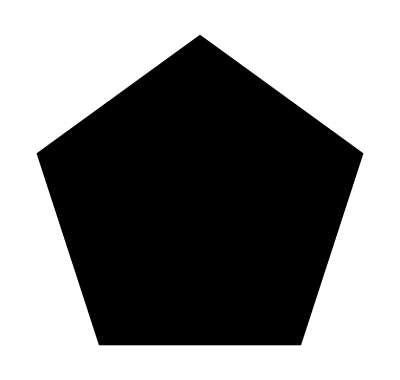
-Graphics- | True
-Graphics- | TrianglePolygonQ[RegularPolygon[4]]
-Graphics- | TrianglePolygonQ[RegularPolygon[5]]

```mathematica
Grid[{Graphics@#,TrianglePolygonQ@#}&/@RegularPolygon/@Range[3,5],Frame->All]
```

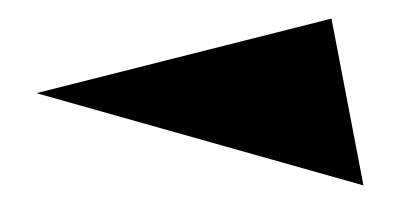
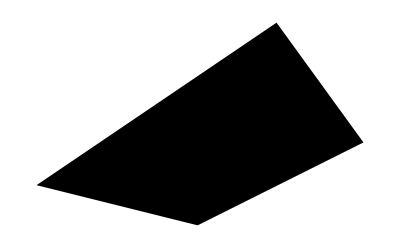
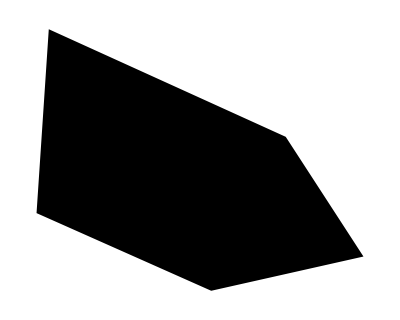
-Graphics- | True
-Graphics- | TrianglePolygonQ[Polygon[…]]
-Graphics- | TrianglePolygonQ[Polygon[…]]

```mathematica
Grid[{Graphics@#,TrianglePolygonQ@#}&/@RandomPolygon/@Range[3,5],Frame->All]
```

#### TriangleQ

```mathematica
TriangleQ[a_List,b_List,c_List]:=TrianglePointsQ[a,b,c]
TriangleQ[list_List]:=TrianglePointsQ[list]
TriangleQ[polygon_]:=TrianglePolygonQ[polygon]/;SimplePolygonQ[polygon]
```

Some tests

```mathematica
Grid[{Polygon@#,TriangleQ@@#}&/@RandomInteger[3,{10,3,2}],Frame->All]
```

Polygon[…] | False
Polygon[…] | False
Polygon[…] | True
Polygon[…] | True
Polygon[…] | False
Polygon[…] | False
Polygon[…] | True
Polygon[…] | False
Polygon[…] | True
Polygon[…] | True

```mathematica
Grid[{Polygon@#,TriangleQ@#}&/@RandomInteger[3,{10,3,2}],Frame->All]
```

Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | False
Polygon[…] | True
Polygon[…] | False
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True

```mathematica
Grid[{Polygon@#,TriangleQ[Polygon@#]}&/@RandomInteger[3,{10,3,2}],Frame->All]
```

Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | TriangleQ[Polygon[…]]

```mathematica
Grid[{Graphics@RegularPolygon@#,TriangleQ[RegularPolygon@#]}&/@Range[3,5],Frame->All]
```

-Graphics- | True
-Graphics- | TrianglePolygonQ[RegularPolygon[4]]
-Graphics- | TrianglePolygonQ[RegularPolygon[5]]

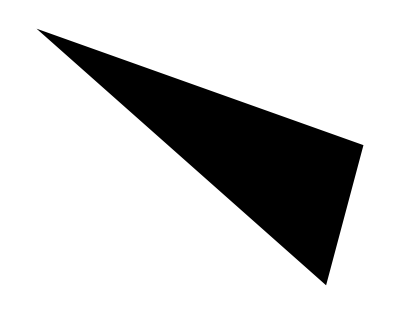
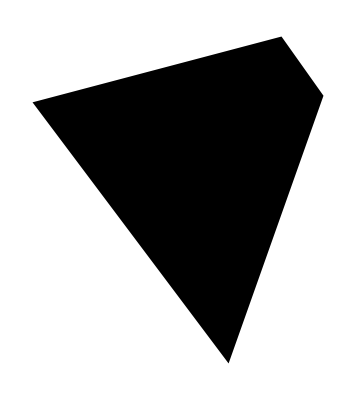
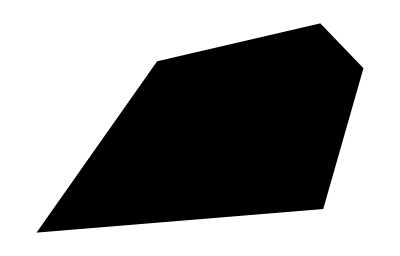
-Graphics- | True
-Graphics- | TrianglePolygonQ[Polygon[…]]
-Graphics- | TrianglePolygonQ[Polygon[…]]

```mathematica
Grid[{Graphics@RandomPolygon@#,TriangleQ[RandomPolygon@#]}&/@Range[3,5],Frame->All]
```

#### TrianglePolygonAngles

```mathematica
TrianglePolygonAngles[polygon_]:=(N@*PlanarAngle)/@DeleteDuplicates[Permutations[PolygonCoordinates@polygon,{3}],#1⟦2⟧==#2⟦2⟧&]/;TrianglePolygonQ@polygon
```

Some tests

```mathematica
Grid[{#,Total[TrianglePolygonAngles@#]==Pi}&/@Polygon/@RandomReal[10,{10,3,2}],Frame->All]
```

Polygon[…] | Total[TrianglePolygonAngles[Polygon[…]]]==π
Polygon[…] | Total[TrianglePolygonAngles[Polygon[…]]]==π
Polygon[…] | Total[TrianglePolygonAngles[Polygon[…]]]==π
Polygon[…] | Total[TrianglePolygonAngles[Polygon[…]]]==π
Polygon[…] | Total[TrianglePolygonAngles[Polygon[…]]]==π
Polygon[…] | Total[TrianglePolygonAngles[Polygon[…]]]==π
Polygon[…] | Total[TrianglePolygonAngles[Polygon[…]]]==π
Polygon[…] | Total[TrianglePolygonAngles[Polygon[…]]]==π
Polygon[…] | Total[TrianglePolygonAngles[Polygon[…]]]==π
Polygon[…] | Total[TrianglePolygonAngles[Polygon[…]]]==π

#### TriangleTypeQ

Right-angled triangle
A right-angled triangle has one 90° angle.That 90 ° angle is shown as a small square where two sides of the triangle join. It is possible for a triangle to be a right-angled triangle and an isosceles triangle at the same time. In this case the angles would be 90°, 45° and 45°. [1]

```mathematica
Clear@TriangleRightQ
```

```mathematica
TriangleRightQ[triangle_]:=ContainsAny[TrianglePolygonAngles@triangle,{N[Pi/2]}]/;TrianglePolygonQ@triangle
```

Equilateral
An equilateral triangle has three equal sides and angles. It will always have angles of 60° in each corner. [1]

```mathematica
Clear@TriangleEquilateralQ
```

```mathematica
TriangleEquilateralQ[triangle_]:=ContainsOnly[TrianglePolygonAngles@triangle,{N[Pi/3]}]/;TrianglePolygonQ@triangle
```

Isosceles
An isosceles triangle can be drawn in many different ways. It can be drawn to have two equal sides and two equal angles or with two acute angles and one obtuse angle. It is easy to work out the missing angles of an isosceles triangle by looking for the angles that should be equal. [1]

```mathematica
Clear@TriangleIsoscelesQ
```

```mathematica
TriangleIsoscelesQ[triangle_]:=With[
{sides=(N@*EuclideanDistance)@@@Subsets[PolygonCoordinates@triangle,{2}]},
Length[DeleteDuplicates@sides]≤2
]/;TrianglePolygonQ@triangle
```

Scalene
A scalene triangle has three different angles and none of its sides are equal in length. [1]

```mathematica
Clear@TriangleScaleneQ
```

```mathematica
TriangleScaleneQ[triangle_]:=With[
{sides=(N@*EuclideanDistance)@@@Subsets[PolygonCoordinates@triangle,{2}]},
Length[DeleteDuplicates@sides]==3
]/;TrianglePolygonQ@triangle
```

Obtuse
An obtuse triangle has three different angles, with one angle greater than 90°. None of its sides are equal in length. [1]

```mathematica
Clear@TriangleObtuseQ
```

```mathematica
TriangleObtuseQ[triangle_]:=With[
{angles=TrianglePolygonAngles@triangle,
sides=(N@*EuclideanDistance)@@@Subsets[PolygonCoordinates@triangle,{2}]},
Length[Select[angles,#>N[Pi/2]&]]>0&&Length[DeleteDuplicates@angles]==3&&Length[DeleteDuplicates@sides]==3
]/;TrianglePolygonQ@triangle
```

Some tests

```mathematica
triangles={
Triangle[],AASTriangle[Pi/6,Pi/3,1],
SSSTriangle[3,4,5],SASTriangle[1,Pi/2,2],
ASATriangle[Pi/6,1,Pi/3],
Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}],
Polygon[{{0,0},{10,10},{10,20}}],
RandomPolygon@3
};

triangleQs={
TrianglePolygonQ,
TriangleRightQ,
TriangleEquilateralQ,
TriangleIsoscelesQ,
TriangleScaleneQ,
TriangleObtuseQ
};
```

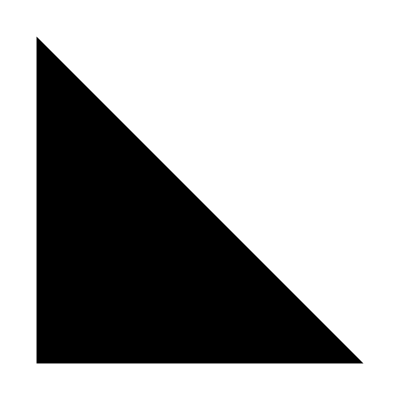
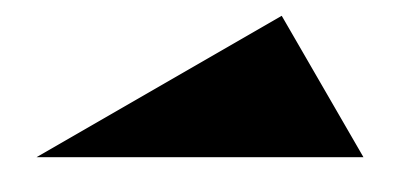
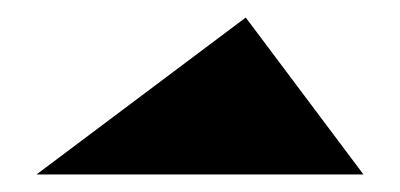
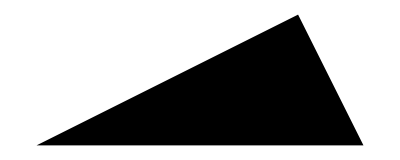
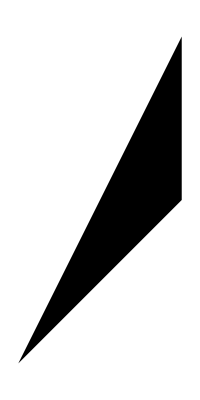
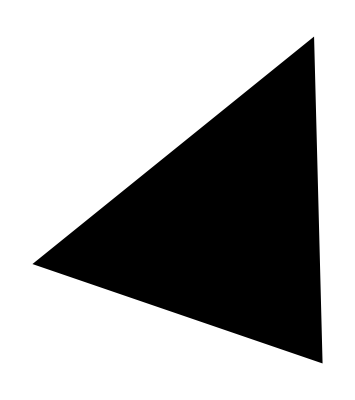
Graphics | Interior angles | Side lengths | Triangle? | Right? | Equilateral? | Isosceles? | Scalene? | Obtuse?
-Graphics- | {90.,45.,45.} | {1.,1.,1.41421} | Yes | Yes | No | Yes | No | No
-Graphics- | {30.,60.,90.} | {2.,1.73205,1.} | Yes | Yes | No | No | Yes | No
-Graphics- | {36.8699,53.1301,90.} | {5.,4.,3.} | Yes | Yes | No | No | Yes | No
-Graphics- | {26.5651,63.4349,90.} | {2.23607,2.,1.} | Yes | Yes | No | No | Yes | No
-Graphics- | {30.,60.,90.} | {1.,0.866025,0.5} | Yes | Yes | No | No | Yes | No
-Graphics- | {60.,60.,60.} | {2.,2.,2.} | Yes | No | Yes | Yes | No | No
-Graphics- | {18.4349,135.,26.5651} | {14.1421,22.3607,10.} | Yes | No | No | No | Yes | Yes
-Graphics- | {57.8388,69.5997,52.5616} | {0.786477,0.710348,0.666256} | Yes | No | No | No | Yes | No

```mathematica
triangleTests=Function[
triangle,
Flatten[
{{Graphics@triangle,
N[#/Degree]&/@PolygonAngle[triangle],
N@*EuclideanDistance@@#&/@Subsets[First[List@@triangle],{2}]},
With[
{answer=#[triangle]},
Style[TextString[answer,BooleanStrings-> {"Yes","No" }],If[answer,Blue,Red]]
]&/@triangleQs},
1
]
]/@triangles;
Grid[PrependTo[triangleTests,Style[#,Bold]&/@{"Graphics","Interior angles","Side lengths", "Triangle?", "Right?", "Equilateral?","Isosceles?","Scalene?","Obtuse?"}],Frame->All]
```

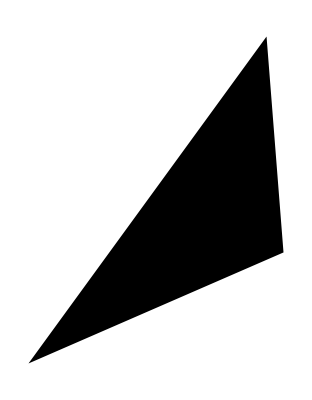
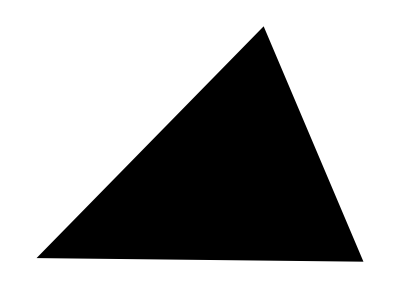
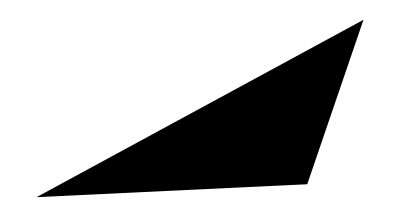
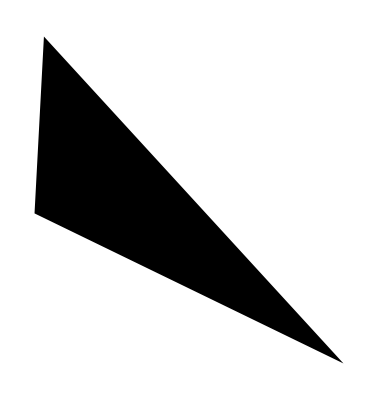
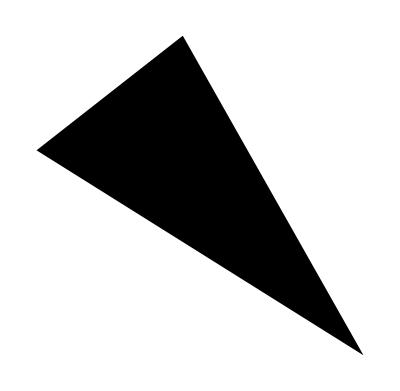
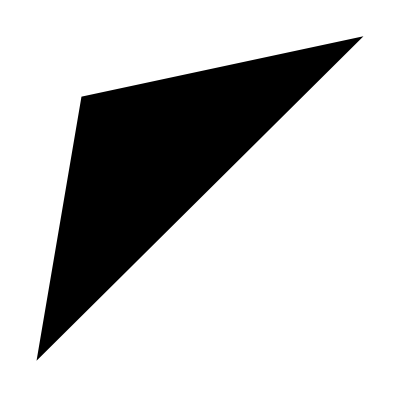
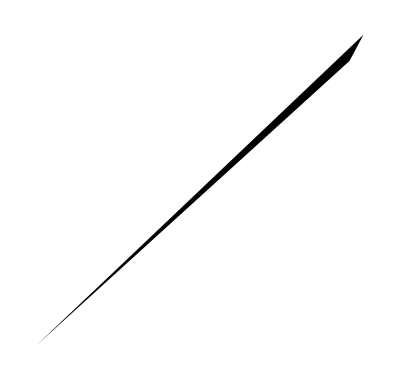
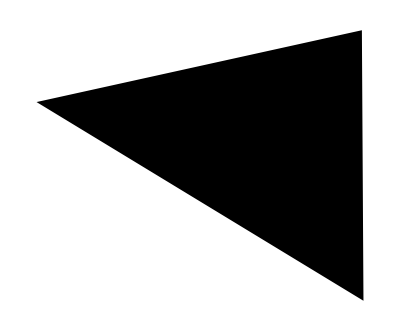
Graphics | Interior angles | Side lengths | Triangle? | Right? | Equilateral? | Isosceles? | Scalene? | Obtuse?
-Graphics- | {30.4086,109.015,40.5762} | {29.2323,22.7476,42.4888} | Yes | No | No | No | Yes | Yes
-Graphics- | {46.2809,66.4386,67.2805} | {13.3353,10.5145,13.4193} | Yes | No | No | No | Yes | No
-Graphics- | {25.7715,111.597,42.6317} | {12.0794,18.8167,25.8322} | Yes | No | No | No | Yes | Yes
-Graphics- | {112.855,21.5932,45.5522} | {17.8526,34.6312,44.7023} | Yes | No | No | No | Yes | Yes
-Graphics- | {70.1976,28.4301,81.3723} | {45.7571,23.1534,48.0826} | Yes | No | No | No | Yes | No
-Graphics- | {324.458,248.254,327.288} | {27.2955,43.6142,25.3757} | Yes | No | No | No | Yes | Yes
-Graphics- | {1.27552,160.275,18.4491} | {1.93105,27.4528,29.2778} | Yes | No | No | No | Yes | Yes
-Graphics- | {43.8286,58.3136,77.8578} | {18.4666,22.6915,26.0699} | Yes | No | No | No | Yes | No
-Graphics- | {94.9098,25.7397,59.3505} | {31.0785,13.5466,26.8354} | Yes | No | No | No | Yes | Yes
-Graphics- | {67.1011,79.2719,33.6271} | {32.577,30.5435,18.3616} | Yes | No | No | No | Yes | No

```mathematica
triangleTests2=Function[
triangle,
Flatten[
{{Graphics@triangle,
N[#/Degree]&/@PolygonAngle[triangle],
N@*EuclideanDistance@@#&/@Subsets[First[List@@triangle],{2}]},
With[
{answer=#[triangle]},
Style[TextString[answer,BooleanStrings-> {"Yes","No" }],If[answer,Blue,Red]]
]&/@triangleQs},
1
]
]/@Polygon/@RandomReal[50,{10,3,2}];
Grid[PrependTo[triangleTests2,Style[#,Bold]&/@{"Graphics","Interior angles","Side lengths", "Triangle?", "Right?", "Equilateral?","Isosceles?","Scalene?","Obtuse?"}],Frame->All]
```

#### TriangleCharacteristics

```mathematica
TriangleCharacteristics[triangle_]:=With[
{rules=<|TriangleRightQ-> "Right",TriangleEquilateralQ-> "Equilateral",TriangleIsoscelesQ-> "Isosceles",TriangleScaleneQ-> "Scalene",TriangleObtuseQ-> "Obtuse"|>},
Select[Keys@rules,#@triangle&]/.rules
]/;TriangleQ@triangle
```

```mathematica
TriangleCharacteristics/@triangles
```

{{Right,Isosceles},{Right,Scalene},{Right,Scalene},{Right,Scalene},{Right,Scalene},{Equilateral,Isosceles},{Scalene,Obtuse},{Scalene}}

#### TriangleGreatestSide

```mathematica
TriangleGreatestSide[triangle_]:=Block[
{coordinates,sides,lengths,greatestSideCoordinate},
coordinates=PolygonCoordinates@triangle;
sides=Subsets[coordinates,{2}];
lengths={#,N@*EuclideanDistance@@#}&/@sides;
greatestSideCoordinate=Sort[lengths,Last@#1>Last@#2&]⟦1,1⟧;
greatestSideCoordinate
]/;TrianglePolygonQ@triangle
```

Some tests

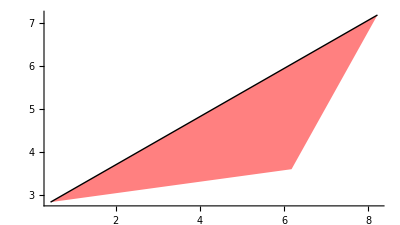
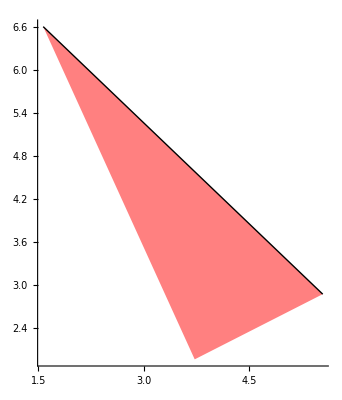
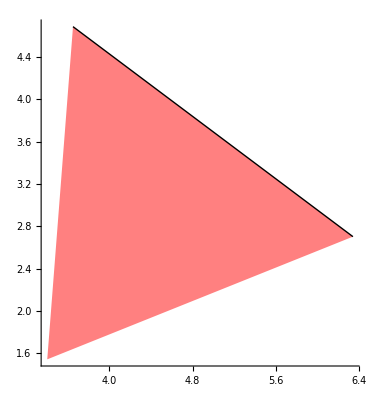
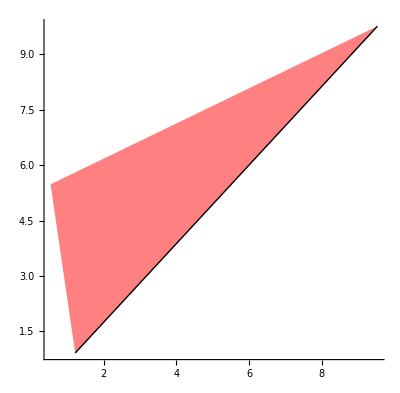
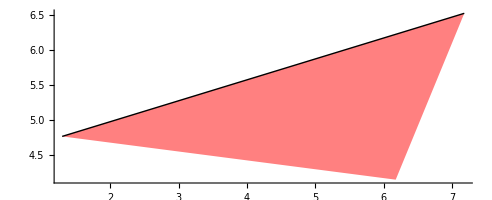
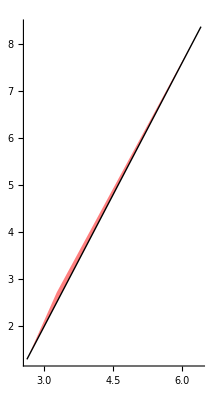
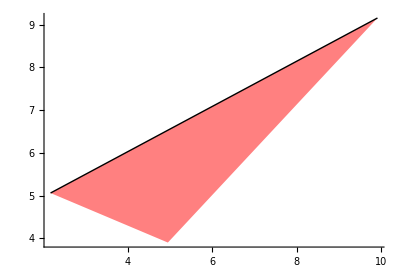
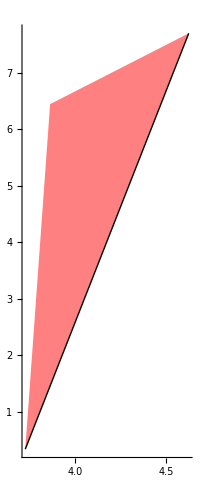
{{0.457577,2.82276},{8.21474,7.1929}} | -Graphics-
{{1.56879,6.60817},{5.5452,2.87664}} | -Graphics-
{{3.64951,4.68532},{6.34377,2.70157}} | -Graphics-
{{1.21336,0.910283},{9.53526,9.76373}} | -Graphics-
{{1.29844,4.75979},{7.17757,6.52562}} | -Graphics-
{{2.63205,1.2973},{6.41573,8.37728}} | -Graphics-
{{2.16,5.06366},{9.92087,9.15773}} | -Graphics-
{{3.72714,0.333577},{4.624,7.70406}} | -Graphics-
{{4.30053,5.55964},{9.51506,0.236313}} | -Graphics-
{{1.33277,1.32123},{4.12692,1.36227}} | -Graphics-

```mathematica
sideTests=With[
{side=TriangleGreatestSide@#},
{side,Graphics[{Pink,#,Black,Thick,Line@side},Axes->True]}
]&/@Polygon/@RandomReal[10,{10,3,2}];
Grid[sideTests,Frame->All]
```

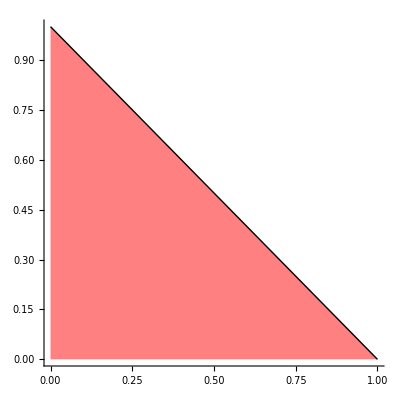
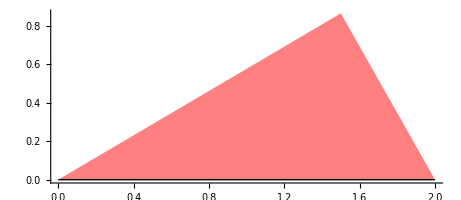
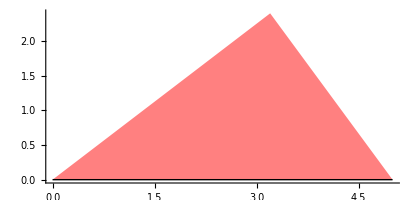
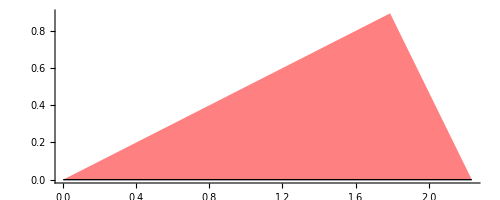
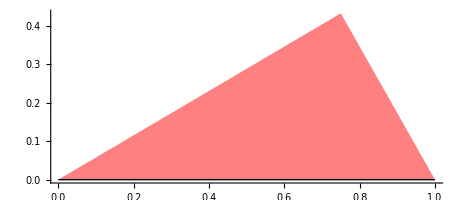
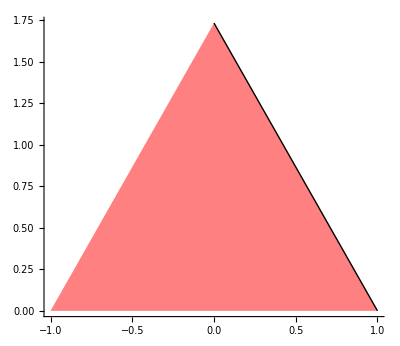
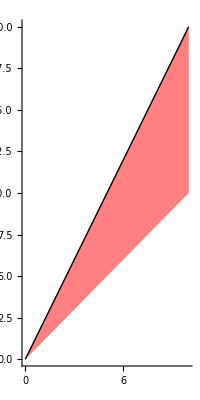
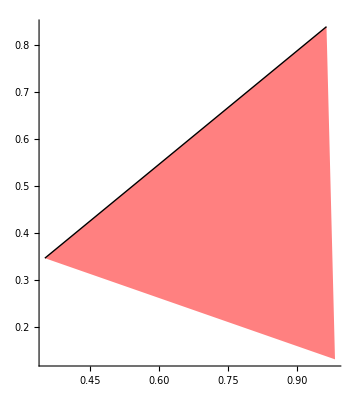
{{0,1},{1,0}} | -Graphics-
{{0,0},{2,0}} | -Graphics-
{{0,0},{5,0}} | -Graphics-
{{0,0},{√5,0}} | -Graphics-
{{0,0},{1,0}} | -Graphics-
{{0,√3},{1,0}} | -Graphics-
{{0,0},{10,20}} | -Graphics-
{{0.352096,0.345973},{0.963927,0.840148}} | -Graphics-

```mathematica
sideTests=With[
{side=TriangleGreatestSide@#},
{side,Graphics[{Pink,#,Black,Thick,Line@side},Axes->True]}
]&/@triangles;
Grid[sideTests,Frame->All]
```

#### AngleOrientation

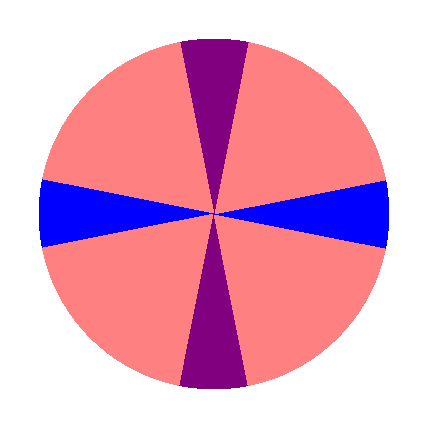
Regions to define the orientation of the greatest side of a triangle.
-Graphics-
Blue = Horizontal
Purple = Vertical
Pink = Diagonal

```mathematica
orientationRules=<|0.->"Horizontal",0.19634954084936207->"Horizontal",3.141592653589793->"Horizontal",3.3379421944391554->"Horizontal",6.283185307179586->"Horizontal",1.5707963267948966->"Vertical",1.7671458676442586->"Vertical",4.71238898038469->"Vertical",4.908738521234052->"Vertical",0.39269908169872414->"Diagonal",0.5890486225480862->"Diagonal",0.7853981633974483->"Diagonal",0.9817477042468103->"Diagonal",1.1780972450961724->"Diagonal",1.3744467859455345->"Diagonal",1.9634954084936207->"Diagonal",2.1598449493429825->"Diagonal",2.356194490192345->"Diagonal",2.552544031041707->"Diagonal",2.748893571891069->"Diagonal",2.945243112740431->"Diagonal",3.5342917352885173->"Diagonal",3.730641276137879->"Diagonal",3.9269908169872414->"Diagonal",4.123340357836604->"Diagonal",4.319689898685965->"Diagonal",4.516039439535327->"Diagonal",5.105088062083414->"Diagonal",5.301437602932776->"Diagonal",5.497787143782138->"Diagonal",5.6941366846315->"Diagonal",5.890486225480862->"Diagonal",6.086835766330224->"Diagonal"|>;
orientationColors=<|"Horizontal"-> Blue,"Vertical"-> Purple,"Diagonal"-> Pink|>;
regionsGraph=Graphics[{orientationColors@orientationRules@#,Disk[{0,0},1,{#-N[Pi/16],#}]}&/@Range[0,2.Pi,Pi/16.]];
Grid[{
{Style["Regions to define the orientation of the greatest side of a triangle.",Bold]},
{regionsGraph},
{Style["Blue = Horizontal",Blue,Bold]},
{Style["Purple = Vertical",Purple,Bold]},
{Style["Pink = Diagonal",Pink,Bold]}
},Frame->All]
```

```mathematica
Angle[a_List,b_List]:=With[{c={b⟦1⟧,a⟦2⟧}},N@PlanarAngle[{b,a,c}]]/;Dimensions[a]==Dimensions[b]=={2}
Angle[points_List]:=Angle[First[points],Last[points]]
```

```mathematica
AngleOrientation[angle_Real]:=Block[
{normalized,possibilities,orientations=<|0.->"Horizontal",0.19634954084936207->"Horizontal",3.141592653589793->"Horizontal",3.3379421944391554->"Horizontal",6.283185307179586->"Horizontal",1.5707963267948966->"Vertical",1.7671458676442586->"Vertical",4.71238898038469->"Vertical",4.908738521234052->"Vertical",0.39269908169872414->"Diagonal",0.5890486225480862->"Diagonal",0.7853981633974483->"Diagonal",0.9817477042468103->"Diagonal",1.1780972450961724->"Diagonal",1.3744467859455345->"Diagonal",1.9634954084936207->"Diagonal",2.1598449493429825->"Diagonal",2.356194490192345->"Diagonal",2.552544031041707->"Diagonal",2.748893571891069->"Diagonal",2.945243112740431->"Diagonal",3.5342917352885173->"Diagonal",3.730641276137879->"Diagonal",3.9269908169872414->"Diagonal",4.123340357836604->"Diagonal",4.319689898685965->"Diagonal",4.516039439535327->"Diagonal",5.105088062083414->"Diagonal",5.301437602932776->"Diagonal",5.497787143782138->"Diagonal",5.6941366846315->"Diagonal",5.890486225480862->"Diagonal",6.086835766330224->"Diagonal"|>},
If[angle>2.Pi,normalized=Mod[angle,2.Pi],normalized=angle];
orientations@First@Nearest[Keys@orientations,normalized]
]
```

Some tests

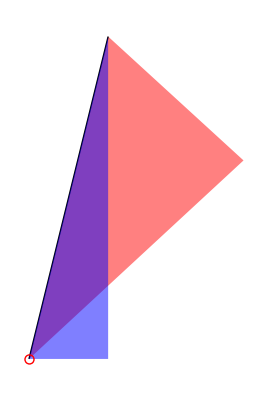
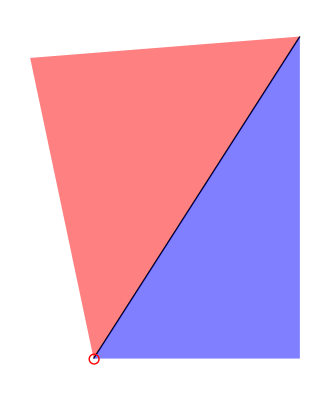
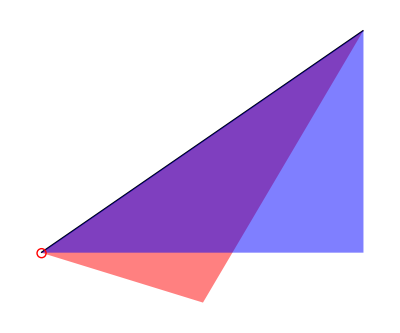
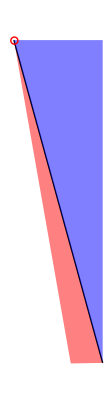
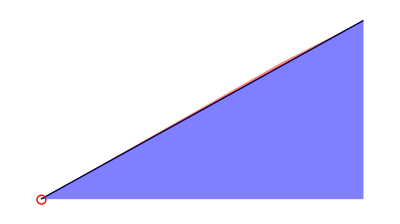
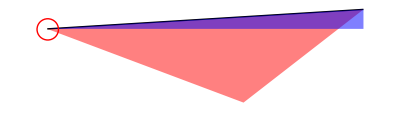
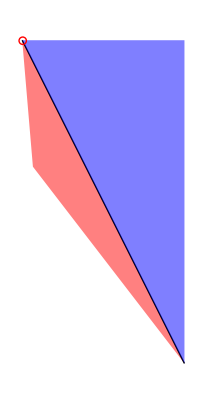
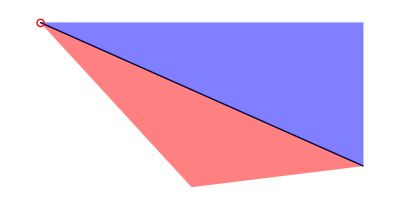
-Graphics- | 76.159 | Diagonal
-Graphics- | 57.3309 | Diagonal
-Graphics- | 34.6293 | Diagonal
-Graphics- | 74.5153 | Diagonal
-Graphics- | 29.0895 | Diagonal
-Graphics- | 3.55249 | Horizontal
-Graphics- | 63.247 | Diagonal
-Graphics- | 24.0114 | Diagonal
-Graphics- | 39.7244 | Diagonal
-Graphics- | 5.36407 | Horizontal

```mathematica
sideTests=With[
{side=TriangleGreatestSide@#},
{Graphics[{
Pink,#,
Black,Thick,Line@side,
Blue,Opacity@.5,Triangle[Append[side,{Last[side]⟦1⟧,First[side]⟦2⟧}]],
Red,Opacity@1.,Circle[First@side,0.1]
}],
N[Angle@side/Degree],
AngleOrientation@Angle@side}
]&/@Polygon/@RandomReal[10,{10,3,2}];
Grid[sideTests,Frame->All]
```

#### Greatest side position

```mathematica
triangle=RandomPolygon@3
```

Polygon[…]

```mathematica
greatestSide=TriangleGreatestSide@triangle
```

{{0.0505077,0.248364},{0.854985,0.73204}}

```mathematica
mid=Midpoint@greatestSide
```

{0.452746,0.490202}

```mathematica
greatestSideOrientation=AngleOrientation@Angle@greatestSide
```

Diagonal

```mathematica
height=Complement[PolygonCoordinates@triangle,greatestSide]//First
```

{0.248026,0.892977}

Vertical
mid.x > height.x = Right
mid.x < height.x = Left
Horizontal
mid.y > height.y = Top
mid.y < height.y = Bottom
Diagonal
mid.x > height.x, mid.y > height.y = Top right
mid.x > height.x, mid.y < height.y = Bottom right
mid.x < height.x, mid.y > height.y = Top left
mid.x < height.x, mid.y < height.y = Bottom left

```mathematica
rules={
{"Vertical",True,_}-> "Right",
{"Vertical",False,_}-> "Left",
{"Horizontal",_,True}-> "Top",
{"Horizontal",_,False}-> "Bottom",
{"Diagonal",True,True}-> "Top right",
{"Diagonal",True,False}-> "Bottom right",
{"Diagonal",False,True}-> "Top left",
{"Diagonal",False,False}-> "Bottom left"
};
```

```mathematica
{greatestSideOrientation,First@mid>First@height,Last@mid>Last@height}/.rules
```

Bottom right

```mathematica
RelativeLinePosition[line_List,point_List]:=Block[
{rules,mid},
rules={
{"Vertical",True,_}-> "Right",{"Vertical",False,_}-> "Left",
{"Horizontal",_,True}-> "Top",{"Horizontal",_,False}-> "Bottom",
{"Diagonal",True,True}-> "Top right",{"Diagonal",True,False}-> "Bottom right",
{"Diagonal",False,True}-> "Top left",{"Diagonal",False,False}-> "Bottom left"};
mid=Midpoint@line;
{AngleOrientation@Angle@line,First@mid>First@point,Last@mid>Last@point}/.rules
]
```

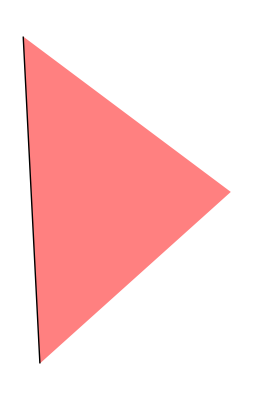
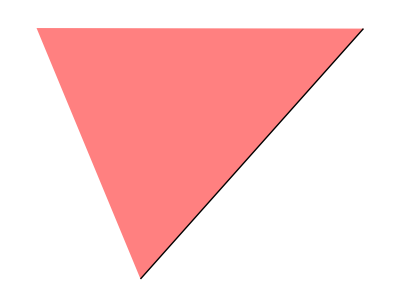
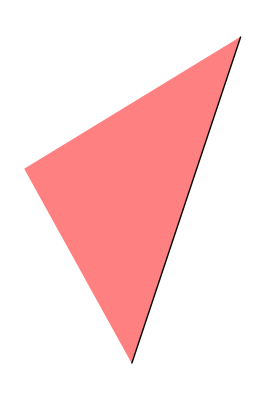
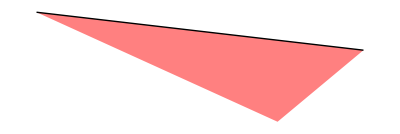
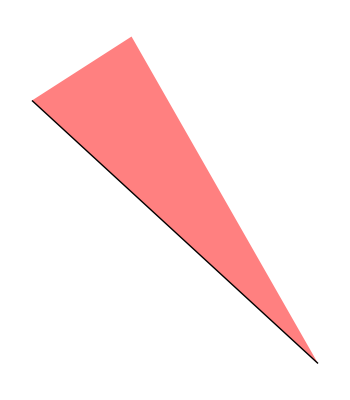
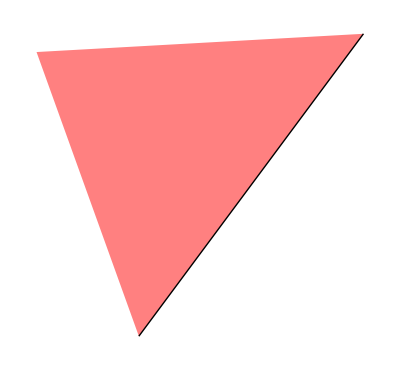
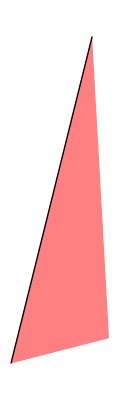
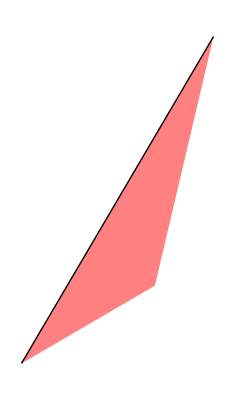
Triangle with greatest side | Greatest side orientation | Greatest side position
-Graphics- | Vertical | Left
-Graphics- | Diagonal | Bottom right
-Graphics- | Diagonal | Bottom right
-Graphics- | Horizontal | Top
-Graphics- | Diagonal | Bottom right
-Graphics- | Diagonal | Bottom right
-Graphics- | Diagonal | Top left
-Graphics- | Diagonal | Top left
-Graphics- | Diagonal | Bottom left
-Graphics- | Diagonal | Bottom left
-Graphics- | Diagonal | Top left
-Graphics- | Diagonal | Bottom left
-Graphics- | Horizontal | Bottom
-Graphics- | Diagonal | Top right
-Graphics- | Diagonal | Top right
-Graphics- | Diagonal | Bottom right
-Graphics- | Vertical | Right
-Graphics- | Diagonal | Bottom right
-Graphics- | Vertical | Right
-Graphics- | Diagonal | Top left
-Graphics- | Horizontal | Top
-Graphics- | Diagonal | Top left
-Graphics- | Diagonal | Bottom left
-Graphics- | Diagonal | Bottom right
-Graphics- | Diagonal | Top right
-Graphics- | Horizontal | Top
-Graphics- | Diagonal | Top left
-Graphics- | Diagonal | Top left
-Graphics- | Diagonal | Bottom right
-Graphics- | Diagonal | Bottom right

```mathematica
relativeLinePositionTests=Block[
{greatestSide,height,orientation,relativePosition},
greatestSide=TriangleGreatestSide@#;
height=Complement[PolygonCoordinates@#,greatestSide]//First;
orientation=AngleOrientation@Angle@greatestSide;
relativePosition=RelativeLinePosition[greatestSide,height];
{Graphics[{Pink,#,Black,Thick,Line@greatestSide}],orientation,relativePosition}
]&/@Polygon/@RandomReal[10,{30,3,2}];
Grid[PrependTo[relativeLinePositionTests,Style[#,Bold]&/@{"Triangle with greatest side","Greatest side orientation","Greatest side position"}],Frame->All]
```

```mathematica
Range[10]/.{a_?(#>5&):> ":)"}
```

{1,2,3,4,5,:),:),:),:),:)}

```mathematica
Range[10]/.{a_?(Between[#,{5,10}]&):> ":)"}
```

{1,2,3,4,:),:),:),:),:),:)}

```mathematica
Range[10]/.{a_?(Between[#,{5,10}]&)|1:> ":)"}
```

{:),2,3,4,:),:),:),:),:),:)}

#### TriangleDescription

```mathematica
StringList[list_List]:=With[
{str=Row[ToLowerCase@list,", "]},
StringReplace[rest__~~", "~~s__~~EndOfString:> rest<>" and "<>s]@ToString[str]
]
```

```mathematica
TriangleDescription[triangle_]:=Block[
{characteristics,side,sidestr},
characteristics=StringList@TriangleCharacteristics@triangle;
side=AngleOrientation@Angle@TriangleGreatestSide@triangle;
sidestr=If[Not[TriangleEquilateralQ@triangle]," triangle, with its greatest side as a "<>ToLowerCase[side]<>" line"," triangle"];
characteristics<>sidestr
]/;SimplePolygonQ@triangle
```

```mathematica
TriangleDescription[graphics_Graphics]:=Block[
{primitivesAndDirectives,color,triangleDescription},
primitivesAndDirectives=graphics/.Graphics[arguments_List,___]:>  arguments;
color=ToLowerCase[Description[Select[primitivesAndDirectives,ColorQ]//First]];
triangleDescription=TriangleDescription[Select[primitivesAndDirectives,TrianglePolygonQ]//First];
"A graphic consisting of a "<>color<>", "<>triangleDescription<>"."
]
```

Some tests

```mathematica
triangleDescriptionTests=Block[
{color,polygon,graphics},
color=RGBColor@RandomReal[1,{3}];
polygon=Polygon@#;
graphics=Graphics[{color,polygon}];
{graphics,ToString@graphics,TextString@graphics,SpokenString@graphics,TriangleDescription@graphics}
]&/@RandomReal[10,{10,3,2}];
Grid[PrependTo[triangleDescriptionTests,Style[#,Bold]&/@{"Graphics","ToString","TextString","SpokenString","TriangleDescription"}],Frame->All]
```

StringJoin::string: String expected at position 2 in A graphic consisting of a <>ToLowerCase[Description[RGBColor[List[0.7845757519561365, 0.8310641234919509, 0.7568755039427815]]]]<>, scalene triangle, with its greatest side as a diagonal line..

StringJoin::string: String expected at position 2 in A graphic consisting of a <>ToLowerCase[Description[RGBColor[List[0.4909404025956503, 0.7435123447434917, 0.7120909937678594]]]]<>, scalene triangle, with its greatest side as a horizontal line..

StringJoin::string: String expected at position 2 in A graphic consisting of a <>ToLowerCase[Description[RGBColor[List[0.2900958256609203, 0.7472028264130908, 0.054874750996552146]]]]<>, scalene and obtuse triangle, with its greatest side as a diagonal line..

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Graphics | ToString | TextString | SpokenString | TriangleDescription
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a <>ToLowerCase[Description[RGBColor[{0.7845757519561365, 0.8310641234919509, 0.7568755039427815}]]]<>, scalene triangle, with its greatest side as a diagonal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a <>ToLowerCase[Description[RGBColor[{0.4909404025956503, 0.7435123447434917, 0.7120909937678594}]]]<>, scalene triangle, with its greatest side as a horizontal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a <>ToLowerCase[Description[RGBColor[{0.2900958256609203, 0.7472028264130908, 0.054874750996552146}]]]<>, scalene and obtuse triangle, with its greatest side as a diagonal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a <>ToLowerCase[Description[RGBColor[{0.19355431685244673, 0.9648885831051288, 0.6926132385023653}]]]<>, scalene and obtuse triangle, with its greatest side as a diagonal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a <>ToLowerCase[Description[RGBColor[{0.6950145151803118, 0.6103076403059744, 0.416896367118081}]]]<>, scalene and obtuse triangle, with its greatest side as a diagonal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a <>ToLowerCase[Description[RGBColor[{0.8920897445365479, 0.02710157896698373, 0.1762698250946737}]]]<>, scalene triangle, with its greatest side as a diagonal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a <>ToLowerCase[Description[RGBColor[{0.8575541592415037, 0.6956291978357889, 0.6698426642974256}]]]<>, scalene and obtuse triangle, with its greatest side as a diagonal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a <>ToLowerCase[Description[RGBColor[{0.27133263432385424, 0.010828188939948635, 0.8862971155999355}]]]<>, scalene and obtuse triangle, with its greatest side as a diagonal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a <>ToLowerCase[Description[RGBColor[{0.4684429422490779, 0.16973699572674206, 0.3497133522377691}]]]<>, scalene and obtuse triangle, with its greatest side as a horizontal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a <>ToLowerCase[Description[RGBColor[{0.21032774422738587, 0.37034228605011976, 0.30844770514873066}]]]<>, scalene triangle, with its greatest side as a diagonal line.

```mathematica
triangles={
Triangle[],AASTriangle[Pi/6,Pi/3,1],
SSSTriangle[3,4,5],SASTriangle[1,Pi/2,2],
ASATriangle[Pi/6,1,Pi/3],
Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}],
Polygon[{{0,0},{10,10},{10,20}}],
RandomPolygon@3
};
```

```mathematica
triangleDescriptionTests2=Block[
{color,graphics},
color=RGBColor@RandomReal[1,{3}];
graphics=Graphics[{color,#}];
{graphics,ToString@graphics,TextString@graphics,SpokenString@graphics,TriangleDescription@graphics}
]&/@triangles;
Grid[PrependTo[triangleDescriptionTests2,Style[#,Bold]&/@{"Graphics","ToString","TextString","SpokenString","TriangleDescription"}],Frame->All]
```

First::nofirst: {} has zero length and no first element.

StringJoin::string: String expected at position 2 in A graphic consisting of a <>ToLowerCase[Description[RGBColor[List[0.8029912810641753, 0.18002263702715493, 0.45183721836049306]]]]<>, <>TriangleDescription[First[{}]]<>..

StringJoin::string: String expected at position 4 in A graphic consisting of a <>ToLowerCase[Description[RGBColor[List[0.8029912810641753, 0.18002263702715493, 0.45183721836049306]]]]<>, <>TriangleDescription[First[{}]]<>..

First::nofirst: {} has zero length and no first element.

StringJoin::string: String expected at position 2 in A graphic consisting of a <>ToLowerCase[Description[RGBColor[List[0.8092820372438649, 0.43265930060657465, 0.8792216584725256]]]]<>, <>TriangleDescription[First[{}]]<>..

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

Graphics | ToString | TextString | SpokenString | TriangleDescription
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 0.803, 0.18, 0.452 and Triangle of the list the list 0, 0, the list 1, 0, the list 0, 1 | A graphic consisting of a <>ToLowerCase[Description[RGBColor[{0.8029912810641753, 0.18002263702715493, 0.45183721836049306}]]]<>, <>TriangleDescription[First[{}]]<>.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 0.809, 0.433, 0.879 and Triangle of the list the list 0, 0, the list 2, 0, the list 3 halves, 1 half times square root of 3 | A graphic consisting of a <>ToLowerCase[Description[RGBColor[{0.8092820372438649, 0.43265930060657465, 0.8792216584725256}]]]<>, <>TriangleDescription[First[{}]]<>.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 0.7, 0.953, 0.207 and Triangle of the list the list 0, 0, the list 5, 0, the list 16 fifths, 12 fifths | A graphic consisting of a <>ToLowerCase[Description[RGBColor[{0.7000581753183479, 0.9534023520593629, 0.20674534609604134}]]]<>, <>TriangleDescription[First[{}]]<>.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 0.507, 0.231, 0.389 and Triangle of the list the list 0, 0, the list square root of 5, 0, the list 4 times one over square root of 5, 2 times one over square root of 5 | A graphic consisting of a <>ToLowerCase[Description[RGBColor[{0.5073521233388898, 0.2305974194082292, 0.3887405542499831}]]]<>, <>TriangleDescription[First[{}]]<>.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 0.904, 0.809, 0.574 and Triangle of the list the list 0, 0, the list 1, 0, the list 3 fourths, 1 fourth times square root of 3 | A graphic consisting of a <>ToLowerCase[Description[RGBColor[{0.9038093786355317, 0.8086318461287898, 0.5737825743154537}]]]<>, <>TriangleDescription[First[{}]]<>.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a <>ToLowerCase[Description[RGBColor[{0.8076187391720504, 0.11963021706018329, 0.9283434570042879}]]]<>, <>TriangleDescription[First[{}]]<>.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a <>ToLowerCase[Description[RGBColor[{0.5118126935211993, 0.5804564287725986, 0.05639712934210617}]]]<>, <>TriangleDescription[First[{}]]<>.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a <>ToLowerCase[Description[RGBColor[{0.04797711939782601, 0.9544459803159919, 0.6314598553704123}]]]<>, <>TriangleDescription[First[{}]]<>.

## Keywords

Textual description

Graphics

Graphics primitives

Triangles

## Acknowledgment

Mentor: Daavid Väänänen

Thank you for always saying  good things about my work and progress. Your mentoring pushed me to do more and better each day of the summer school. This was very important for me to be able to achieve the results I wanted.

For my family and friends that always support me.

For Stephen Wolfram and all the WSS20 people that made it possible.

## References

[1] https://www.bbc.co.uk/bitesize/topics/zwckjxs/articles/ztf9h39